# Oscillation Rings, Circles, Radial Regions And Shells Density, Pressure And Velocity Data Analysis.

```mathematica
Clear["Global`*"];
```

Loading Simulation Tool.

```mathematica
<<SimulationTools`
```

Name Of Simulation And Useful Constants.

```mathematica
(*Set Simulation Name*)
NameOfSimulation="BU0CowlNonRadiall2m2StergHLLEFull";
(*Specify Web Page File Directory*)
WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/General/";
(*Important Constants In CGS Units*)
GravConstCGS=6.67384*10^-8;(*cm^3·g^-1·s^-2*)
LightSpeedCGS=29979245800;(*cm·s^-1*)
SolarMassCGS=1.9891*10^33;(*g*)
(*Solar Masses To Seconds And Vice Versa Transformation Coefficients*)
SolMasToSec=4.92686*10^-6;
SecToSolMas=1/SolMasToSec;
(*Solar Masses To Meters And Vice Versa Transformation Coefficients*)
SolMasToMeters=1477.04;
MetersToSolMas=1/SolMasToMeters;
(*Coefficient That Converts Density From Geometrized To CGS Units*)
GeoToCGSConvPress=LightSpeedCGS^8/(GravConstCGS^3*SolarMassCGS^2);(*c^8/G^3·(M_⊙)^2 to g/cm·s^3*)
(*Coefficient That Converts Velocity From Geometrized To CGS Units*)
GeoToCGSConvVel=LightSpeedCGS;(*c To cm/s*)
(*Coefficient That Converts Density From Geometrized To CGS Units*)
GeoToCGSConvDens=LightSpeedCGS^6/(GravConstCGS^3*SolarMassCGS^2);(*c^6/G^3·(M_⊙)^2 to g/cm^3*)
(*Stellar Characteristics*)
MassNS=1.400163;
EqRadiusNS=9.585522;
StellarOblatnessNS=1.0000;
PolRadiusNS=EqRadiusNS*StellarOblatnessNS;
OmegaNS=0.0000;
RotFreqNS=OmegaNS*SecToSolMas/(2*Pi);
AngVelNS=OmegaNS*SecToSolMas;
Kapa=100;
Gama=2.0;

SetDirectory["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"-all"];
RhoCentInit=Import["rho.maximum.asc","Table",HeaderLines->9,Numeric->True,IgnoreEmptyLines->True][[1,3]];
RhoAtmInit=Import["rho.minimum.asc","Table",HeaderLines->9,Numeric->True,IgnoreEmptyLines->True][[1,3]];
(*
SetDirectory["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"Initial"<>"/"<>NameOfSimulation<>"Initial"<>"-all"];
RhoCentInitBackround=Import["rho.maximum.asc","Table",HeaderLines->9,Numeric->True,IgnoreEmptyLines->True][[1,3]];
*)
(*Print*)
Print[Style["Stellar characteristics in geometrical units",18,Black,FontWeight->Bold]];
Print[Style["Stellar mass: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[MassNS,FontSize->16,FontFamily->"Times"],Style[Subscript["M","⊙"],FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar equatorial radius: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[EqRadiusNS,FontSize->16,FontFamily->"Times"],Style[Subscript["M","⊙"],FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar polar radius: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[PolRadiusNS,FontSize->16,FontFamily->"Times"],Style[Subscript["M","⊙"],FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar angular velocity: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[OmegaNS,FontSize->16,FontFamily->"Times"],Style[" in frequency G.U.",FontSize->16,FontFamily->"Times"]];
Print[Style["Initial stellar central density: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[RhoCentInit,FontSize->16,FontFamily->"Times"],Style[" in density G.U.",FontSize->16,FontFamily->"Times"]];
Print[Style["Initial stellar atmospheric density: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[RhoAtmInit,FontSize->16,FontFamily->"Times"],Style[" in density G.U.",FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar characteristics",18,Black,FontWeight->Bold]];
Print[Style["Stellar mass: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[MassNS*SolarMassCGS,FontSize->16,FontFamily->"Times"],Style[" g",FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar equatorial radius: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[EqRadiusNS*SolMasToMeters/1000,FontSize->16,FontFamily->"Times"],Style[" km",FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar polar radius: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[PolRadiusNS*SolMasToMeters/1000,FontSize->16,FontFamily->"Times"],Style[" km",FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar rotational frequency: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[RotFreqNS,FontSize->16,FontFamily->"Times"],Style[" Hz",FontSize->16,FontFamily->"Times"]];
Print[Style["Stellar angular velocity: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[AngVelNS,FontSize->16,FontFamily->"Times"],Style[" Hz",FontSize->16,FontFamily->"Times"]];
Print[Style["Initial stellar central density: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[RhoCentInit*GeoToCGSConvDens,FontSize->16,FontFamily->"Times"],Style[" g/cm^3",FontSize->16,FontFamily->"Times"]];
Print[Style["Initial stellar atmospheric density: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[RhoAtmInit*GeoToCGSConvDens,FontSize->16,FontFamily->"Times"],Style[" g/cm^3",FontSize->16,FontFamily->"Times"]];
```

Stellar characteristics in geometrical units

Stellar mass: 1.40016 M_⊙

Stellar equatorial radius: 9.58552 M_⊙

Stellar polar radius: 9.58552 M_⊙

Stellar angular velocity: 0. in frequency G.U.

Initial stellar central density: 0.00128 in density G.U.

Initial stellar atmospheric density: 1.28×10^-10 in density G.U.

Stellar characteristics

Stellar mass: 2.78506×10^33 g

Stellar equatorial radius: 14.1582 km

Stellar polar radius: 14.1582 km

Stellar rotational frequency: 0. Hz

Stellar angular velocity: 0. Hz

Initial stellar central density: 7.90121×10^14 g/cm^3

Initial stellar atmospheric density: 7.90121×10^7 g/cm^3

## Oscillation Rings/Cirlces/Radial Region Analysis.

Re-set Directory.

```mathematica
(*Re-Setting Directory*)
SetDirectory["/home/athanstav/Simulations/CygnusRuns"];
```

Simulation Specifics.

```mathematica
(*Initial And Final Iteration Index*)
InitItAdd=1;FinItSub=0;

(*Setting Finest Refinment Level*)
SetDirectory["/home/athanstav/Simulations/CygnusRuns"];
RF=ReadMaxRefinementLevels[NameOfSimulation]-1;

(*2d Data*)
(*
ItSampleStep2d=ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[2]];
TotalDataPoints2d=Dimensions[ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF]][[1]];
FinalItSampleStep2d=ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[TotalDataPoints2d]];
ItTimeStepSolMas2d=ReadTimeStep[NameOfSimulation,RefinementLevel->RF];
*)
ItSampleStep2d=ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[2]];
TotalDataPointsFull2d=Dimensions[ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF]][[1]];
TotalDataPoints2d=Dimensions[ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[InitItAdd;;TotalDataPointsFull2d-FinItSub]]-ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[InitItAdd]]][[1]];
FinalItSampleStep2d=(ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[InitItAdd;;TotalDataPointsFull2d-FinItSub]]-ReadIterations[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF][[InitItAdd]])[[TotalDataPoints2d]];
ItTimeStepSolMas2d=ReadTimeStep[NameOfSimulation,RefinementLevel->RF];

ItTimeStepSec2d=ItTimeStepSolMas2d*SolMasToSec;
SampTimeStepSolMas2d=ItSampleStep2d*ItTimeStepSolMas2d;
SampTimeStepSec2d=SampTimeStepSolMas2d*SolMasToSec;
TotSimTimeInSolMas2d=FinalItSampleStep2d*ItTimeStepSolMas2d;
TotSimTimeInSec2d=TotSimTimeInSolMas2d*SolMasToSec;

Print[Style["Simulation specifics for 2d data:",18,FontFamily->"Times",Black,FontWeight->Bold]]
Print[Style["Iteration time step in solar masses :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[ItTimeStepSolMas2d,FontSize->16,FontFamily->"Times"],
Style[" M_⊙",FontSize->16,FontFamily->"Times"],
Style[" Iteration time step in seconds :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[ItTimeStepSec2d,FontSize->16,FontFamily->"Times"],
Style[" s",FontSize->16,FontFamily->"Times"]]
Print[Style["Data are being outputed every ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[ItSampleStep2d,FontSize->16,FontFamily->"Times"],
Style[" iteration steps.",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[" Total number of outputed time slices of data :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[TotalDataPoints2d,FontSize->16,FontFamily->"Times"]]
Print[Style["Sample (output) time step in solar masses :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[SampTimeStepSolMas2d,FontSize->16,FontFamily->"Times"],
Style[" M_⊙",FontSize->16,FontFamily->"Times"],
Style[" Sample (output) time step in seconds :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[SampTimeStepSec2d,FontSize->16,FontFamily->"Times"],
Style[" s",FontSize->16,FontFamily->"Times"]]
Print[Style["Total evolution time in solar masses :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[TotSimTimeInSolMas2d,FontSize->16,FontFamily->"Times"],Style[" M_⊙",FontSize->16,FontFamily->"Times"],
Style[" Total evolution time in seconds :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[TotSimTimeInSec2d,FontSize->16,FontFamily->"Times"],Style[" s",FontSize->16,FontFamily->"Times"]]
```

Simulation specifics for 2d data:

Iteration time step in solar masses :0.0406252 M_⊙ Iteration time step in seconds :2.00155×10^-7 s

Data are being outputed every 48 iteration steps. Total number of outputed time slices of data :1539

Sample (output) time step in solar masses :1.95001 M_⊙ Sample (output) time step in seconds :9.60742×10^-6 s

Total evolution time in solar masses :2999.11 M_⊙ Total evolution time in seconds :0.0147762 s

Setting Accuracy Of FFTs.

```mathematica
(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationRings/General/";

AccAdj2d=1;
DatAnItStep2d=AccAdj2d*ItSampleStep2d;
DatAnTimeStepSolMas2d=AccAdj2d*SampTimeStepSolMas2d;
DatAnTimeStepInSec2d=DatAnTimeStepSolMas2d*SolMasToSec;
DatAnSampRate2d=1/DatAnTimeStepInSec2d;
DatAnTotDataPoints2d=Floor[TotalDataPoints2d/AccAdj2d];
DatAnMaxResolveFreq2d=DatAnTotDataPoints2d/(2*TotSimTimeInSec2d);
DatAnFreqResolution2d=Ceiling[1/(DatAnTimeStepInSec2d*DatAnTotDataPoints2d)];
DatHertzConv2d=DatAnSampRate2d/DatAnTotDataPoints2d;

Print[Style["2d Data",FontWeight->Bold,FontSize->18,FontFamily->"Times"]]
Print[Style["Rate at which data are sampled : ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[DatAnSampRate2d,FontSize->16,FontFamily->"Times"],
Style["Hz",FontSize->16,FontFamily->"Times"]]
Print[Style["Maximum resolvable frequency : ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[DatAnMaxResolveFreq2d,FontSize->16,FontFamily->"Times"],
Style["Hz",FontSize->16,FontFamily->"Times"]]
Print[Style["Frequency resolution: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[DatAnFreqResolution2d,FontSize->16,FontFamily->"Times"],
Style["Hz",FontSize->16,FontFamily->"Times"]]

Export[WebPageFileDirectory<>"
RateDataSampling2d.jpg","Rate at which data are sampled:"<>ToString[DatAnSampRate2d]<>"Hz
Maximum resolvable frequency:"<>ToString[DatAnMaxResolveFreq2d]<>"Hz"];
```

2d Data

Rate at which data are sampled : 104086.Hz

Maximum resolvable frequency : 52076.9Hz

Frequency resolution: 68Hz

Definition Of Density, Pressure, Velocity And Coordinate Functions.

```mathematica
(*Spherical Harmonic Functions In Cartesian Coordinates On The xy-Plane*)
Y00xy[x_,y_]:=1/2*1/Sqrt[Pi];
Y22nxy[x_,y_]:=1/4*Sqrt[15/(2*Pi)]*(x-I*y)^2/(x^2+y^2);
Y22pxy[x_,y_]:=1/4*Sqrt[15/(2*Pi)]*(x+I*y)^2/(x^2+y^2);
```

```mathematica
(*Grid Characteristics*)
```

```mathematica
(*2d Data*)

(*xy-Plane*)
DimXYx=Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF]]][[1]];
DimXYy=Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xy",Iteration->0,RefinementLevel->RF]]][[2]];
XYCoordStepX=ReadGridSpacings[NameOfSimulation,RefinementLevel->RF][[1]];
XYCoordStepY=ReadGridSpacings[NameOfSimulation,RefinementLevel->RF][[2]];

(*xz-Plane*)
DimXZx=Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xz", Iteration->0,RefinementLevel->RF]]][[1]];
DimXZz=Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xz", Iteration->0,RefinementLevel->RF]]][[2]];
XZCoordStepX=ReadGridSpacings[NameOfSimulation, RefinementLevel->RF][[1]];
XZCoordStepZ=ReadGridSpacings[NameOfSimulation, RefinementLevel->RF][[3]];
```

#### Octane Space Symmetry x≥0,y≥0,z≥0

```mathematica
(*Setting The Coordinates Of The Center Of The Star On The Grid*)
Symmetry="Octane";
CentX=3+1;CentY=3+1;CentZ=3+1;
```

#### Quarter Space Symmetry x≥0,z≥0

```mathematica
(*Setting The Coordinates Of The Center Of The Star On The Grid*)
Symmetry="Quarter";
CentX=3+1(*(Floor[DimXYx/2])+1*);CentY=(Floor[DimXYy/2])+1;CentZ=3+1;
```

#### Half Space Symmetry z≥0

```mathematica
(*Setting The Coordinates Of The Center Of The Star On The Grid*)
Symmetry="Half";
CentX=(Floor[DimXYx/2])+1;CentY=(Floor[DimXYy/2])+1;CentZ=3+1;
```

```mathematica
(*Definition Of Coordinate Functions*)
```

```mathematica
(*2d Data*)

(*xy-Plane*)
CoordXYx[x_]:=(x-CentX)*XYCoordStepX;
CoordXYy[y_]:=(y-CentY)*XYCoordStepY;
InvCoordXYx[x_]:=(x/XYCoordStepX)+CentX;
InvCoordXYy[y_]:=(y/XYCoordStepY)+CentY;

(*xz-Plane*)
CoordXZx[x_]:=(x-CentX)*XZCoordStepX;
CoordXZz[z_]:=(z-CentZ)*XZCoordStepZ;
InvCoordXZx[x_]:=(x/XZCoordStepX)+CentX;
InvCoordXZz[z_]:=(z/XZCoordStepZ)+CentZ;
```

```mathematica
(*Study Of The Actual Hydro Quantities Or Their Deviation From The Unperturded Model*)
DeltaQ=1;(*0,1*)
```

#### 2d Data

```mathematica
(*xy-Plane*)
```

```mathematica
(*Density*)
DensXY[x_,y_,t_]:= ReadGridFunction[NameOfSimulation,"rho","xy",Iteration->t,RefinementLevel->RF][[x,y]];
DensXYCGS[x_,y_,t_]:= ReadGridFunction[NameOfSimulation,"rho","xy",Iteration->t,RefinementLevel->RF][[x,y]]*GeoToCGSConvDens;
DensityDataListXYInit=ToListOfData[ReadGridFunction[NameOfSimulation,"rho", "xy", Iteration->0,RefinementLevel->RF]];
DensXYInit[x_,y_]:=DensityDataListXYInit[[x,y]];
DensXYInitCGS[x_,y_]:=DensityDataListXYInit[[x,y]]*GeoToCGSConvDens;
```

```mathematica
(*Pressure*)
PressureXYChoise=1;
PressXY[x_,y_,t_]:= ReadGridFunction[NameOfSimulation,"press","xy",Iteration->t,RefinementLevel->RF][[x,y]];
PressXYCGS[x_,y_,t_]:= ReadGridFunction[NameOfSimulation,"press","xy",Iteration->t,RefinementLevel-> RF][[x,y]]*GeoToCGSConvPress;
PressDataListXYInit = ToListOfData[ReadGridFunction[NameOfSimulation,"press","xy", Iteration->0,RefinementLevel->RF]];
PressXYInit[x_,y_]:= PressDataListXYInit[[x,y]];
PressXYInitCGS[x_,y_]:= PressDataListXYInit[[x,y]]*GeoToCGSConvPress;
```

```mathematica
(*Pressure As A Function Of Density*)
PressureXYChoise=2;
PressXY[x_,y_,t_]:=Kapa*(ReadGridFunction[NameOfSimulation,"rho", "xy", Iteration ->t, RefinementLevel -> RF][[x,y]])^Gama;
PressXYCGS[x_,y_,t_]:=(Kapa*(ReadGridFunction[NameOfSimulation,"rho", "xy", Iteration ->t, RefinementLevel -> RF][[x,y]])^Gama)*GeoToCGSConvPress;
PressDataListXYInit =Kapa*(ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xy", Iteration -> 0, RefinementLevel -> RF]])^Gama;
PressXYInit[x_,y_]:= PressDataListXYInit[[x,y]];
PressXYInitCGS[x_,y_]:= PressDataListXYInit[[x,y]]*GeoToCGSConvPress;
```

```mathematica
(*Pressure Projected from 3d Data To The xy-Plane*)
PressureXYChoise=3; (*ItSampleStep2d==ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[2]]*) (*Testing The Correctness of this choice*)
PressXY[x_,y_,t_]:=(ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz",Iteration->t,RefinementLevel->RF]][[1;;,1;;,CentZ]])[[x,y]];
PressXYCGS[x_,y_,t_]:=(ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz",Iteration->t,RefinementLevel->RF]][[1;;,1;;,CentZ]])[[x,y]];
PressDataListXYInit =ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
PressXYInit[x_,y_]:= PressDataListXYInit[[x,y]];
PressXYInitCGS[x_,y_]:= PressDataListXYInit[[x,y]]*GeoToCGSConvPress;
```

```mathematica
(*Cartesian Contravariant Components Of Velocity*)
VelXYx[x_,y_,t_] := ReadGridFunction[NameOfSimulation,"velx","xy", Iteration -> t, RefinementLevel -> RF][[x,y]];
VelXYy[x_,y_,t_] := ReadGridFunction[NameOfSimulation,"vely","xy", Iteration -> t, RefinementLevel -> RF][[x,y]];
VelXYz[x_,y_,t_] := ReadGridFunction[NameOfSimulation,"velz","xy", Iteration -> t, RefinementLevel -> RF][[x,y]];
VelXYxCGS[x_,y_,t_] := ReadGridFunction[NameOfSimulation,"velx","xy", Iteration -> t, RefinementLevel -> RF][[x,y]]*GeoToCGSConvVel;
VelXYyCGS[x_,y_,t_] := ReadGridFunction[NameOfSimulation,"vely","xy", Iteration -> t, RefinementLevel -> RF][[x,y]]*GeoToCGSConvVel;
VelXYzCGS[x_,y_,t_] := ReadGridFunction[NameOfSimulation,"velz","xy", Iteration -> t, RefinementLevel -> RF][[x,y]]*GeoToCGSConvVel;
VelxDataListXYInit = ToListOfData[ReadGridFunction[NameOfSimulation,"velx","xy", Iteration -> 0, RefinementLevel -> RF]];
VelyDataListXYInit = ToListOfData[ReadGridFunction[NameOfSimulation,"vely","xy", Iteration -> 0, RefinementLevel -> RF]];
VelzDataListXYInit = ToListOfData[ReadGridFunction[NameOfSimulation,"velz","xy", Iteration -> 0, RefinementLevel -> RF]];
VelxXYInit[x_,y_]:= VelxDataListXYInit[[x,y]];
VelyXYInit[x_,y_]:= VelyDataListXYInit[[x,y]];
VelzXYInit[x_,y_]:= VelzDataListXYInit[[x,y]];
VelxXYInitCGS[x_,y_]:= VelxDataListXYInit[[x,y]]*GeoToCGSConvVel;
VelyXYInitCGS[x_,y_]:= VelyDataListXYInit[[x,y]]*GeoToCGSConvVel;
VelzXYInitCGS[x_,y_]:= VelzDataListXYInit[[x,y]]*GeoToCGSConvVel;
```

```mathematica
(*Matrices That Contain The Perturbed Covariant Three Metric Components At The Initial Moment*)
gxxPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxx","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gxyPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gxzPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gyxPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gyyPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gyzPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gzxPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gzyPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gzzPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gzz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
```

```mathematica
(*Perturbed Covariant Three Metric Components At The Initial Moment*)
gxxPerturbedXY[x_,y_]:= gxxPerturbedDataListXY[[x,y]];
gxyPerturbedXY[x_,y_]:= gxyPerturbedDataListXY[[x,y]];
gxzPerturbedXY[x_,y_]:= gxzPerturbedDataListXY[[x,y]];
gyxPerturbedXY[x_,y_]:= gyxPerturbedDataListXY[[x,y]];
gyyPerturbedXY[x_,y_]:= gyyPerturbedDataListXY[[x,y]];
gyzPerturbedXY[x_,y_]:= gyzPerturbedDataListXY[[x,y]];
gzxPerturbedXY[x_,y_]:= gzxPerturbedDataListXY[[x,y]];
gzyPerturbedXY[x_,y_]:= gzyPerturbedDataListXY[[x,y]];
gzzPerturbedXY[x_,y_]:= gzzPerturbedDataListXY[[x,y]];
MetricPerturbedDetDataListXY=gxxPerturbedDataListXY*gyyPerturbedDataListXY-gxyPerturbedDataListXY*gyxPerturbedDataListXY;
DetgPerturbedXY[x_,y_]:=MetricPerturbedDetDataListXY[[x,y]];
```

```mathematica
(*Matrices That Contain The Perturbed Contravariant Shift Components And The Lapse Function At The Initial Moment*)
AlphaPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","alp","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
BetaxPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betax","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
BetayPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betay","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
BetazPerturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betaz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];

(*Perturbed Contravariant Shift Components And Lapse Function At The Initial Moment*)
AlphaPerturbedXY[x_,y_]:= AlphaPerturbedDataListXY[[x,y]];
BetaxPerturbedXY[x_,y_]:= BetaxPerturbedDataListXY[[x,y]];
BetayPerturbedXY[x_,y_]:= BetayPerturbedDataListXY[[x,y]];
BetazPerturbedXY[x_,y_]:= BetazPerturbedDataListXY[[x,y]];
```

```mathematica
(*Cartesian Covariant Components Of Velocity*)
CovVelXYx[x_,y_,t_] :=gxxPerturbedXY[x,y]*VelXYx[x,y,t]+gxyPerturbedXY[x,y]*VelXYy[x,y,t]+gxzPerturbedXY[x,y]*VelXYz[x,y,t];
CovVelXYy[x_,y_,t_] :=gyxPerturbedXY[x,y]*VelXYx[x,y,t]+gyyPerturbedXY[x,y]*VelXYy[x,y,t]+gyzPerturbedXY[x,y]*VelXYz[x,y,t];
CovVelXYz[x_,y_,t_] :=gzxPerturbedXY[x,y]*VelXYx[x,y,t]+gzyPerturbedXY[x,y]*VelXYy[x,y,t]+gzzPerturbedXY[x,y]*VelXYz[x,y,t];
CovVelXYxCGS[x_,y_,t_] :=CovVelXYx[x,y,t]*GeoToCGSConvVel;
CovVelXYyCGS[x_,y_,t_] :=CovVelXYy[x,y,t]*GeoToCGSConvVel;
CovVelXYzCGS[x_,y_,t_] :=CovVelXYz[x,y,t]*GeoToCGSConvVel;
CovVelxDataListXYInit=gxxPerturbedDataListXY*VelxDataListXYInit+gxyPerturbedDataListXY*VelyDataListXYInit+gxzPerturbedDataListXY*VelzDataListXYInit;
CovVelyDataListXYInit=gyxPerturbedDataListXY*VelxDataListXYInit+gyyPerturbedDataListXY*VelyDataListXYInit+gyzPerturbedDataListXY*VelzDataListXYInit;
CovVelzDataListXYInit=gzxPerturbedDataListXY*VelxDataListXYInit+gzyPerturbedDataListXY*VelyDataListXYInit+gzzPerturbedDataListXY*VelzDataListXYInit;
CovVelxXYInit[x_,y_] :=CovVelxDataListXYInit[[x,y]];
CovVelyXYInit[x_,y_] :=CovVelyDataListXYInit[[x,y]];
CovVelzXYInit[x_,y_] :=CovVelzDataListXYInit[[x,y]];
CovVelxXYInitCGS[x_,y_] :=CovVelxDataListXYInit[[x,y]]*GeoToCGSConvVel;
CovVelyXYInitCGS[x_,y_] :=CovVelyDataListXYInit[[x,y]]*GeoToCGSConvVel;
CovVelzXYInitCGS[x_,y_] :=CovVelzDataListXYInit[[x,y]]*GeoToCGSConvVel;
(*Initial Perturbed Lorentz Factor*)
LorentzFactorDataListXYInit=
1/Sqrt[1-VelxDataListXYInit*CovVelxDataListXYInit+VelyDataListXYInit*CovVelyDataListXYInit+VelzDataListXYInit*CovVelzDataListXYInit];
LorentzFactorDataListXYInitCGS=1/Sqrt[1-(VelxDataListXYInit*CovVelxDataListXYInit+VelyDataListXYInit*CovVelyDataListXYInit+VelzDataListXYInit*CovVelzDataListXYInit)*GeoToCGSConvVel^2];
```

```mathematica
(*xz-Plane*)
```

```mathematica
(*Density*)
DensXZ[x_,z_,t_]:= ReadGridFunction[NameOfSimulation,"rho","xz", Iteration ->t, RefinementLevel -> RF][[x,z]];
DensXZCGS[x_,z_,t_]:= ReadGridFunction[NameOfSimulation,"rho","xz", Iteration ->t, RefinementLevel -> RF][[x,z]]*GeoToCGSConvDens;
DensityDataListXZInit = ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xz", Iteration -> 0, RefinementLevel -> RF]];
DensXZInit[x_,z_]:= DensityDataListXZInit[[x,z]];
DensXZInitCGS[x_,z_]:= DensityDataListXZInit[[x,z]]*GeoToCGSConvDens;
```

```mathematica
(*Pressure*)
PressureXZChoise=PressureXYChoise;
PressXZ[x_,z_,t_]:= ReadGridFunction[NameOfSimulation,"press", "xz", Iteration -> t, RefinementLevel -> RF][[x, z]];
PressXZCGS[x_,z_,t_]:= ReadGridFunction[NameOfSimulation,"press", "xz", Iteration -> t, RefinementLevel -> RF][[x, z]]*GeoToCGSConvPress;
PressDataListXZInit = ToListOfData[ReadGridFunction[NameOfSimulation,"press","xz", Iteration -> 0, RefinementLevel -> RF]];
PressXZInit[x_,z_]:= PressDataListXZInit[[x,z]];
PressXZInitCGS[x_,z_]:= PressDataListXZInit[[x,z]]*GeoToCGSConvPress;
```

```mathematica
(*Pressure As A Function Of Density*)
PressureXZChoise=PressureXYChoise;
PressXZ[x_, z_, t_]:=Kapa*(ReadGridFunction[NameOfSimulation,"rho", "xz", Iteration -> t, RefinementLevel -> RF][[x, z]])^Gama;
PressXZCGS[x_, z_, t_]:=(Kapa*(ReadGridFunction[NameOfSimulation,"rho", "xz", Iteration -> t, RefinementLevel -> RF][[x, z]])^Gama)*GeoToCGSConvPress;
PressDataListXZInit =Kapa*( ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xz", Iteration -> 0, RefinementLevel -> RF]])^Gama;
PressXZInit[x_, z_]:= PressDataListXZInit[[x, z]];
PressXZInitCGS[x_, z_]:= PressDataListXZInit[[x, z]]*GeoToCGSConvPress;
```

```mathematica
(*Pressure Projected from 3d Data To The xz-Plane*)
PressureXZChoise=PressureXYChoise;  (*ItSampleStep2d==ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[2]]*) (*Testing The Correctness of this choice*)
PressXZ[x_,z_,t_]:=(ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz",Iteration->t,RefinementLevel->RF]][[1;;,CentY,1;;]])[[x,z]];
PressXZCGS[x_,z_,t_]:=(ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz",Iteration->t,RefinementLevel->RF]][[1;;,CentY,1;;]])[[x,z]];
PressDataListXZInit =ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
PressXZInit[x_,z_]:= PressDataListXZInit[[x,z]];
PressXZInitCGS[x_,z_]:= PressDataListXZInit[[x,z]]*GeoToCGSConvPress;
```

```mathematica
(*Cartesian Contravariant Components Of Velocity*)
VelXZx[x_, z_, t_]:= ReadGridFunction[NameOfSimulation,"velx","xz", Iteration -> t, RefinementLevel -> RF][[x, z]];
VelXZy[x_, z_, t_]:= ReadGridFunction[NameOfSimulation,"vely","xz", Iteration -> t, RefinementLevel -> RF][[x, z]];
VelXZz[x_, z_, t_]:= ReadGridFunction[NameOfSimulation,"velz","xz", Iteration -> t, RefinementLevel -> RF][[x, z]];
VelXZxCGS[x_, z_, t_]:= ReadGridFunction[NameOfSimulation,"velx","xz", Iteration -> t, RefinementLevel -> RF][[x, z]]*GeoToCGSConvVel;
VelXZyCGS[x_, z_, t_]:= ReadGridFunction[NameOfSimulation,"vely","xz", Iteration -> t, RefinementLevel -> RF][[x, z]]*GeoToCGSConvVel;
VelXZzCGS[x_, z_, t_]:= ReadGridFunction[NameOfSimulation,"velz","xz", Iteration -> t, RefinementLevel -> RF][[x, z]]*GeoToCGSConvVel;
VelxDataListXZInit = ToListOfData[ReadGridFunction[NameOfSimulation,"velx","xz", Iteration -> 0, RefinementLevel -> RF]];
VelyDataListXZInit = ToListOfData[ReadGridFunction[NameOfSimulation,"vely","xz", Iteration -> 0, RefinementLevel -> RF]];
VelzDataListXZInit = ToListOfData[ReadGridFunction[NameOfSimulation,"velz","xz", Iteration -> 0, RefinementLevel -> RF]];
VelxXZInit[x_,z_]:= VelxDataListXZInit[[x,z]];
VelyXZInit[x_,z_]:= VelyDataListXZInit[[x,z]];
VelzXZInit[x_,z_]:= VelzDataListXZInit[[x,z]];
VelxXZInitCGS[x_,z_]:= VelxDataListXZInit[[x,z]]*GeoToCGSConvVel;
VelyXZInitCGS[x_,z_]:= VelyDataListXZInit[[x,z]]*GeoToCGSConvVel;
VelzXZInitCGS[x_,z_]:= VelzDataListXZInit[[x,z]]*GeoToCGSConvVel;
```

```mathematica
(*Matrices That Contain The Perturbed Covariant Three Metric Components At The Initial Moment*)
gxxPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxx","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gxyPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gxzPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gyxPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gyyPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gyzPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gzxPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gzyPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gzzPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gzz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
```

```mathematica
(*Perturbed Covariant Metric Components At The Initial Moment*)
gxxPerturbedXZ[x_, z_]:= gxxPerturbedDataListXZ[[x,z]];
gxyPerturbedXZ[x_, z_]:= gxyPerturbedDataListXZ[[x,z]];
gxzPerturbedXZ[x_, z_]:= gxzPerturbedDataListXZ[[x,z]];
gyxPerturbedXZ[x_, z_]:= gyxPerturbedDataListXZ[[x,z]];
gyyPerturbedXZ[x_, z_]:= gyyPerturbedDataListXZ[[x,z]];
gyzPerturbedXZ[x_, z_]:= gyzPerturbedDataListXZ[[x,z]];
gzxPerturbedXZ[x_, z_]:= gzxPerturbedDataListXZ[[x,z]];
gzyPerturbedXZ[x_, z_]:= gzyPerturbedDataListXZ[[x,z]];
gzzPerturbedXZ[x_, z_]:= gzzPerturbedDataListXZ[[x,z]];
MetricPerturbedDetDataListXZ=gxxPerturbedDataListXZ*gyyPerturbedDataListXZ-gxyPerturbedDataListXZ*gyxPerturbedDataListXZ;
DetgPerturbedXZ[x_, z_]:=MetricPerturbedDetDataListXZ[[x, z]];
```

```mathematica
(*Matrices That Contain The Perturbed Contravariant Shift Components And The Lapse Function At The Initial Moment*)
AlphaPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","alp","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
BetaxPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betax","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
BetayPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betay","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
BetazPerturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betaz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];

(*Perturbed Contravariant Shift Components And Lapse Function At The Initial Moment*)
AlphaPerturbedXZ[x_, z_]:= AlphaPerturbedDataListXZ[[x, z]];
BetaxPerturbedXZ[x_, z_]:= BetaxPerturbedDataListXZ[[x, z]];
BetayPerturbedXZ[x_, z_]:= BetayPerturbedDataListXZ[[x, z]];
BetazPerturbedXZ[x_, z_]:= BetazPerturbedDataListXZ[[x, z]];
```

```mathematica
(*Cartesian Covariant Components Of Velocity*)
CovVelXZx[x_,z_,t_] :=gxxPerturbedXZ[x, z]*VelXZx[x,z,t]+gxyPerturbedXZ[x, z]*VelXZy[x,z,t]+gxzPerturbedXZ[x, z]*VelXZz[x,z,t];
CovVelXZy[x_,z_,t_] :=gyxPerturbedXZ[x, z]*VelXZx[x,z,t]+gyyPerturbedXZ[x, z]*VelXZy[x,z,t]+gyzPerturbedXZ[x, z]*VelXZz[x,z,t];
CovVelXZz[x_,z_,t_] :=gzxPerturbedXZ[x, z]*VelXZx[x,z,t]+gzyPerturbedXZ[x, z]*VelXZy[x,z,t]+gzzPerturbedXZ[x, z]*VelXZz[x,z,t];
CovVelXZxCGS[x_, z_, t_] :=CovVelXZx[x,z,t]*GeoToCGSConvVel;
CovVelXZyCGS[x_, z_, t_] :=CovVelXZy[x,z,t]*GeoToCGSConvVel;
CovVelXZzCGS[x_, z_, t_] :=CovVelXZz[x,z,t]*GeoToCGSConvVel;
CovVelxDataListXZInit=gxxPerturbedDataListXZ*VelxDataListXZInit+gxyPerturbedDataListXZ*VelyDataListXZInit+gxzPerturbedDataListXZ*VelzDataListXZInit;
CovVelyDataListXZInit=gyxPerturbedDataListXZ*VelxDataListXZInit+gyyPerturbedDataListXZ*VelyDataListXZInit+gyzPerturbedDataListXZ*VelzDataListXZInit;
CovVelzDataListXZInit=gzxPerturbedDataListXZ*VelxDataListXZInit+gzyPerturbedDataListXZ*VelyDataListXZInit+gzzPerturbedDataListXZ*VelzDataListXZInit;
CovVelxXZInit[x_, z_] :=CovVelxDataListXZInit[[x,z]];
CovVelyXZInit[x_, z_] :=CovVelyDataListXZInit[[x,z]];
CovVelzXZInit[x_, z_] :=CovVelzDataListXZInit[[x,z]];
CovVelxXZInitCGS[x_, z_] :=CovVelxDataListXZInit[[x,z]]*GeoToCGSConvVel;
CovVelyXZInitCGS[x_, z_] :=CovVelyDataListXZInit[[x,z]]*GeoToCGSConvVel;
CovVelzXZInitCGS[x_, z_] :=CovVelzDataListXZInit[[x,z]]*GeoToCGSConvVel;
(*Initial Perturbed Lorentz Factor*)
LorentzFactorDataListXZInit=
1/Sqrt[1-VelxDataListXZInit*CovVelxDataListXZInit+VelyDataListXZInit*CovVelyDataListXZInit+VelzDataListXZInit*CovVelzDataListXZInit];
LorentzFactorDataListXZInitCGS=1/Sqrt[1-(VelxDataListXZInit*CovVelxDataListXZInit+VelyDataListXZInit*CovVelyDataListXZInit+VelzDataListXZInit*CovVelzDataListXZInit)*GeoToCGSConvVel^2];
```

```mathematica
(*Initial Unperturbed Values For Density, Pressure And Velocity*)
```

```mathematica
(*xy-Plane*)
```

```mathematica
(*Density*)
DensDataListXYInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","rho","xy", Iteration -> 0, RefinementLevel -> RF]];
DensXYInitUnperturbed[x_, y_]:= DensDataListXYInitUnperturbed[[x, y]];
DensXYInitUnperturbedCGS[x_, y_]:= DensDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvDens;
```

```mathematica
(*Pressure*)
If[PressureXYChoise==1,
PressDataListXYInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","press","xy", Iteration -> 0, RefinementLevel -> RF]];PressXYInitUnperturbed[x_, y_]:= PressDataListXYInitUnperturbed[[x, y]];
PressXYInitUnperturbedCGS[x_, y_]:= PressDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvPress;
];
If[PressureXYChoise==2,
PressDataListXYInitUnperturbed= Kapa*(ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","rho","xy", Iteration -> 0, RefinementLevel -> RF]])^Gama;
PressXYInitUnperturbed[x_, y_]:= PressDataListXYInitUnperturbed[[x, y]];
PressXYInitUnperturbedCGS[x_, y_]:= PressDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvPress;
];
If[PressureXYChoise==3,
PressDataListXYInitUnperturbed =ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","press","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
PressXYInitUnperturbed[x_,y_]:= PressDataListXYInitUnperturbed[[x,y]];
PressXYInitUnperturbedCGS[x_,y_]:= PressDataListXYInitUnperturbed[[x,y]]*GeoToCGSConvPress;
];
```

```mathematica
(*Contravariant Cartesian Components Of Velocity*)
VelxDataListXYInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","velx","xy", Iteration -> 0, RefinementLevel -> RF]];
VelyDataListXYInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","vely","xy", Iteration -> 0, RefinementLevel -> RF]];
VelzDataListXYInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","velz","xy", Iteration -> 0, RefinementLevel -> RF]];
VelxXYInitUnperturbed[x_, y_]:= VelxDataListXYInitUnperturbed[[x, y]];
VelyXYInitUnperturbed[x_, y_]:= VelyDataListXYInitUnperturbed[[x, y]];
VelzXYInitUnperturbed[x_, y_]:= VelzDataListXYInitUnperturbed[[x, y]];
VelxXYInitUnperturbedCGS[x_, y_]:= VelxDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvVel;
VelyXYInitUnperturbedCGS[x_, y_]:= VelyDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvVel;
VelzXYInitUnperturbedCGS[x_, y_]:= VelzDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvVel;
```

```mathematica
(*Matrices That Contain The Unperturbed Covariant Three Metric Components At The Initial Moment*)
gxxUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxx","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gxyUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gxzUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gyxUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gyyUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gyzUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gzxUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gzyUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
gzzUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gzz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
```

```mathematica
(*Unperturbed Covariant Three Metric Components At The Initial Moment*)
gxxUnperturbedXY[x_, y_]:= gxxUnperturbedDataListXY[[x, y]];
gxyUnperturbedXY[x_, y_]:= gxyUnperturbedDataListXY[[x, y]];
gxzUnperturbedXY[x_, y_]:= gxzUnperturbedDataListXY[[x, y]];
gyxUnperturbedXY[x_, y_]:= gyxUnperturbedDataListXY[[x, y]];
gyyUnperturbedXY[x_, y_]:= gyyUnperturbedDataListXY[[x, y]];
gyzUnperturbedXY[x_, y_]:= gyzUnperturbedDataListXY[[x, y]];
gzxUnperturbedXY[x_, y_]:= gzxUnperturbedDataListXY[[x, y]];
gzyUnperturbedXY[x_, y_]:= gzyUnperturbedDataListXY[[x, y]];
gzzUnperturbedXY[x_, y_]:= gzzUnperturbedDataListXY[[x, y]];
MetricUnperturbedDetDataListXY=gxxUnperturbedDataListXY*gyyUnperturbedDataListXY-gxyUnperturbedDataListXY*gyxUnperturbedDataListXY;
DetgUnperturbedXY[x_, y_]:=MetricUnperturbedDetDataListXY[[x, y]];
```

```mathematica
(*Matrices That Contain The Unperturbed Contravariant Shift Components And The Lapse Function At The Initial Moment*)
AlphaUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","alp","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
BetaxUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betax","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
BetayUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betay","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];
BetazUnperturbedDataListXY=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betaz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,1;;,CentZ]];

(*Unperturbed Contravariant Shift Components And Lapse Function At The Initial Moment*)
AlphaUnperturbedXY[x_, y_]:= AlphaUnperturbedDataListXY[[x, y]];
BetaxUnperturbedXY[x_, y_]:= BetaxUnperturbedDataListXY[[x, y]];
BetayUnperturbedXY[x_, y_]:= BetayUnperturbedDataListXY[[x, y]];
BetazUnperturbedXY[x_, y_]:= BetazUnperturbedDataListXY[[x, y]];
```

```mathematica
(*Covariant Components Of Velocity*)
CovVelxDataListXYInitUnperturbed= 
gxxUnperturbedDataListXY*VelxDataListXYInitUnperturbed+gxyUnperturbedDataListXY*VelyDataListXYInitUnperturbed+gxzUnperturbedDataListXY*VelzDataListXYInitUnperturbed;
CovVelyDataListXYInitUnperturbed=
gyxUnperturbedDataListXY*VelxDataListXYInitUnperturbed+gyyUnperturbedDataListXY*VelyDataListXYInitUnperturbed+gyzUnperturbedDataListXY*VelzDataListXYInitUnperturbed;
CovVelzDataListXYInitUnperturbed= 
gzxUnperturbedDataListXY*VelxDataListXYInitUnperturbed+gzyUnperturbedDataListXY*VelyDataListXYInitUnperturbed+gzzUnperturbedDataListXY*VelzDataListXYInitUnperturbed;
CovVelxXYInitUnperturbed[x_, y_]:=CovVelxDataListXYInitUnperturbed[[x, y]];
CovVelyXYInitUnperturbed[x_, y_]:=CovVelyDataListXYInitUnperturbed[[x, y]];
CovVelzXYInitUnperturbed[x_, y_]:=CovVelzDataListXYInitUnperturbed[[x, y]];
CovVelxXYInitUnperturbedCGS[x_, y_]:=CovVelxDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvVel;
CovVelyXYInitUnperturbedCGS[x_, y_]:=CovVelyDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvVel;
CovVelzXYInitUnperturbedCGS[x_, y_]:=CovVelzDataListXYInitUnperturbed[[x, y]]*GeoToCGSConvVel;
(*Initial Unperturbed Lorentz Factor*)
LorentzFactorDataListXYInitUnperturbed=
1/Sqrt[1-VelxDataListXYInitUnperturbed*CovVelxDataListXYInitUnperturbed+VelyDataListXYInitUnperturbed*CovVelyDataListXYInitUnperturbed+VelzDataListXYInitUnperturbed*CovVelzDataListXYInitUnperturbed];
LorentzFactorDataListXYInitUnperturbedCGS=1/Sqrt[1-(VelxDataListXYInitUnperturbed*CovVelxDataListXYInitUnperturbed+VelyDataListXYInitUnperturbed*CovVelyDataListXYInitUnperturbed+VelzDataListXYInitUnperturbed*CovVelzDataListXYInitUnperturbed)*GeoToCGSConvVel^2];
```

```mathematica
(*xz-Plane*)
```

```mathematica
(*Density*)
DensDataListXZInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","rho","xz", Iteration -> 0, RefinementLevel -> RF]];
DensXZInitUnperturbed[x_, z_]:= DensDataListXZInitUnperturbed[[x, z]];
DensXZInitUnperturbedCGS[x_, z_]:= DensDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvDens;
```

```mathematica
(*Pressure*)
If[PressureXZChoise==1,
PressDataListXZInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","press","xz", Iteration -> 0, RefinementLevel -> RF]];PressXZInitUnperturbed[x_, z_]:= PressDataListXZInitUnperturbed[[x, z]];
PressXZInitUnperturbedCGS[x_, z_]:= PressDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvPress;
];
If[PressureXZChoise==2,
PressDataListXZInitUnperturbed= Kapa*(ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","rho","xz", Iteration -> 0, RefinementLevel -> RF]])^Gama;
PressXZInitUnperturbed[x_, z_]:= PressDataListXZInitUnperturbed[[x, z]];
PressXZInitUnperturbedCGS[x_, z_]:= PressDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvPress;
];
If[PressureXZChoise==3,
PressDataListXZInitUnperturbed =ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","press","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
PressXZInitUnperturbed[x_,z_]:= PressDataListXZInitUnperturbed[[x,z]];
PressXZInitUnperturbedCGS[x_,z_]:= PressDataListXZInitUnperturbed[[x,z]]*GeoToCGSConvPress;
];
```

```mathematica
(*Contravariant Cartesian Components Of Velocity*)
VelxDataListXZInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","velx","xz", Iteration -> 0, RefinementLevel -> RF]];
VelyDataListXZInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","vely","xz", Iteration -> 0, RefinementLevel -> RF]];
VelzDataListXZInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","velz","xz", Iteration -> 0, RefinementLevel -> RF]];
VelxXZInitUnperturbed[x_, z_]:= VelxDataListXZInitUnperturbed[[x, z]];
VelyXZInitUnperturbed[x_, z_]:= VelyDataListXZInitUnperturbed[[x, z]];
VelzXZInitUnperturbed[x_, z_]:= VelzDataListXZInitUnperturbed[[x, z]];
VelxXZInitUnperturbedCGS[x_, z_]:= VelxDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvVel;
VelyXZInitUnperturbedCGS[x_, z_]:= VelyDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvVel;
VelzXZInitUnperturbedCGS[x_, z_]:= VelzDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvVel;
```

```mathematica
(*Matrices That Contain The Unperturbed Covariant Three Metric Components At The Initial Moment*)
gxxUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxx","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gxyUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gxzUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gyxUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gyyUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyy","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gyzUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gzxUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gzyUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
gzzUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gzz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
```

```mathematica
(*Unperturbed Covariant Three Metric Components At The Initial Moment*)
gxxUnperturbedXZ[x_, z_]:= gxxUnperturbedDataListXZ[[x, z]];
gxyUnperturbedXZ[x_, z_]:= gxyUnperturbedDataListXZ[[x, z]];
gxzUnperturbedXZ[x_, z_]:= gxzUnperturbedDataListXZ[[x, z]];
gyxUnperturbedXZ[x_, z_]:= gyxUnperturbedDataListXZ[[x, z]];
gyyUnperturbedXZ[x_, z_]:= gyyUnperturbedDataListXZ[[x, z]];
gyzUnperturbedXZ[x_, z_]:= gyzUnperturbedDataListXZ[[x, z]];
gzxUnperturbedXZ[x_, z_]:= gzxUnperturbedDataListXZ[[x, z]];
gzyUnperturbedXZ[x_, z_]:= gzyUnperturbedDataListXZ[[x, z]];
gzzUnperturbedXZ[x_, z_]:= gzzUnperturbedDataListXZ[[x, z]];
MetricUnperturbedDetDataListXZ=gxxUnperturbedDataListXZ*gyyUnperturbedDataListXZ-gxyUnperturbedDataListXZ*gyxUnperturbedDataListXZ;
DetgUnperturbedXZ[x_,z_]:=MetricUnperturbedDetDataListXZ[[x, z]];
```

```mathematica
(*Matrices That Contain The Unperturbed Contravariant Shift Components And The Lapse Function At The Initial Moment*)
AlphaUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","alp","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
BetaxUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betax","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
BetayUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betay","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];
BetazUnperturbedDataListXZ=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betaz","xyz",Iteration->0,RefinementLevel->RF]][[1;;,CentY,1;;]];

(*Unperturbed Contravariant Shift Components And Lapse Function At The Initial Moment*)
AlphaUnperturbedXZ[x_, z_]:= AlphaUnperturbedDataListXZ[[x, z]];
BetaxUnperturbedXZ[x_, z_]:= BetaxUnperturbedDataListXZ[[x, z]];
BetayUnperturbedXZ[x_, z_]:= BetayUnperturbedDataListXZ[[x, z]];
BetazUnperturbedXZ[x_, z_]:= BetazUnperturbedDataListXZ[[x, z]];
```

```mathematica
(*Covariant Components Of Velocity*)
CovVelxDataListXZInitUnperturbed= 
gxxUnperturbedDataListXZ*VelxDataListXZInitUnperturbed+gxyUnperturbedDataListXZ*VelyDataListXZInitUnperturbed+gxzUnperturbedDataListXZ*VelzDataListXZInitUnperturbed;
CovVelyDataListXZInitUnperturbed=
gyxUnperturbedDataListXZ*VelxDataListXZInitUnperturbed+gyyUnperturbedDataListXZ*VelyDataListXZInitUnperturbed+gyzUnperturbedDataListXZ*VelzDataListXZInitUnperturbed;
CovVelzDataListXZInitUnperturbed= 
gzxUnperturbedDataListXZ*VelxDataListXZInitUnperturbed+gzyUnperturbedDataListXZ*VelyDataListXZInitUnperturbed+gzzUnperturbedDataListXZ*VelzDataListXZInitUnperturbed;
CovVelxXZInitUnperturbed[x_, z_]:=CovVelxDataListXZInitUnperturbed[[x, z]];
CovVelyXZInitUnperturbed[x_, z_]:=CovVelyDataListXZInitUnperturbed[[x, z]];
CovVelzXZInitUnperturbed[x_, z_]:=CovVelzDataListXZInitUnperturbed[[x, z]];
CovVelxXZInitUnperturbedCGS[x_, z_]:=CovVelxDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvVel;
CovVelyXZInitUnperturbedCGS[x_, z_]:=CovVelyDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvVel;
CovVelzXZInitUnperturbedCGS[x_, z_]:=CovVelzDataListXZInitUnperturbed[[x, z]]*GeoToCGSConvVel;
(*Initial Unperturbed Lorentz Factor*)
LorentzFactorDataListXZInitUnperturbed=
1/Sqrt[1-VelxDataListXZInitUnperturbed*CovVelxDataListXZInitUnperturbed+VelyDataListXZInitUnperturbed*CovVelyDataListXZInitUnperturbed+VelzDataListXZInitUnperturbed*CovVelzDataListXZInitUnperturbed];
LorentzFactorDataListXZInitUnperturbedCGS=1/Sqrt[1-(VelxDataListXZInitUnperturbed*CovVelxDataListXZInitUnperturbed+VelyDataListXZInitUnperturbed*CovVelyDataListXZInitUnperturbed+VelzDataListXZInitUnperturbed*CovVelzDataListXZInitUnperturbed)*GeoToCGSConvVel^2];
```

```mathematica
(*Testing The Coordinates Of The Center Of The Star On The Grid*)
Print[Style["The following four values must be the same:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
Print[Style["Real initial central density: ",FontSize->16,FontFamily->"Times"],Style[RhoCentInit,FontSize->16,FontFamily->"Times"]];
Print[Style["Initial central density according to the density function on xy-plane: ",FontSize->16,FontFamily->"Times"],Style[DensXY[CentX,CentY,0],FontSize->16,FontFamily->"Times"]];
Print[Style["Initial central density according to the density function on xz-plane: ",FontSize->16,FontFamily->"Times"],Style[DensXZ[CentX,CentZ,0],FontSize->16,FontFamily->"Times"]];
```

The following four values must be the same:

Real initial central density: 0.00128

Initial central density according to the density function on xy-plane: 0.00128

Initial central density according to the density function on xz-plane: 0.00128

Locating The Boundaries Between The Interior Of The Star And Its Atmosphere And Setting The FFT Analysis Rings/Circles/Regions.

```mathematica
(*Locating The Boundaries Between The Interior Of The Star And Its Atmosphere*)

(*Step 2d*)
nx=1;ny=1;

(*Star's Radii Along x And y Axis*)
For[x=InvCoordXYx[0],x≤ DimXYx,x++,If[DensXYInit[x,InvCoordXYy[0]]>1.5*RhoAtmInit,InRXYx=CoordXYx[x],Break[]];];
For[y=InvCoordXYy[0],y≤ DimXYy,y++,If[DensXYInit[InvCoordXYx[0],y]>1.5*RhoAtmInit,InRXYy=CoordXYy[y],Break[]];];

(*Locating The Interior Points Of The Star*)
AtmBoundListStartXY={};
xmin=InvCoordXYx[0];xmax=DimXYx;
ymin=1;ymax=DimXYy;
For[x=xmin,x≤  xmax,x=x+nx,
For[y=ymin,y≤  ymax,y=y+ny,
If[DensXYInit[x,y]>1.5*RhoAtmInit ,
AppendTo[AtmBoundListStartXY,{CoordXYx[x],CoordXYy[y]}];
  ];
  ];
  ];
GraphStarStartXY=ListPlot[AtmBoundListStartXY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
PlotStarBoundInitXY=PolarPlot[InRXYx,{th,-Pi/2,Pi/2},PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotLegends->Placed[LineLegend[{"Star boundary\nRadius along x-axis:"<>ToString[N[EqRadiusNS*SolMasToMeters/1000,3]]<>"km\nRadius along y-axis:"<>ToString[N[EqRadiusNS*SolMasToMeters/1000,3]]<>"km"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,Background->RGBColor[1,1,1,.8]]&)],{{.99,.99},{1,1}}],
PlotStyle->{Black,Thick}];
```

```mathematica
(*Set Up And Visualization Of FFT Regions On xy Plane*)
```

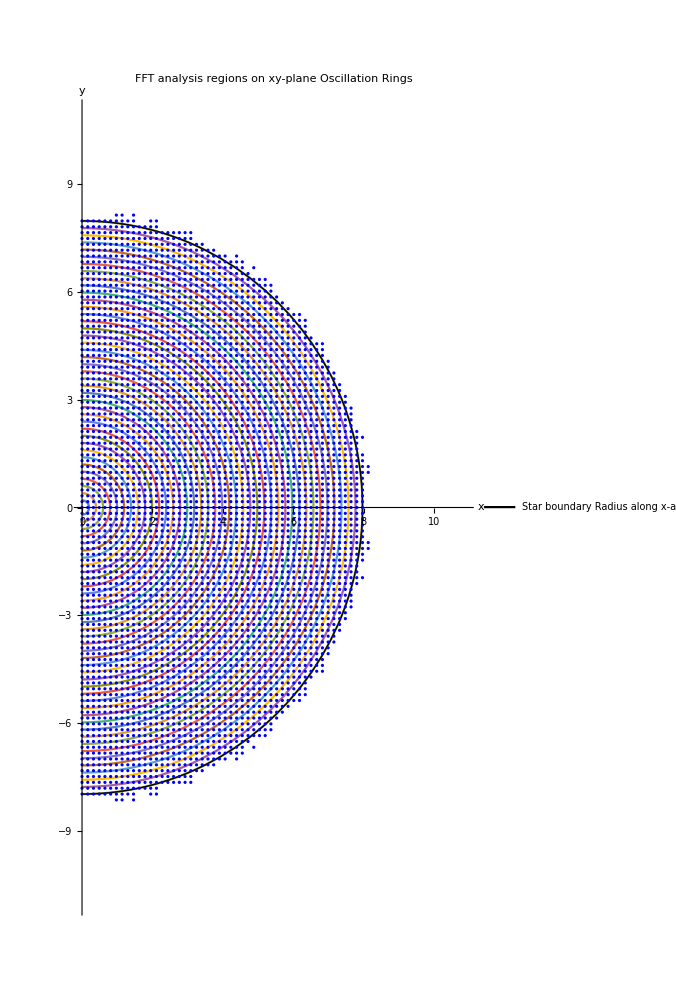

```mathematica
(*Oscillation Rings*)
(*Set Up*)
r0xy=0;r1xy=InRXYx/40;r2xy=2*r1xy;r3xy=3*r1xy;r4xy=4*r1xy;r5xy=5*r1xy;r6xy=6*r1xy;r7xy=7*r1xy; 
r8xy=8*r1xy;r9xy=9*r1xy;r10xy=10*r1xy;r11xy=11*r1xy;r12xy=12*r1xy;r13xy=13*r1xy;r14xy=14*r1xy; 
r15xy=15*r1xy;r16xy=16*r1xy;r17xy=17*r1xy;r18xy=18*r1xy;r19xy=19*r1xy;r20xy=20*r1xy;r21xy=21*r1xy;
r22xy=22*r1xy;r23xy=23*r1xy;r24xy=24*r1xy;r25xy=25*r1xy;r26xy=26*r1xy;r27xy=27*r1xy;r28xy=28*r1xy;
r29xy=29*r1xy;r30xy=30*r1xy;r31xy=31*r1xy;r32xy=32*r1xy;r33xy=33*r1xy;r34xy=34*r1xy;r35xy=35*r1xy;
r36xy=36*r1xy;r37xy=37*r1xy;r38xy=38*r1xy;r39xy=39*r1xy;r40xy=40*r1xy;
(*Visualization*)
StarVisPlot=PolarPlot[{r1xy,r2xy,r3xy,r4xy,r5xy,r6xy,r7xy,r8xy,r9xy,r10xy,r11xy,r12xy,r13xy,r14xy,r15xy,r16xy,r17xy,r18xy,r19xy,r20xy,r21xy,r22xy,r23xy,r24xy,r25xy,r26xy,r27xy,r28xy,r29xy,r30xy,r31xy,r32xy,r33xy,r34xy,r35xy,r36xy,r37xy,r38xy,r39xy,r40xy},{th,-Pi/2,Pi/2},PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}}];
FFTRegVisXY=Show[StarVisPlot,PlotStarBoundInitXY,GraphStarStartXY,AxesLabel-> {"x","y"},PlotLabel->Style[Framed["FFT analysis regions on xy-plane\nOscillation Rings"],11,Black,Background->LightCyan],ImageSize->500]
```

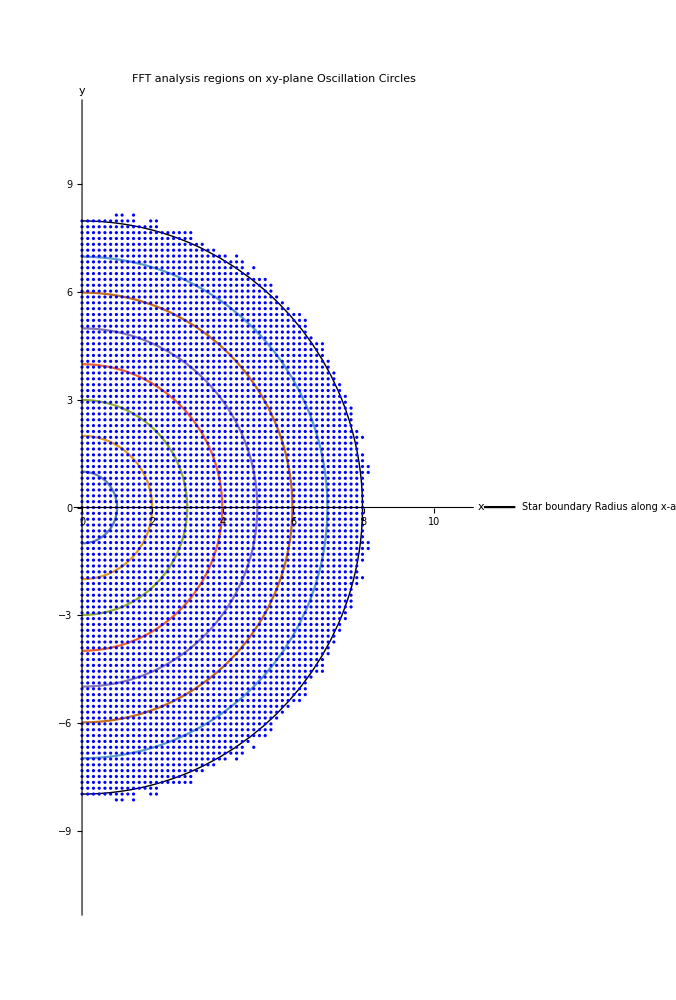

```mathematica
(*Oscillation Circles*)
(*Set Up*)
r0xy=0;r1xy=InRXYx/40;r2xy=2*r1xy;r3xy=3*r1xy;r4xy=4*r1xy;r5xy=5*r1xy;r6xy=6*r1xy;r7xy=7*r1xy; 
r8xy=8*r1xy;r9xy=9*r1xy;r10xy=10*r1xy;r11xy=11*r1xy;r12xy=12*r1xy;r13xy=13*r1xy;r14xy=14*r1xy; 
r15xy=15*r1xy;r16xy=16*r1xy;r17xy=17*r1xy;r18xy=18*r1xy;r19xy=19*r1xy;r20xy=20*r1xy;r21xy=21*r1xy;
r22xy=22*r1xy;r23xy=23*r1xy;r24xy=24*r1xy;r25xy=25*r1xy;r26xy=26*r1xy;r27xy=27*r1xy;r28xy=28*r1xy;
r29xy=29*r1xy;r30xy=30*r1xy;r31xy=31*r1xy;r32xy=32*r1xy;r33xy=33*r1xy;r34xy=34*r1xy;r35xy=35*r1xy;
r36xy=36*r1xy;r37xy=37*r1xy;r38xy=38*r1xy;r39xy=39*r1xy;r40xy=40*r1xy;
OCRadius1=5*r1xy;OCRadius2=10*r1xy;OCRadius3=15*r1xy;OCRadius4=20*r1xy;
OCRadius5=25*r1xy;OCRadius6=30*r1xy;OCRadius7=35*r1xy;
(*Visualization*)
StarVisPlotOscCircles=PolarPlot[{OCRadius1,OCRadius2,OCRadius3,OCRadius4,OCRadius5,OCRadius6,OCRadius7},{th,-Pi/2,Pi/2},PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}}];
FFTRegVisOscCirclesXY=Show[StarVisPlotOscCircles,PlotStarBoundInitXY,GraphStarStartXY,AxesLabel-> {"x","y"},PlotLabel->Style[Framed["FFT analysis regions on xy-plane\nOscillation Circles"],11,Black,Background->LightCyan],ImageSize->500]
```

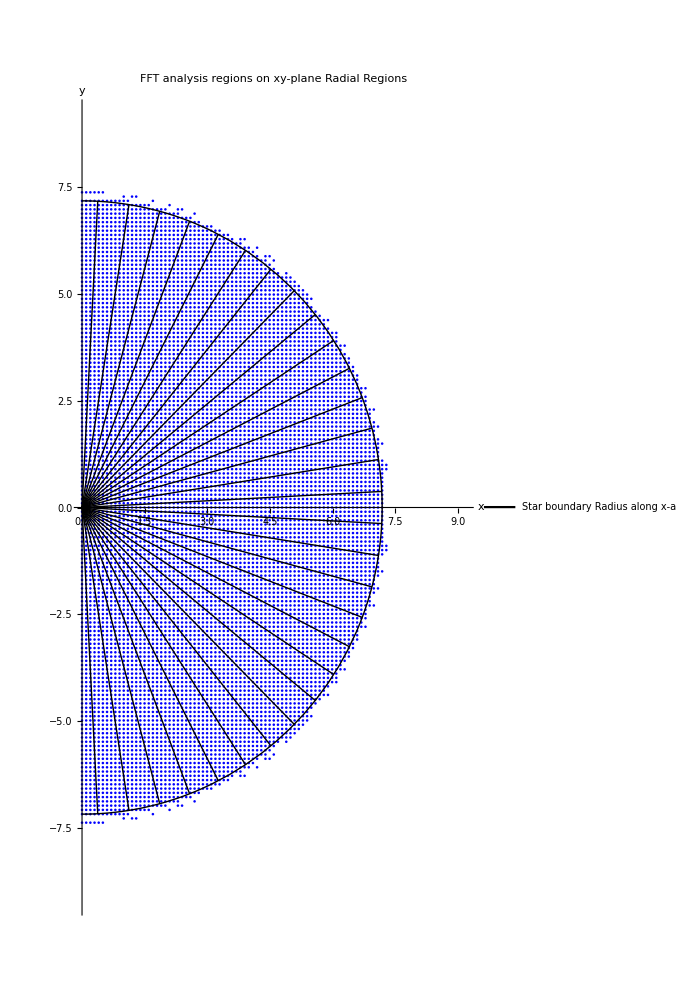

```mathematica
(*Radial Regions*)
(*Set Up*)
PhiPosMax=Pi/2;
PhiPos1=PhiPosMax*(0.5/15);PhiPos2=PhiPosMax*(1.5/15);PhiPos3=PhiPosMax*(2.5/15);PhiPos4=PhiPosMax*(3.5/15);PhiPos5=PhiPosMax*(4.5/15);
PhiPos6=PhiPosMax*(5.5/15);PhiPos7=PhiPosMax*(6.5/15);PhiPos8=PhiPosMax*(7.5/15);PhiPos9=PhiPosMax*(8.5/15);PhiPos10=PhiPosMax*(9.5/15);
PhiPos11=PhiPosMax*(10.5/15);PhiPos12=PhiPosMax*(11.5/15);PhiPos13=PhiPosMax*(12.5/15);PhiPos14=PhiPosMax*(13.5/15);
PhiPos15=PhiPosMax*(14.5/15);
PhiNegMax=-Pi/2;
PhiNeg1=PhiNegMax*(0.5/15);PhiNeg2=PhiNegMax*(1.5/15);PhiNeg3=PhiNegMax*(2.5/15);PhiNeg4=PhiNegMax*(3.5/15);PhiNeg5=PhiNegMax*(4.5/15);
PhiNeg6=PhiNegMax*(5.5/15);PhiNeg7=PhiNegMax*(6.5/15);PhiNeg8=PhiNegMax*(7.5/15);PhiNeg9=PhiNegMax*(8.5/15);PhiNeg10=PhiNegMax*(9.5/15);
PhiNeg11=PhiNegMax*(10.5/15);PhiNeg12=PhiNegMax*(11.5/15);PhiNeg13=PhiNegMax*(12.5/15);PhiNeg14=PhiNegMax*(13.5/15);
PhiNeg15=PhiNegMax*(14.5/15);
(*Visualization*)
OriginPointRPXY:={0,0};
EndPointXYRPos1:={InRXYx*Cos[PhiPos1],InRXYx*Sin[PhiPos1]};
LinesegmentXYRPos1=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos1}]}];
HighLightedLinesegmentXYRPos1=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos1}]}];
EndPointXYRPos2:={InRXYx*Cos[PhiPos2],InRXYx*Sin[PhiPos2]};
LinesegmentXYRPos2=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos2}]}];
HighLightedLinesegmentXYRPos2=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos2}]}];
EndPointXYRPos3:={InRXYx*Cos[PhiPos3],InRXYx*Sin[PhiPos3]};
LinesegmentXYRPos3=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos3}]}];
HighLightedLinesegmentXYRPos3=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos3}]}];
EndPointXYRPos4:={InRXYx*Cos[PhiPos4],InRXYx*Sin[PhiPos4]};
LinesegmentXYRPos4=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos4}]}];
HighLightedLinesegmentXYRPos4=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos4}]}];
EndPointXYRPos5:={InRXYx*Cos[PhiPos5],InRXYx*Sin[PhiPos5]};
LinesegmentXYRPos5=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos5}]}];
HighLightedLinesegmentXYRPos5=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos5}]}];
EndPointXYRPos6:={InRXYx*Cos[PhiPos6],InRXYx*Sin[PhiPos6]};
LinesegmentXYRPos6=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos6}]}];
HighLightedLinesegmentXYRPos6=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos6}]}];
EndPointXYRPos7:={InRXYx*Cos[PhiPos7],InRXYx*Sin[PhiPos7]};
LinesegmentXYRPos7=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos7}]}];
HighLightedLinesegmentXYRPos7=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos7}]}];
EndPointXYRPos8:={InRXYx*Cos[PhiPos8],InRXYx*Sin[PhiPos8]};
LinesegmentXYRPos8=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos8}]}];
HighLightedLinesegmentXYRPos8=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos8}]}];
EndPointXYRPos9:={InRXYx*Cos[PhiPos9],InRXYx*Sin[PhiPos9]};
LinesegmentXYRPos9=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos9}]}];
HighLightedLinesegmentXYRPos9=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos9}]}];
EndPointXYRPos10:={InRXYx*Cos[PhiPos10],InRXYx*Sin[PhiPos10]};
LinesegmentXYRPos10=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos10}]}];
HighLightedLinesegmentXYRPos10=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos10}]}];
EndPointXYRPos11:={InRXYx*Cos[PhiPos11],InRXYx*Sin[PhiPos11]};
LinesegmentXYRPos11=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos11}]}];
HighLightedLinesegmentXYRPos11=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos11}]}];
EndPointXYRPos12:={InRXYx*Cos[PhiPos12],InRXYx*Sin[PhiPos12]};
LinesegmentXYRPos12=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos12}]}];
HighLightedLinesegmentXYRPos12=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos12}]}];
EndPointXYRPos13:={InRXYx*Cos[PhiPos13],InRXYx*Sin[PhiPos13]};
LinesegmentXYRPos13=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos13}]}];
HighLightedLinesegmentXYRPos13=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos13}]}];
EndPointXYRPos14:={InRXYx*Cos[PhiPos14],InRXYx*Sin[PhiPos14]};
LinesegmentXYRPos14=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos14}]}];
HighLightedLinesegmentXYRPos14=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos14}]}];
EndPointXYRPos15:={InRXYx*Cos[PhiPos15],InRXYx*Sin[PhiPos15]};
LinesegmentXYRPos15=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRPos15}]}];
HighLightedLinesegmentXYRPos15=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRPos15}]}];
EndPointXYRNeg1:={InRXYx*Cos[PhiNeg1],InRXYx*Sin[PhiNeg1]};
LinesegmentXYRNeg1=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg1}]}];
HighLightedLinesegmentXYRNeg1=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg1}]}];
EndPointXYRNeg2:={InRXYx*Cos[PhiNeg2],InRXYx*Sin[PhiNeg2]};
LinesegmentXYRNeg2=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg2}]}];
HighLightedLinesegmentXYRNeg2=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg2}]}];
EndPointXYRNeg3:={InRXYx*Cos[PhiNeg3],InRXYx*Sin[PhiNeg3]};
LinesegmentXYRNeg3=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg3}]}];
HighLightedLinesegmentXYRNeg3=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg3}]}];
EndPointXYRNeg4:={InRXYx*Cos[PhiNeg4],InRXYx*Sin[PhiNeg4]};
LinesegmentXYRNeg4=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg4}]}];
HighLightedLinesegmentXYRNeg4=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg4}]}];
EndPointXYRNeg5:={InRXYx*Cos[PhiNeg5],InRXYx*Sin[PhiNeg5]};
LinesegmentXYRNeg5=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg5}]}];
HighLightedLinesegmentXYRNeg5=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg5}]}];
EndPointXYRNeg6:={InRXYx*Cos[PhiNeg6],InRXYx*Sin[PhiNeg6]};
LinesegmentXYRNeg6=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg6}]}];
HighLightedLinesegmentXYRNeg6=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg6}]}];
EndPointXYRNeg7:={InRXYx*Cos[PhiNeg7],InRXYx*Sin[PhiNeg7]};
LinesegmentXYRNeg7=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg7}]}];
HighLightedLinesegmentXYRNeg7=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg7}]}];
EndPointXYRNeg8:={InRXYx*Cos[PhiNeg8],InRXYx*Sin[PhiNeg8]};
LinesegmentXYRNeg8=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg8}]}];
HighLightedLinesegmentXYRNeg8=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg8}]}];
EndPointXYRNeg9:={InRXYx*Cos[PhiNeg9],InRXYx*Sin[PhiNeg9]};
LinesegmentXYRNeg9=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg9}]}];
HighLightedLinesegmentXYRNeg9=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg9}]}];
EndPointXYRNeg10:={InRXYx*Cos[PhiNeg10],InRXYx*Sin[PhiNeg10]};
LinesegmentXYRNeg10=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg10}]}];
HighLightedLinesegmentXYRNeg10=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg10}]}];
EndPointXYRNeg11:={InRXYx*Cos[PhiNeg11],InRXYx*Sin[PhiNeg11]};
LinesegmentXYRNeg11=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg11}]}];
HighLightedLinesegmentXYRNeg11=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg11}]}];
EndPointXYRNeg12:={InRXYx*Cos[PhiNeg12],InRXYx*Sin[PhiNeg12]};
LinesegmentXYRNeg12=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg12}]}];
HighLightedLinesegmentXYRNeg12=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg12}]}];
EndPointXYRNeg13:={InRXYx*Cos[PhiNeg13],InRXYx*Sin[PhiNeg13]};
LinesegmentXYRNeg13=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg13}]}];
HighLightedLinesegmentXYRNeg13=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg13}]}];
EndPointXYRNeg14:={InRXYx*Cos[PhiNeg14],InRXYx*Sin[PhiNeg14]};
LinesegmentXYRNeg14=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg14}]}];
HighLightedLinesegmentXYRNeg14=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg14}]}];
EndPointXYRNeg15:={InRXYx*Cos[PhiNeg15],InRXYx*Sin[PhiNeg15]};
LinesegmentXYRNeg15=Graphics[{RGBColor[0,0,0],Line[{OriginPointRPXY,EndPointXYRNeg15}]}];
HighLightedLinesegmentXYRNeg15=Graphics[{RGBColor[2,0,0],Line[{OriginPointRPXY,EndPointXYRNeg15}]}];
FFTRadRegVisXY=Show[GraphStarStartXY,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,PlotLabel->Style[Framed["FFT analysis regions on xy-plane\nRadial Regions"],11,Black,Background->LightCyan],ImageSize->500]
```

Setting The Oscillation Rings, Circles And Radial Regions.

#### Oscillation Rings (Without Metric And Spherical Harmonic Components)

```mathematica
(*Setting The Boundaries Of The Oscillation Rings*)
r0xyOR=0;r1xyOR=InRXYx/40;r2xyOR=2*r1xyOR;r3xyOR=3*r1xyOR; r4xyOR=4*r1xyOR; r5xyOR=5*r1xyOR; r6xyOR=6*r1xyOR; r7xyOR=7*r1xyOR; 
r8xyOR=8*r1xyOR; r9xyOR=9*r1xyOR; r10xyOR=10*r1xyOR; r11xyOR=11*r1xyOR; r12xyOR=12*r1xyOR; r13xyOR=13*r1xyOR; r14xyOR=14*r1xyOR; 
r15xyOR=15*r1xyOR; r16xyOR=16*r1xyOR; r17xyOR=17*r1xyOR; r18xyOR=18*r1xyOR; r19xyOR=19*r1xyOR; r20xyOR=20*r1xyOR; r21xyOR=21*r1xyOR;
r22xyOR=22*r1xyOR;r23xyOR=23*r1xyOR;r24xyOR=24*r1xyOR;r25xyOR=25*r1xyOR;r26xyOR=26*r1xyOR;r27xyOR=27*r1xyOR;r28xyOR=28*r1xyOR;
r29xyOR=29*r1xyOR;r30xyOR=30*r1xyOR;r31xyOR=31*r1xyOR;r32xyOR=32*r1xyOR;r33xyOR=33*r1xyOR;r34xyOR=34*r1xyOR;r35xyOR=35*r1xyOR;
r36xyOR=36*r1xyOR;r37xyOR=37*r1xyOR;r38xyOR=38*r1xyOR;r39xyOR=39*r1xyOR;r40xyOR=40*r1xyOR;

(*Locate The Points Of The Oscillation Ring Of Interest*)
EmPos=2;EmNeg=-2;
ExpEmPosOmegaOR=Table[Exp[I*(-EmPos*OmegaNS)*l*ItTimeStepSolMas2d],{l,0,FinalItSampleStep2d,DatAnItStep2d}];
ExpEmNegOmegaOR=Table[Exp[I*(-EmNeg*OmegaNS)*m*ItTimeStepSolMas2d],{m,0,FinalItSampleStep2d,DatAnItStep2d}];
OscRing1XY={};OscRing1XYGPExpEmPosPhi={};OscRing1XYGPExpEmNegPhi={};
OscRing2XY={};OscRing2XYGPExpEmPosPhi={};OscRing2XYGPExpEmNegPhi={};
OscRing3XY={};OscRing3XYGPExpEmPosPhi={};OscRing3XYGPExpEmNegPhi={};
OscRing4XY={};OscRing4XYGPExpEmPosPhi={};OscRing4XYGPExpEmNegPhi={};
OscRing5XY={};OscRing5XYGPExpEmPosPhi={};OscRing5XYGPExpEmNegPhi={};
OscRing6XY={};OscRing6XYGPExpEmPosPhi={};OscRing6XYGPExpEmNegPhi={};
OscRing7XY={};OscRing7XYGPExpEmPosPhi={};OscRing7XYGPExpEmNegPhi={};
xmin=InvCoordXYx[0];xmax=DimXYx;
ymin=(*InvCoordXYy[0]*)1;ymax=DimXYy;
nORx=1;nORy=1;
For[x=xmin,x≤ xmax,x=x+nORx,
For[y=ymin,y≤  ymax,y=y+nORy,
ORCoordx=CoordXYx[x];ORCoordy=CoordXYy[y];
PointDistXY=Sqrt[(ORCoordx^2)+(ORCoordy^2)];
Which[
ORCoordx≠0,PhiOR=ArcTan[(ORCoordy/ORCoordx)],
ORCoordx==0&&Sign[ORCoordy]==-1,PhiOR=-(Pi/2),
ORCoordx==0&&Sign[ORCoordy]==1,PhiOR=(Pi/2),
ORCoordx==0&&ORCoordy==0,PhiOR=0
];
ExpEmPosPhiOR=Exp[I*EmPos*PhiOR];
ExpEmNegPhiOR=Exp[I*EmNeg*PhiOR];
(*OscRing 1*)
If[PointDistXY>r5xyOR&&PointDistXY<r6xyOR ,
AppendTo[OscRing1XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing1XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing1XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 2*)
If[PointDistXY>r10xyOR&&PointDistXY<r11xyOR ,
AppendTo[OscRing2XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing2XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing2XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 3*)
If[PointDistXY>r15xyOR&&PointDistXY<r16xyOR ,
AppendTo[OscRing3XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing3XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing3XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 4*)
If[PointDistXY>r20xyOR&&PointDistXY<r21xyOR ,
AppendTo[OscRing4XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing4XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing4XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 5*)
If[PointDistXY>r25xyOR&&PointDistXY<r26xyOR ,
AppendTo[OscRing5XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing5XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing5XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 6*)
If[PointDistXY>r30xyOR&&PointDistXY<r31xyOR ,
AppendTo[OscRing6XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing6XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing6XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 7*)
If[PointDistXY>r35xyOR&&PointDistXY<r36xyOR ,
AppendTo[OscRing7XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing7XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing7XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
Label[end];
  ];
  ];

(*OscRing 1*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing1XYGPExpEmPosPhi.m",OscRing1XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing1XYGPExpEmNegPhi.m",OscRing1XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing1XY.m",OscRing1XY];
(*OscRing 2*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing2XYGPExpEmPosPhi.m",OscRing2XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing2XYGPExpEmNegPhi.m",OscRing2XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing2XY.m",OscRing2XY];
(*OscRing 3*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing3XYGPExpEmPosPhi.m",OscRing3XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing3XYGPExpEmNegPhi.m",OscRing3XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing3XY.m",OscRing3XY];
(*OscRing 4*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing4XYGPExpEmPosPhi.m",OscRing4XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing4XYGPExpEmNegPhi.m",OscRing4XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing4XY.m",OscRing4XY];
(*OscRing 5*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing5XYGPExpEmPosPhi.m",OscRing5XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing5XYGPExpEmNegPhi.m",OscRing5XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing5XY.m",OscRing5XY];
(*OscRing 6*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing6XYGPExpEmPosPhi.m",OscRing6XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing6XYGPExpEmNegPhi.m",OscRing6XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing6XY.m",OscRing6XY];
(*OscRing 7*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing7XYGPExpEmPosPhi.m",OscRing7XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing7XYGPExpEmNegPhi.m",OscRing7XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[General]<>"/"<>"OscRing7XY.m",OscRing7XY];

(*Plots Of Oscillation Rings*)
StarVisPlotOscRings=PolarPlot[{r1xyOR,r2xyOR,r3xyOR,r4xyOR,r5xyOR,r6xyOR,r7xyOR,r8xyOR,r9xyOR,r10xyOR,r11xyOR,r12xyOR,r13xyOR,r14xyOR,r15xyOR,r16xyOR,r17xyOR,r18xyOR,r19xyOR,r20xyOR,r21xyOR,r22xyOR,r23xyOR,r24xyOR,r25xyOR,r26xyOR,r27xyOR,r28xyOR,r29xyOR,r30xyOR,r31xyOR,r32xyOR,r33xyOR,r34xyOR,r35xyOR,r36xyOR,r37xyOR,r38xyOR,r39xyOR,r40xyOR},{th,-Pi/2,Pi/2},AxesLabel->{"x","y"},PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}}];
(*OscRing 1*)
GraphOscRing1XY=ListPlot[OscRing1XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing1=PolarPlot[{r5xyOR,r6xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing1=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing1XY,BoundOscRing1,ImageSize-> 500,PlotLabel->"First oscillation ring",LabelStyle->Directive[Black,15]];
(*OscRing 2*)
GraphOscRing2XY=ListPlot[OscRing2XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing2=PolarPlot[{r10xyOR,r11xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing2=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing2XY,BoundOscRing2,ImageSize-> 500,PlotLabel->"Second oscillation ring",LabelStyle->Directive[Black,15]];
(*OscRing 3*)
GraphOscRing3XY=ListPlot[OscRing3XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing3=PolarPlot[{r15xyOR,r16xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing3=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing3XY,BoundOscRing3,ImageSize-> 500,PlotLabel->"Third oscillation ring",LabelStyle->Directive[Black,15]];
(*OscRing 4*)
GraphOscRing4XY=ListPlot[OscRing4XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing4=PolarPlot[{r20xyOR,r21xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing4=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing4XY,BoundOscRing4,ImageSize-> 500,PlotLabel->"Fourth oscillation ring",LabelStyle->Directive[Black,15]];
(*OscRing 5*)
GraphOscRing5XY=ListPlot[OscRing5XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing5=PolarPlot[{r25xyOR,r26xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing5=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing5XY,BoundOscRing5,ImageSize-> 500,PlotLabel->"Fifth oscillation ring",LabelStyle->Directive[Black,15]];
(*OscRing 6*)
GraphOscRing6XY=ListPlot[OscRing6XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing6=PolarPlot[{r30xyOR,r31xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing6=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing6XY,BoundOscRing6,ImageSize-> 500,PlotLabel->"Sixth oscillation ring",LabelStyle->Directive[Black,15]];
(*OscRing 7*)
GraphOscRing7XY=ListPlot[OscRing7XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing7=PolarPlot[{r35xyOR,r36xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing7=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing7XY,BoundOscRing7,ImageSize-> 500,PlotLabel->"Seventh oscillation ring",LabelStyle->Directive[Black,15]];
```

#### Oscillation Rings (With Metric And Spherical Harmonic Components)

```mathematica
(*Setting The Boundaries Of The Oscillation Rings*)
r0xyOR=0;r1xyOR=InRXYx/40;r2xyOR=2*r1xyOR;r3xyOR=3*r1xyOR; r4xyOR=4*r1xyOR; r5xyOR=5*r1xyOR; r6xyOR=6*r1xyOR; r7xyOR=7*r1xyOR; 
r8xyOR=8*r1xyOR; r9xyOR=9*r1xyOR; r10xyOR=10*r1xyOR; r11xyOR=11*r1xyOR; r12xyOR=12*r1xyOR; r13xyOR=13*r1xyOR; r14xyOR=14*r1xyOR; 
r15xyOR=15*r1xyOR; r16xyOR=16*r1xyOR; r17xyOR=17*r1xyOR; r18xyOR=18*r1xyOR; r19xyOR=19*r1xyOR; r20xyOR=20*r1xyOR; r21xyOR=21*r1xyOR;
r22xyOR=22*r1xyOR;r23xyOR=23*r1xyOR;r24xyOR=24*r1xyOR;r25xyOR=25*r1xyOR;r26xyOR=26*r1xyOR;r27xyOR=27*r1xyOR;r28xyOR=28*r1xyOR;
r29xyOR=29*r1xyOR;r30xyOR=30*r1xyOR;r31xyOR=31*r1xyOR;r32xyOR=32*r1xyOR;r33xyOR=33*r1xyOR;r34xyOR=34*r1xyOR;r35xyOR=35*r1xyOR;
r36xyOR=36*r1xyOR;r37xyOR=37*r1xyOR;r38xyOR=38*r1xyOR;r39xyOR=39*r1xyOR;r40xyOR=40*r1xyOR;

(*Locate The Points Of The Oscillation Ring Of Interest*)
EmPos=2;EmNeg=-2;
Ylmpxy[x_,y_]:=Y22pxy[x,y];
Ylmnxy[x_,y_]:=Y22nxy[x,y];
ExpEmPosOmegaOR=Table[Exp[I*(-EmPos*OmegaNS)*l*ItTimeStepSolMas2d],{l,0,FinalItSampleStep2d,DatAnItStep2d}];
ExpEmNegOmegaOR=Table[Exp[I*(-EmNeg*OmegaNS)*m*ItTimeStepSolMas2d],{m,0,FinalItSampleStep2d,DatAnItStep2d}];
OscRing1XY={};OscRing1XYGPExpEmPosPhi={};OscRing1XYGPExpEmNegPhi={};OscRing1XYYlmp={};OscRing1XYYlmn={};
OscRing2XY={};OscRing2XYGPExpEmPosPhi={};OscRing2XYGPExpEmNegPhi={};OscRing2XYYlmp={};OscRing2XYYlmn={};
OscRing3XY={};OscRing3XYGPExpEmPosPhi={};OscRing3XYGPExpEmNegPhi={};OscRing3XYYlmp={};OscRing3XYYlmn={};
OscRing4XY={};OscRing4XYGPExpEmPosPhi={};OscRing4XYGPExpEmNegPhi={};OscRing4XYYlmp={};OscRing4XYYlmn={};
OscRing5XY={};OscRing5XYGPExpEmPosPhi={};OscRing5XYGPExpEmNegPhi={};OscRing5XYYlmp={};OscRing5XYYlmn={};
OscRing6XY={};OscRing6XYGPExpEmPosPhi={};OscRing6XYGPExpEmNegPhi={};OscRing6XYYlmp={};OscRing6XYYlmn={};
OscRing7XY={};OscRing7XYGPExpEmPosPhi={};OscRing7XYGPExpEmNegPhi={};OscRing7XYYlmp={};OscRing7XYYlmn={};
xmin=InvCoordXYx[0];xmax=DimXYx;
ymin=(*InvCoordXYy[0]*)1;ymax=DimXYy;
nORx=1;nORy=1;
For[x=xmin,x≤ xmax,x=x+nORx,
For[y=ymin,y≤  ymax,y=y+nORy,
ORCoordx=CoordXYx[x];ORCoordy=CoordXYy[y];
PointDistXY=Sqrt[(ORCoordx^2)+(ORCoordy^2)];
Which[
ORCoordx≠0,PhiOR=ArcTan[(ORCoordy/ORCoordx)],
ORCoordx==0&&Sign[ORCoordy]==-1,PhiOR=-(Pi/2),
ORCoordx==0&&Sign[ORCoordy]==1,PhiOR=(Pi/2),
ORCoordx==0&&ORCoordy==0,PhiOR=0
];
If[PointDistXY==0,YlmpXY=0,YlmpXY=Ylmpxy[ORCoordx,ORCoordy]];
If[PointDistXY==0,YlmnXY=0,YlmnXY=Ylmnxy[ORCoordx,ORCoordy]];
SqrtDetXY=Sqrt[DetgPerturbedXY[x,y]];
ExpEmPosPhiOR=Exp[I*EmPos*PhiOR];
ExpEmNegPhiOR=Exp[I*EmNeg*PhiOR];
(*OscRing 1*)
If[PointDistXY>r5xyOR&&PointDistXY<r6xyOR ,
AppendTo[OscRing1XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing1XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing1XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing1XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing1XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 2*)
If[PointDistXY>r10xyOR&&PointDistXY<r11xyOR ,
AppendTo[OscRing2XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing2XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing2XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing2XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing2XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 3*)
If[PointDistXY>r15xyOR&&PointDistXY<r16xyOR ,
AppendTo[OscRing3XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing3XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing3XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing3XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing3XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 4*)
If[PointDistXY>r20xyOR&&PointDistXY<r21xyOR ,
AppendTo[OscRing4XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing4XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing4XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing4XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing4XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 5*)
If[PointDistXY>r25xyOR&&PointDistXY<r26xyOR ,
AppendTo[OscRing5XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing5XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing5XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing5XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing5XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 6*)
If[PointDistXY>r30xyOR&&PointDistXY<r31xyOR ,
AppendTo[OscRing6XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing6XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing6XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing6XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing6XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
(*OscRing 7*)
If[PointDistXY>r35xyOR&&PointDistXY<r36xyOR ,
AppendTo[OscRing7XYGPExpEmPosPhi,{x,y,ExpEmPosPhiOR}];
AppendTo[OscRing7XYGPExpEmNegPhi,{x,y,ExpEmNegPhiOR}];
AppendTo[OscRing7XYYlmp,{x,y,YlmpXY,SqrtDetXY}];
AppendTo[OscRing7XYYlmn,{x,y,YlmnXY,SqrtDetXY}];
AppendTo[OscRing7XY,{{ORCoordx,ORCoordy}}];
Goto[end];
];
Label[end];
  ];
  ];

(*OscRing 1*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing1XYGPExpEmPosPhi.m",OscRing1XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing1XYGPExpEmNegPhi.m",OscRing1XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing1XY.m",OscRing1XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing1XYYlmp.m",OscRing1XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing1XYYlmn.m",OscRing1XYYlmn];
(*OscRing 2*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing2XYGPExpEmPosPhi.m",OscRing2XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing2XYGPExpEmNegPhi.m",OscRing2XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing2XY.m",OscRing2XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing2XYYlmp.m",OscRing2XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing2XYYlmn.m",OscRing2XYYlmn];
(*OscRing 3*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing3XYGPExpEmPosPhi.m",OscRing3XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing3XYGPExpEmNegPhi.m",OscRing3XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing3XY.m",OscRing3XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing3XYYlmp.m",OscRing3XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing3XYYlmn.m",OscRing3XYYlmn];
(*OscRing 4*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing4XYGPExpEmPosPhi.m",OscRing4XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing4XYGPExpEmNegPhi.m",OscRing4XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing4XY.m",OscRing4XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing4XYYlmp.m",OscRing4XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing4XYYlmn.m",OscRing4XYYlmn];
(*OscRing 5*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing5XYGPExpEmPosPhi.m",OscRing5XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing5XYGPExpEmNegPhi.m",OscRing5XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing5XY.m",OscRing5XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing5XYYlmp.m",OscRing5XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing5XYYlmn.m",OscRing5XYYlmn];
(*OscRing 6*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing6XYGPExpEmPosPhi.m",OscRing6XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing6XYGPExpEmNegPhi.m",OscRing6XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing6XY.m",OscRing6XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing6XYYlmp.m",OscRing6XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing6XYYlmn.m",OscRing6XYYlmn];
(*OscRing 7*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing7XYGPExpEmPosPhi.m",OscRing7XYGPExpEmPosPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing7XYGPExpEmNegPhi.m",OscRing7XYGPExpEmNegPhi];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing7XY.m",OscRing7XY];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing7XYYlmp.m",OscRing7XYYlmp];
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[General]<>"/"<>"OscRing7XYYlmn.m",OscRing7XYYlmn];

(*Plots Of Oscilation Rings*)
StarVisPlotOscRings=PolarPlot[{r1xyOR,r2xyOR,r3xyOR,r4xyOR,r5xyOR,r6xyOR,r7xyOR,r8xyOR,r9xyOR,r10xyOR,r11xyOR,r12xyOR,r13xyOR,r14xyOR,r15xyOR,r16xyOR,r17xyOR,r18xyOR,r19xyOR,r20xyOR,r21xyOR,r22xyOR,r23xyOR,r24xyOR,r25xyOR,r26xyOR,r27xyOR,r28xyOR,r29xyOR,r30xyOR,r31xyOR,r32xyOR,r33xyOR,r34xyOR,r35xyOR,r36xyOR,r37xyOR,r38xyOR,r39xyOR,r40xyOR},{th,-Pi/2,Pi/2},AxesLabel->{"x","y"},PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}}];
(*OscRing 1*)
GraphOscRing1XY=ListPlot[OscRing1XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing1=PolarPlot[{r5xyOR,r6xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing1=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing1XY,BoundOscRing1,ImageSize-> 500,PlotLabel->"First oscillation ring"];
(*OscRing 2*)
GraphOscRing2XY=ListPlot[OscRing2XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing2=PolarPlot[{r10xyOR,r11xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing2=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing2XY,BoundOscRing2,ImageSize-> 500,PlotLabel->"Second oscillation ring"];
(*OscRing 3*)
GraphOscRing3XY=ListPlot[OscRing3XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing3=PolarPlot[{r15xyOR,r16xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing3=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing3XY,BoundOscRing3,ImageSize-> 500,PlotLabel->"Third oscillation ring"];
(*OscRing 4*)
GraphOscRing4XY=ListPlot[OscRing4XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing4=PolarPlot[{r20xyOR,r21xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing4=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing4XY,BoundOscRing4,ImageSize-> 500,PlotLabel->"Fourth oscillation ring"];
(*OscRing 5*)
GraphOscRing5XY=ListPlot[OscRing5XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing5=PolarPlot[{r25xyOR,r26xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing5=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing5XY,BoundOscRing5,ImageSize-> 500,PlotLabel->"Fifth oscillation ring"];
(*OscRing 6*)
GraphOscRing6XY=ListPlot[OscRing6XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing6=PolarPlot[{r30xyOR,r31xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing6=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing6XY,BoundOscRing6,ImageSize-> 500,PlotLabel->"Sixth oscillation ring"];
(*OscRing 7*)
GraphOscRing7XY=ListPlot[OscRing7XY,PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},PlotStyle->Black,AxesLabel->{"x","y"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
BoundOscRing7=PolarPlot[{r35xyOR,r36xyOR},{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{{Red,Thick},{Red,Thick}}];
PlotOscRing7=Show[StarVisPlotOscRings,PlotStarBoundInitXY,GraphOscRing7XY,BoundOscRing7,ImageSize-> 500,PlotLabel->"Seventh oscillation ring"];
```

#### Radial Regions

```mathematica
(*Setting The Boundaries Of The Radial Regions*)
PhiPosMax=Pi/2;
PhiPos1=PhiPosMax*(0.5/15);PhiPos2=PhiPosMax*(1.5/15);PhiPos3=PhiPosMax*(2.5/15);PhiPos4=PhiPosMax*(3.5/15);PhiPos5=PhiPosMax*(4.5/15);
PhiPos6=PhiPosMax*(5.5/15);PhiPos7=PhiPosMax*(6.5/15);PhiPos8=PhiPosMax*(7.5/15);PhiPos9=PhiPosMax*(8.5/15);PhiPos10=PhiPosMax*(9.5/15);
PhiPos11=PhiPosMax*(10.5/15);PhiPos12=PhiPosMax*(11.5/15);PhiPos13=PhiPosMax*(12.5/15);PhiPos14=PhiPosMax*(13.5/15);
PhiPos15=PhiPosMax*(14.5/15);
PhiNegMax=-Pi/2;
PhiNeg1=PhiNegMax*(0.5/15);PhiNeg2=PhiNegMax*(1.5/15);PhiNeg3=PhiNegMax*(2.5/15);PhiNeg4=PhiNegMax*(3.5/15);PhiNeg5=PhiNegMax*(4.5/15);
PhiNeg6=PhiNegMax*(5.5/15);PhiNeg7=PhiNegMax*(6.5/15);PhiNeg8=PhiNegMax*(7.5/15);PhiNeg9=PhiNegMax*(8.5/15);PhiNeg10=PhiNegMax*(9.5/15);
PhiNeg11=PhiNegMax*(10.5/15);PhiNeg12=PhiNegMax*(11.5/15);PhiNeg13=PhiNegMax*(12.5/15);PhiNeg14=PhiNegMax*(13.5/15);
PhiNeg15=PhiNegMax*(14.5/15);

(*Locate The Points Of The Radial Regions Of Interest*)
RadRegion1XY={};RadRegion2XY={};RadRegion3XY={};RadRegion4XY={};RadRegion5XY={};RadRegion6XY={};RadRegion7XY={};
RadRegionCoord1XY={};RadRegionCoord2XY={};RadRegionCoord3XY={};RadRegionCoord4XY={};RadRegionCoord5XY={};RadRegionCoord6XY={};RadRegionCoord7XY={};
xmin=InvCoordXYx[0];xmax=DimXYx;
ymin=(*InvCoordXYy[0]*)1;ymax=DimXYy;
nRRx=1;nRRy=1;
For[x=xmin,x≤ xmax,x=x+nRRx,
For[y=ymin,y≤  ymax,y=y+nRRy,
RRCoordx=CoordXYx[x];RRCoordy=CoordXYy[y];
PointDistXY=Sqrt[(RRCoordx^2)+(RRCoordy^2)];
If[PointDistXY>InRXYx,Goto[end]];
Which[
RRCoordx≠0,PhiRR=ArcTan[(RRCoordy/RRCoordx)],
RRCoordx==0&&Sign[RRCoordy]==-1,PhiRR=-(Pi/2),
RRCoordx==0&&Sign[RRCoordy]==1,PhiRR=(Pi/2),
RRCoordx==0&&RRCoordy==0,PhiRR=0
];
(*Radial Region 1*)
If[PhiRR>PhiPos13&&PhiRR<PhiPos14 ,
AppendTo[RadRegion1XY,{x,y}];
AppendTo[RadRegionCoord1XY,{RRCoordx,RRCoordy}];
Goto[end];
];
(*Radial Region 2*)
If[PhiRR>PhiPos9&&PhiRR<PhiPos10 ,
AppendTo[RadRegion2XY,{x,y}];
AppendTo[RadRegionCoord2XY,{RRCoordx,RRCoordy}];
Goto[end];
];
(*Radial Region 3*)
If[PhiRR>PhiPos4&&PhiRR<PhiPos5 ,
AppendTo[RadRegion3XY,{x,y}];
AppendTo[RadRegionCoord3XY,{RRCoordx,RRCoordy}];
Goto[end];
];
(*Radial Region 4*)
If[PhiRR>PhiNeg1&&PhiRR<PhiPos1 ,
AppendTo[RadRegion4XY,{x,y}];
AppendTo[RadRegionCoord4XY,{RRCoordx,RRCoordy}];
Goto[end];
];
(*Radial Region 5*)
If[PhiRR>PhiNeg5&&PhiRR<PhiNeg4 ,
AppendTo[RadRegion5XY,{x,y}];
AppendTo[RadRegionCoord5XY,{RRCoordx,RRCoordy}];
Goto[end];
];
(*Radial Region 6*)
If[PhiRR>PhiNeg10&&PhiRR<PhiNeg9 ,
AppendTo[RadRegion6XY,{x,y}];
AppendTo[RadRegionCoord6XY,{RRCoordx,RRCoordy}];
Goto[end];
];
(*Radial Region 7*)
If[PhiRR>PhiNeg14&&PhiRR<PhiNeg13,
AppendTo[RadRegion7XY,{x,y}];
AppendTo[RadRegionCoord7XY,{RRCoordx,RRCoordy}];
Goto[end];
];
Label[end];
  ];
  ];

(*Radial Region 1*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion1XY.m",RadRegion1XY];
(*Radial Region 2*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion2XY.m",RadRegion2XY];
(*Radial Region 3*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion3XY.m",RadRegion3XY];
(*Radial Region 4*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion4XY.m",RadRegion4XY];
(*Radial Region 5*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion5XY.m",RadRegion5XY];
(*Radial Region 6*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion6XY.m",RadRegion6XY];
(*Radial Region 7*)
Export["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[General]<>"/"<>"RadialRegion7XY.m",RadRegion7XY];
```

Creation Of Matrices That Contain Density, Pressure And Velocity Time Series.

#### Oscillation Rings (Without Metric And Spherical Harmonic Components)

```mathematica
DirectoryPlane=NameOfSimulation;
Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

(*Creation Of Matrices That Contain The Density, Pressure And Velocity Time Series*)
If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="Ρ_lm(t)=∑_ring ρ(x,y,t)ⅇ^imϕ/N",Quant4Plane="Ρ_lm(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="P_lm(t)=∑_ring p(x,y,t)ⅇ^imϕ/N",Quant4Plane="P_lm(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="U_lm^x(t)=∑_ring u^x(x,y,t)ⅇ^imϕ/N",Quant4Plane="U_lm^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="U_lm^y(t)=∑_ring u^y(x,y,t)ⅇ^imϕ/N",Quant4Plane="U_lm^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="U_lm^z(t)=∑_ring u^z(x,y,t)ⅇ^imϕ/N",Quant4Plane="U_lm^z(t)"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="δΡ_lm(t)=∑_ring δρ(x,y,t)ⅇ^imϕ/N",Quant4Plane="δΡ_lm(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="δP_lm(t)=(∑δ)_ringp(x,y,t)ⅇ^imϕ/N",Quant4Plane="δP_lm(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="δU_lm^x(t)=(∑δ)_ringu^x(x,y,t)ⅇ^imϕ/N",Quant4Plane="δU_lm^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="δU_lm^y(t)=(∑δ)_ringu^y(x,y,t)ⅇ^imϕ/N",Quant4Plane="δU_lm^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="δU_lm^z(t)=∑_ring δu^z(x,y,t)ⅇ^imϕ/N",Quant4Plane="δU_lm^z(t)"}
];
];

TimeSeriesDataListPlaneXY={};
If[DeltaQ==0,
Which[
QuantityPlane=="rho",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xy",Iteration->l,RefinementLevel->RF]]];
]
];
If[PressureXYChoise==2,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama];
]
];
If[PressureXYChoise==3,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]];
]
];
},
QuantityPlane=="velx",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velx","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="vely",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"vely","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="velz",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velz","xy",Iteration->l,RefinementLevel->RF]]];
]
];
];
If[DeltaQ==1,
Which[
QuantityPlane=="rho",
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
]
];
If[PressureXYChoise==2,
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama-Kapa*(InitialValuesMatrixXY)^Gama];
]
];
If[PressureXYChoise==3,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]-InitialValuesMatrixXY];
]
];
},
QuantityPlane=="velx",
InitialValuesMatrixXY=VelxDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velx","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="vely",
InitialValuesMatrixXY=VelyDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"vely","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="velz",
InitialValuesMatrixXY=VelzDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velz","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
]
];
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationRings/"<>ToString[QuantityPlane]<>"/";(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[QuantityPlane]<>"/";

(*Data Gathering*)
For[m=1,m≤7,m++,

(*Counter For Oscillation Ring Under Study*)
Temp2=PrintTemporary[Style["Current O.S.= "<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

OscRingXYGPExpEmPosPhi=
Import["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/General/OscRing"<>ToString[m]<>"XYGPExpEmPosPhi.m"];
OscRingXYGPExpEmNegPhi=
Import["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/General/OscRing"<>ToString[m]<>"XYGPExpEmNegPhi.m"];

(*Inertial Frame*)
ORimin=1;
ORimax=Dimensions[OscRingXYGPExpEmPosPhi][[1]];
x=OscRingXYGPExpEmPosPhi[[1,1]];
y=OscRingXYGPExpEmPosPhi[[1,2]];
CoordOSX=CoordXYx[x];
CoordOSY=CoordXYy[y];
ExpEmPosPhi=OscRingXYGPExpEmPosPhi[[1,3]];
ExpEmNegPhi=OscRingXYGPExpEmNegPhi[[1,3]];
Which[
QuantityPlane=="rho",
{OscRingExpEmPosPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*ExpEmNegPhi},
QuantityPlane=="press",
{OscRingExpEmPosPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*ExpEmNegPhi},
QuantityPlane=="velx",
{OscRingExpEmPosPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmNegPhi},
QuantityPlane=="vely",
{OscRingExpEmPosPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmNegPhi},
QuantityPlane=="velz",
{OscRingExpEmPosPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmNegPhi}
];

For[i=ORimin+1,i≤  ORimax,i++,
x=OscRingXYGPExpEmPosPhi[[i,1]];
y=OscRingXYGPExpEmPosPhi[[i,2]];
CoordOSX=CoordXYx[x];
CoordOSY=CoordXYy[y];
ExpEmPosPhi=OscRingXYGPExpEmPosPhi[[i,3]];
ExpEmNegPhi=OscRingXYGPExpEmNegPhi[[i,3]];
Which[
QuantityPlane=="rho",
{OscRingExpEmPosPhiDataInert=OscRingExpEmPosPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=OscRingExpEmNegPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*ExpEmNegPhi},
QuantityPlane=="press",
{OscRingExpEmPosPhiDataInert=OscRingExpEmPosPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=OscRingExpEmNegPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*ExpEmNegPhi},
QuantityPlane=="velx",
{OscRingExpEmPosPhiDataInert=OscRingExpEmPosPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=OscRingExpEmNegPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmNegPhi},
QuantityPlane=="vely",
{OscRingExpEmPosPhiDataInert=OscRingExpEmPosPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=OscRingExpEmNegPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmNegPhi},
QuantityPlane=="velz",
{OscRingExpEmPosPhiDataInert=OscRingExpEmPosPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosPhi,
OscRingExpEmNegPhiDataInert=OscRingExpEmNegPhiDataInert+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmNegPhi}
];
];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"ExpEmPosPhiInert"<>ToString[QuantityPlane]<>".m",OscRingExpEmPosPhiDataInert/ORimax];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"ExpEmNegPhiInert"<>ToString[QuantityPlane]<>".m",OscRingExpEmNegPhiDataInert/ORimax];

(*Comoving Frame*)
ORimin=1;
ORimax=Dimensions[OscRingXYGPExpEmPosPhi][[1]];
x=OscRingXYGPExpEmPosPhi[[1,1]];
y=OscRingXYGPExpEmPosPhi[[1,2]];
CoordOSX=CoordXYx[x];
CoordOSY=CoordXYy[y];
ExpEmPosPhi=OscRingXYGPExpEmPosPhi[[1,3]];
ExpEmNegPhi=OscRingXYGPExpEmNegPhi[[1,3]];
Which[
QuantityPlane=="rho",
{OscRingExpEmPosPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="press",
{OscRingExpEmPosPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="velx",
{OscRingExpEmPosPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="vely",
{OscRingExpEmPosPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="velz",
{OscRingExpEmPosPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmNegPhi*ExpEmNegOmegaOR)}
];

For[i=ORimin+1,i≤  ORimax,i++,
x=OscRingXYGPExpEmPosPhi[[i,1]];
y=OscRingXYGPExpEmPosPhi[[i,2]];
CoordOSX=CoordXYx[x];
CoordOSY=CoordXYy[y];
ExpEmPosPhi=OscRingXYGPExpEmPosPhi[[i,3]];
ExpEmNegPhi=OscRingXYGPExpEmNegPhi[[i,3]];
Which[
QuantityPlane=="rho",
{OscRingExpEmPosPhiDataCo=OscRingExpEmPosPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=OscRingExpEmPosPhiDataCoTBS+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=OscRingExpEmNegPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="press",
{OscRingExpEmPosPhiDataCo=OscRingExpEmPosPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=OscRingExpEmPosPhiDataCoTBS+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=OscRingExpEmNegPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="velx",
{OscRingExpEmPosPhiDataCo=OscRingExpEmPosPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=OscRingExpEmPosPhiDataCoTBS+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=OscRingExpEmNegPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="vely",
{OscRingExpEmPosPhiDataCo=OscRingExpEmPosPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=OscRingExpEmPosPhiDataCoTBS+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=OscRingExpEmNegPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmNegPhi*ExpEmNegOmegaOR)},
QuantityPlane=="velz",
{OscRingExpEmPosPhiDataCo=OscRingExpEmPosPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmPosPhi*ExpEmPosOmegaOR),
OscRingExpEmPosPhiDataCoTBS=OscRingExpEmPosPhiDataCoTBS+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*ExpEmPosOmegaOR,
OscRingExpEmNegPhiDataCo=OscRingExpEmNegPhiDataCo+TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel*(ExpEmNegPhi*ExpEmNegOmegaOR)}
];
];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"ExpEmPosPhiCo"<>ToString[QuantityPlane]<>".m",OscRingExpEmPosPhiDataCo/ORimax];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"ExpEmPosPhiCo"<>ToString[QuantityPlane]<>"TBS.m",OscRingExpEmPosPhiDataCoTBS/ORimax];Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"ExpEmNegPhiCo"<>ToString[QuantityPlane]<>".m",OscRingExpEmNegPhiDataCo/ORimax];

NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

#### Oscillation Rings (With Metric And Spherical Harmonic Components)

```mathematica
DirectoryPlane=NameOfSimulation;
Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤1,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

(*Quantity Under Study*)
If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="Ρ_lm(t)=∫∫ρ(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="Ρ_lm(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="P_lm(t)=∫∫p(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="P_lm(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="U_lm^x(t)=∫∫u^x(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="U_lm^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="U_lm^y(t)=∫∫u^y(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="U_lm^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="U_lm^z(t)=∫∫u^z(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="U_lm^z(t)"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="δΡ_lm(t)=∫∫δρ(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δΡ_lm(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="δP_lm(t)=∫∫δp(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δP_lm(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="δU_lm^x(t)=∫∫δu^x(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δU_lm^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="δU_lm^y(t)=∫∫δu^y(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δU_lm^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="δU_lm^z(t)=∫∫δu^z(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δU_lm^z(t)"}
];
];

(*Creation Of Matrices That Contain The Density, Pressure And Velocity Time Series*)
TimeSeriesDataListPlaneXY={};
If[DeltaQ==0,
Which[
QuantityPlane=="rho",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xy",Iteration->l,RefinementLevel->RF]]];
]
];
If[PressureXYChoise==2,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama];
]
];
If[PressureXYChoise==3,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]];
]
];
},
QuantityPlane=="velx",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velx","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="vely",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"vely","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="velz",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velz","xy",Iteration->l,RefinementLevel->RF]]];
]
];
];

If[DeltaQ==1,
Which[
QuantityPlane=="rho",
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
]
];
If[PressureXYChoise==2,
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama-Kapa*(InitialValuesMatrixXY)^Gama];
]
];
If[PressureXYChoise==3,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]-InitialValuesMatrixXY];
]
];
},
QuantityPlane=="velx",
InitialValuesMatrixXY=VelxDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velx","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="vely",
InitialValuesMatrixXY=VelyDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"vely","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="velz",
InitialValuesMatrixXY=VelzDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velz","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
]
];
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationRingsWMASH/"<>ToString[QuantityPlane]<>"/";(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[QuantityPlane]<>"/";

(*Data Gathering*)
For[m=1,m≤7,m++,

(*Counter For Oscillation Ring Under Study*)
Temp2=PrintTemporary[Style["Current O.S.= "<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

ORSurfaceElementXY=XYCoordStepX*XYCoordStepY;
OscRingXYYlmp=Import["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/General/OscRing"<>ToString[m]<>"XYYlmp.m"];
OscRingXYYlmn=Import["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/General/OscRing"<>
ToString[m]<>"XYYlmn.m"];

(*Inertial Frame*)
ORimin=1;
ORimax=Dimensions[OscRingXYYlmp][[1]];
x=OscRingXYYlmp[[1,1]];CoordOSX=CoordXYx[x];YlmpXY=OscRingXYYlmp[[1,3]];SqrtDetXYp=OscRingXYYlmp[[1,4]];
y=OscRingXYYlmp[[1,2]];CoordOSY=CoordXYy[y];YlmnXY=OscRingXYYlmn[[1,3]];SqrtDetXYn=OscRingXYYlmn[[1,4]];
Which[
QuantityPlane=="rho",
{OscRingXYYlmpDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="press",
{OscRingXYYlmpDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velx",
{OscRingXYYlmpDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="vely",
{OscRingXYYlmpDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velz",
{OscRingXYYlmpDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*SqrtDetXYn*ORSurfaceElementXY}
];

For[i=ORimin+1,i≤  ORimax,i++,
x=OscRingXYYlmp[[i,1]];CoordOSX=CoordXYx[x];YlmpXY=OscRingXYYlmp[[i,3]];SqrtDetXYp=OscRingXYYlmp[[i,4]];
y=OscRingXYYlmp[[i,2]];CoordOSY=CoordXYy[y];YlmnXY=OscRingXYYlmn[[i,3]];SqrtDetXYn=OscRingXYYlmn[[i,4]];
Which[
QuantityPlane=="rho",
{OscRingXYYlmpDataInert=OscRingXYYlmpDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=OscRingXYYlmnDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="press",
{OscRingXYYlmpDataInert=OscRingXYYlmpDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=OscRingXYYlmnDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velx",
{OscRingXYYlmpDataInert=OscRingXYYlmpDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=OscRingXYYlmnDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="vely",
{OscRingXYYlmpDataInert=OscRingXYYlmpDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=OscRingXYYlmnDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velz",
{OscRingXYYlmpDataInert=OscRingXYYlmpDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataInert=OscRingXYYlmnDataInert+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*SqrtDetXYn*ORSurfaceElementXY}
];
];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"XYYlmpInert"<>ToString[QuantityPlane]<>".m",OscRingXYYlmpDataInert];Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"XYYlmnInert"<>ToString[QuantityPlane]<>".m",OscRingXYYlmnDataInert];

(*Comoving Frame*)
ORimin=1;
ORimax=Dimensions[OscRingXYYlmp][[1]];
x=OscRingXYYlmp[[1,1]];CoordOSX=CoordXYx[x];YlmpXY=OscRingXYYlmp[[1,3]];SqrtDetXYp=OscRingXYYlmp[[1,4]];
y=OscRingXYYlmp[[1,2]];CoordOSY=CoordXYy[y];YlmnXY=OscRingXYYlmn[[1,3]];SqrtDetXYn=OscRingXYYlmn[[1,4]];
Which[
QuantityPlane=="rho",
{OscRingXYYlmpDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="press",
{OscRingXYYlmpDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velx",
{OscRingXYYlmpDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="vely",
{OscRingXYYlmpDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velz",
{OscRingXYYlmpDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY}
];
For[i=ORimin+1,i≤  ORimax,i++,
x=OscRingXYYlmp[[i,1]];CoordOSX=CoordXYx[x];YlmpXY=OscRingXYYlmp[[i,3]];SqrtDetXYp=OscRingXYYlmp[[i,4]];
y=OscRingXYYlmp[[i,2]];CoordOSY=CoordXYy[y];YlmnXY=OscRingXYYlmn[[i,3]];SqrtDetXYn=OscRingXYYlmn[[i,4]];
Which[
QuantityPlane=="rho",
{OscRingXYYlmpDataCo=OscRingXYYlmpDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=OscRingXYYlmpDataCoTBS+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=OscRingXYYlmnDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvDens*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="press",
{OscRingXYYlmpDataCo=OscRingXYYlmpDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=OscRingXYYlmpDataCoTBS+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=OscRingXYYlmnDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvPress*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velx",
{OscRingXYYlmpDataCo=OscRingXYYlmpDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=OscRingXYYlmpDataCoTBS+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=OscRingXYYlmnDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="vely",
{OscRingXYYlmpDataCo=OscRingXYYlmpDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=OscRingXYYlmpDataCoTBS+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=OscRingXYYlmnDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY},
QuantityPlane=="velz",
{OscRingXYYlmpDataCo=OscRingXYYlmpDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmpXY*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmpDataCoTBS=OscRingXYYlmpDataCoTBS+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*ExpEmPosOmegaOR*SqrtDetXYp*ORSurfaceElementXY,
OscRingXYYlmnDataCo=OscRingXYYlmnDataCo+(TimeSeriesDataListPlaneXY[[1;;,x,y]])*GeoToCGSConvVel*YlmnXY*ExpEmNegOmegaOR*SqrtDetXYn*ORSurfaceElementXY}
];
];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"XYYlmpCo"<>ToString[QuantityPlane]<>".m",OscRingXYYlmpDataCo];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"XYYlmpCo"<>ToString[QuantityPlane]<>"TBS.m",OscRingXYYlmpDataCoTBS];
Export[DataFileDirectory<>"OscRing"<>ToString[m]<>"XYYlmnCo"<>ToString[QuantityPlane]<>".m",OscRingXYYlmnDataCo];

NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

#### Oscillation Radial Regions

```mathematica
DirectoryPlane=NameOfSimulation;
Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

(*Quantity Under Study*)
If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];

(*Creation Of Matrices That Contain The Density, Pressure And Velocity Time Series*)
TimeSeriesDataListPlaneXY={};
If[DeltaQ==0,
Which[
QuantityPlane=="rho",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xy",Iteration->l,RefinementLevel->RF]]];
]
];
If[PressureXYChoise==2,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama];
]
];
If[PressureXYChoise==3,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]];
]
];
},
QuantityPlane=="velx",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velx","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="vely",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"vely","xy",Iteration->l,RefinementLevel->RF]]];
],
QuantityPlane=="velz",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velz","xy",Iteration->l,RefinementLevel->RF]]];
]
];
];
If[DeltaQ==1,
Which[
QuantityPlane=="rho",
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
]
];
If[PressureXYChoise==2,
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama-Kapa*(InitialValuesMatrixXY)^Gama];
]
];
If[PressureXYChoise==3,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]-InitialValuesMatrixXY];
]
];
},
QuantityPlane=="velx",
InitialValuesMatrixXY=VelxDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velx","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="vely",
InitialValuesMatrixXY=VelyDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"vely","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
],
QuantityPlane=="velz",
InitialValuesMatrixXY=VelzDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,
AppendTo[TimeSeriesDataListPlaneXY,ToListOfData[ReadGridFunction[DirectoryPlane,"velz","xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY];
]
];
];

TimeListRRXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];DimTimeListRRXY=Dimensions[TimeListRRXY][[1]];
FreqListRRXY=Table[k*DatHertzConv2d,{k,0,DimTimeListRRXY-1,1}];DimFreqListRRXY=Dimensions[FreqListRRXY][[1]];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/RadialRegions/"<>ToString[QuantityPlane]<>"/";(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[QuantityPlane]<>"/";

(*Data Gathering*)
For[m=1,m≤7,m++,

(*Counter For Region Under Study*)
Temp2=PrintTemporary[Style["Current R.R.= "<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

RadialRegionXY=Import["/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/General/RadialRegion"<>ToString[m]<>"XY.m"];

nRRXY=0;
TimeSeriesGraphsMatrixRadRegionXY={};FFTGraphsMatrixRadRegionXY={};
MeanFFTListRadRegionXY=ConstantArray[0,DimFreqListRRXY];
RRimin=1;RRimax=Dimensions[RadialRegionXY][[1]];

For[i=RRimin+1,i≤  RRimax,i++,

x=RadialRegionXY[[i,1]];CoordRRX=CoordXYx[x];
y=RadialRegionXY[[i,2]];CoordRRY=CoordXYy[y];

Which[
QuantityPlane=="rho",
ListDataRRXY=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvDens;,
QuantityPlane=="press",
ListDataRRXY=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvPress;,
QuantityPlane=="velx",
ListDataRRXY=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel;,
QuantityPlane=="vely",
ListDataRRXY=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel;,
QuantityPlane=="velz",
ListDataRRXY=TimeSeriesDataListPlaneXY[[1;;,x,y]]*GeoToCGSConvVel;
];

AbsFourierListRRXY=2*Abs[Fourier[ListDataRRXY,FourierParameters->{-1, 1}]];
TimeSeriesDataListRRXY=Transpose[{TimeListRRXY,ListDataRRXY}];
FFTDataListRRXY=Transpose[{FreqListRRXY,AbsFourierListRRXY}];

AppendTo[TimeSeriesGraphsMatrixRadRegionXY,ListLinePlot[TimeSeriesDataListRRXY,PlotRange->All]];
AppendTo[FFTGraphsMatrixRadRegionXY,ListLinePlot[FFTDataListRRXY,PlotRange->All]];

nRRXY=nRRXY+1;
MeanFFTListRadRegionXY=MeanFFTListRadRegionXY+AbsFourierListRRXY;
];
Export[DataFileDirectory<>"TimeSeriesGraphsMatrixRadRegion"<>ToString[m]<>"XY"<>ToString[QuantityPlane]<>".m",TimeSeriesGraphsMatrixRadRegionXY];
Export[DataFileDirectory<>"FFTGraphsMatrixRadRegion"<>ToString[m]<>"XY"<>ToString[QuantityPlane]<>".m",FFTGraphsMatrixRadRegionXY];

MeanFFTListRadRegionXY=MeanFFTListRadRegionXY/nRRXY;
Export[DataFileDirectory<>"MeanFFTListRadRegion"<>ToString[m]<>"XY"<>ToString[QuantityPlane]<>".m",MeanFFTListRadRegionXY];

NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

#### Oscillation Circles

```mathematica
DirectoryPlane=NameOfSimulation;
(*Integration Specifics*)
PosEmOCXY=2;NegEmOCXY=-2;
LowPhIntLimOC=-Pi/2;HighPhIntLimOC=Pi/2;IntStepPhOC=Pi/100;

(*Data Gathering*)
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationCircles/"<>ToString[QuantityPlane]<>"/";(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationCircles/"<>ToString[QuantityPlane]<>"/";

(*Creation Of Lists That Contain The Density, Pressure And Velocity Time Series*)
TimeSeriesDataListPosOCXY1={};TimeSeriesDataListPosOCXY2={};TimeSeriesDataListPosOCXY3={};TimeSeriesDataListPosOCXY4={};
TimeSeriesDataListPosOCXY5={};TimeSeriesDataListPosOCXY6={};TimeSeriesDataListPosOCXY7={};
TimeSeriesDataListNegOCXY1={};TimeSeriesDataListNegOCXY2={};TimeSeriesDataListNegOCXY3={};TimeSeriesDataListNegOCXY4={};
TimeSeriesDataListNegOCXY5={};TimeSeriesDataListNegOCXY6={};TimeSeriesDataListNegOCXY7={};

If[DeltaQ==0,
Which[
QuantityPlane=="rho",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
];
];
If[PressureXYChoise==2,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
];
];
If[PressureXYChoise==3,
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]];
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
];
];
},
QuantityPlane=="velx",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
],
QuantityPlane=="vely",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
],
QuantityPlane=="velz",
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
]
];
];

If[DeltaQ==1,
Which[
QuantityPlane=="rho",
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
],
QuantityPlane=="press",
{
If[PressureXYChoise==1,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
];
];
If[PressureXYChoise==2,
InitialValuesMatrixXY=DensDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=Kapa*(ToListOfData[ReadGridFunction[DirectoryPlane,"rho","xy",Iteration->l,RefinementLevel->RF]])^Gama-Kapa*(InitialValuesMatrixXY)^Gama;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
];
];
If[PressureXYChoise==3,
InitialValuesMatrixXY=PressDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,"press","xyz",Iteration->l,RefinementLevel->RF]][[1;;,1;;,CentZ]]-InitialValuesMatrixXY;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
];
];
},
QuantityPlane=="velx",
InitialValuesMatrixXY=VelxDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
],
QuantityPlane=="vely",
InitialValuesMatrixXY=VelyDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
],
QuantityPlane=="velz",
InitialValuesMatrixXY=VelzDataListXYInitUnperturbed;
For[l=0,l≤FinalItSampleStep2d,l=l+DatAnItStep2d,

DataMatrixOCXY=ToListOfData[ReadGridFunction[DirectoryPlane,QuantityPlane,"xy",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixXY;
TableDataMatrixOCXY=Table[DataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}];
InterpFunctionOCXY=ListInterpolation[Table[TableDataMatrixOCXY[[x,y]],{x,1,DimXYx},{y,1,DimXYy}],{{1,DimXYx},{1,DimXYy}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListPosOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*PosEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];

AppendTo[TimeSeriesDataListNegOCXY1,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius1*Cos[Ph]],InvCoordXYy[OCRadius1*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY2,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius2*Cos[Ph]],InvCoordXYy[OCRadius2*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY3,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius3*Cos[Ph]],InvCoordXYy[OCRadius3*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY4,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius4*Cos[Ph]],InvCoordXYy[OCRadius4*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY5,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius5*Cos[Ph]],InvCoordXYy[OCRadius5*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY6,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius6*Cos[Ph]],InvCoordXYy[OCRadius6*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
AppendTo[TimeSeriesDataListNegOCXY7,(1/Pi)*Total[Table[InterpFunctionOCXY[InvCoordXYx[OCRadius7*Cos[Ph]],InvCoordXYy[OCRadius7*Sin[Ph]]]*Exp[I*NegEmOCXY*Ph]*IntStepPhOC,{Ph,LowPhIntLimOC,HighPhIntLimOC,IntStepPhOC}]]];
]
];
];

Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY1"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY1];
Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY2"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY2];
Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY3"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY3];
Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY4"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY4];
Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY5"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY5];
Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY6"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY6];
Export[DataFileDirectory<>"TimeSeriesDataListPosOCXY7"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListPosOCXY7];

Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY1"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY1];
Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY2"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY2];
Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY3"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY3];
Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY4"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY4];
Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY5"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY5];
Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY6"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY6];
Export[DataFileDirectory<>"TimeSeriesDataListNegOCXY7"<>ToString[QuantityPlane]<>".m",TimeSeriesDataListNegOCXY7];

NotebookDelete[Temp1];
];
```

Re-Import Data From Oscilation Rings/Circles/Regions.

#### Oscillation Rings (Without Metric And Spherical Harmonic Components)

```mathematica
DirectoryPlane=NameOfSimulation;
Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="Ρ_lm(t)=∑_ring ρ(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="Ρ_(2, 2)(t)",Quant4PlaneN="Ρ_(2, -2)(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="P_lm(t)=∑_ring p(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="P_(2, 2)(t)",Quant4PlaneN="P_(2, -2)(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="U_lm^x(t)=∑_ring u^x(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="U_(2, 2)^x(t)",Quant4PlaneN="U_(2, -2)^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="U_lm^y(t)=∑_ring u^y(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="U_(2, 2)^y(t)",Quant4PlaneN="U_(2, -2)^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="U_lm^z(t)=∑_ring u^z(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="U_(2, 2)^z(t)",Quant4PlaneN="U_(2, -2)^z(t)"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="δΡ_lm(t)=(∑δ)_ringρ(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="δΡ_(2, 2)(t)",Quant4PlaneN="δΡ_(2, -2)(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="δP_lm(t)=∑_ring δp(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="δP_(2, 2)(t)",Quant4PlaneN="δP_(2, -2)(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="δU_lm^x(t)=∑_ring δu^x(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="δU_(2, 2)^x(t)",Quant4PlaneN="δU_(2, -2)^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="δU_lm^y(t)=∑_ring δu^y(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="δU_(2, 2)^y(t)",Quant4PlaneN="δU_(2, -2)^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="δU_lm^z(t)=∑_ring δu^z(x,y,t)ⅇ^imϕ/N",Quant4PlaneP="δU_(2, 2)^z(t)",Quant4PlaneN="δU_(2, -2)^z(t)"}
];
];

For[l=1,l≤1,l++,

(*Counter For Frame Under Study*)
Temp2=PrintTemporary[Style["Current l="<>ToString[l]<>"",FontSize->16,FontFamily->"Times"]];

Which[
l==1,frame="Inert",
l==2,frame="Co"
];

For[m=1,m≤7,m++,

(*Counter For Oscillation Ring Under Study*)
Temp3=PrintTemporary[Style["Current m="<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

Which[
m==1,OscilationRingNumber="First oscillation ring",
m==2,OscilationRingNumber="Second oscillation ring",
m==3,OscilationRingNumber="Third oscillation ring",
m==4,OscilationRingNumber="Fourth oscillation ring",
m==5,OscilationRingNumber="Fifth oscillation ring",
m==6,OscilationRingNumber="Sixth oscillation ring",
m==7,OscilationRingNumber="Seventh oscillation ring"
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationRings/"<>ToString[QuantityPlane]<>"/";
(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[QuantityPlane]<>"/";
FourierRangeORInit=8;FourierRangeHertz=10000;

(*Oscillation Rings*)
Ring=ToString[m];

(*Positive m*)
PRI1=26;PRF1=30;
PRI2=38;PRF2=42;
PRI3=56;PRF3=64;
PRI4=86;PRF4=92;
PRI5=107;PRF5=110;

(*Negative m*)
NRI1=26;NRF1=30;
NRI2=38;NRF2=42;
NRI3=56;NRF3=64;
NRI4=86;NRF4=92;
NRI5=107;NRF5=110;

If[l==1,Goto[Inertial]];
If[l==2,Goto[Comoving]];

Label[Inertial];

(*Inertial Frame*)

(*Positive m*)
RangeInitORPos1=PRI1;RangeFinalORPos1=PRF1;
RangeInitHertzPosORa=RangeInitORPos1*DatHertzConv2d;RangeFinalHertzPosORa=RangeFinalORPos1*DatHertzConv2d;
RangeInitORPos2=PRI2;RangeFinalORPos2=PRF2;
RangeInitHertzPosORb=RangeInitORPos2*DatHertzConv2d;RangeFinalHertzPosORb=RangeFinalORPos2*DatHertzConv2d;
RangeInitORPos3=PRI3;RangeFinalORPos3=PRF3;
RangeInitHertzPosORc=RangeInitORPos3*DatHertzConv2d;RangeFinalHertzPosORc=RangeFinalORPos3*DatHertzConv2d;
RangeInitORPos4=PRI4;RangeFinalORPos4=PRF4;
RangeInitHertzPosORd=RangeInitORPos4*DatHertzConv2d;RangeFinalHertzPosORd=RangeFinalORPos4*DatHertzConv2d;
RangeInitORPos5=PRI5;RangeFinalORPos5=PRF5;
RangeInitHertzPosORe=RangeInitORPos5*DatHertzConv2d;RangeFinalHertzPosORe=RangeFinalORPos5*DatHertzConv2d;

(*Negative m*)
RangeInitORNeg1=NRI1;RangeFinalORNeg1=NRF1;
RangeInitHertzNegORa=RangeInitORNeg1*DatHertzConv2d;RangeFinalHertzNegORa=RangeFinalORNeg1*DatHertzConv2d;
RangeInitORNeg2=NRI2;RangeFinalORNeg2=NRF2;
RangeInitHertzNegORb=RangeInitORNeg2*DatHertzConv2d;RangeFinalHertzNegORb=RangeFinalORNeg2*DatHertzConv2d;
RangeInitORNeg3=NRI3;RangeFinalORNeg3=NRF3;
RangeInitHertzNegORc=RangeInitORNeg3*DatHertzConv2d;RangeFinalHertzNegORc=RangeFinalORNeg3*DatHertzConv2d;
RangeInitORNeg4=NRI4;RangeFinalORNeg4=NRF4;
RangeInitHertzNegORd=RangeInitORNeg4*DatHertzConv2d;RangeFinalHertzNegORd=RangeFinalORNeg4*DatHertzConv2d;
RangeInitORNeg5=NRI5;RangeFinalORNeg5=NRF5;
RangeInitHertzNegORe=RangeInitORNeg5*DatHertzConv2d;RangeFinalHertzNegORe=RangeFinalORNeg5*DatHertzConv2d;

Goto[ComInertEnd];

Label[Comoving];

(*Comoving Frame*)

(*Positive m*)
RangeInitORPos1=PRI1+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos1=PRF1+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORa=RangeInitORPos1*DatHertzConv2d;RangeFinalHertzPosORa=RangeFinalORPos1*DatHertzConv2d;
RangeInitORPos2=PRI2+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos2=PRF2+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORb=RangeInitORPos2*DatHertzConv2d;RangeFinalHertzPosORb=RangeFinalORPos2*DatHertzConv2d;
RangeInitORPos3=PRI3+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos3=PRF3+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORc=RangeInitORPos3*DatHertzConv2d;RangeFinalHertzPosORc=RangeFinalORPos3*DatHertzConv2d;
RangeInitORPos4=PRI4+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos4=PRF4+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORd=RangeInitORPos4*DatHertzConv2d;RangeFinalHertzPosORd=RangeFinalORPos4*DatHertzConv2d;
RangeInitORPos5=PRI5+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos5=PRF5+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORe=RangeInitORPos5*DatHertzConv2d;RangeFinalHertzPosORe=RangeFinalORPos5*DatHertzConv2d;

(*Negative m*)
RangeInitORNeg1=NRI1-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg1=NRF1-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORa=RangeInitORNeg1*DatHertzConv2d;RangeFinalHertzNegORa=RangeFinalORNeg1*DatHertzConv2d;
RangeInitORNeg2=NRI2-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg2=NRF2-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORb=RangeInitORNeg2*DatHertzConv2d;RangeFinalHertzNegORb=RangeFinalORNeg2*DatHertzConv2d;
RangeInitORNeg3=NRI3-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg3=NRF3-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORc=RangeInitORNeg3*DatHertzConv2d;RangeFinalHertzNegORc=RangeFinalORNeg3*DatHertzConv2d;
RangeInitORNeg4=NRI4-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg4=NRF4-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORd=RangeInitORNeg4*DatHertzConv2d;RangeFinalHertzNegORd=RangeFinalORNeg4*DatHertzConv2d;
RangeInitORNeg5=NRI5-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg5=NRF5-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORe=RangeInitORNeg5*DatHertzConv2d;RangeFinalHertzNegORe=RangeFinalORNeg5*DatHertzConv2d;

Goto[ComInertEnd];

Label[ComInertEnd];

(*Mean Weighted FFT Positive m*)
TimeListSecPosORXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];
FourierRangeMWPosORInit=FourierRangeORInit;FourierRangeMWPosOR=Ceiling[FourierRangeHertz/DatHertzConv2d];IntAmplMWPosOR=200;MaxPosXY=0;
MWFourierListPosOR=Import[DataFileDirectory<>"OscRing"<>ToString[Ring]<>"ExpEmPosPhi"<>ToString[frame]<>""<>ToString[QuantityPlane]<>".m"];
(**)
MWTimeListPosORReal=Transpose[{TimeListSecPosORXY,Re[MWFourierListPosOR]}];
MWTimeListPosORImaginary=Transpose[{TimeListSecPosORXY,Im[MWFourierListPosOR]}];
MWListPlotPosORReal=ListLinePlot[{MWTimeListPosORReal},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,
FrameLabel->{"Time t(s)", "Re("<>Quant4PlaneP<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotPosORImaginary=ListLinePlot[{MWTimeListPosORImaginary},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,FrameLabel->{"Time t(s)", "Im("<>Quant4PlaneP<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotPosOR=GraphicsGrid[{{MWListPlotPosORReal},{MWListPlotPosORImaginary}},ImageSize->{1500,500}];
(**)
MWFFTListPosOR=2*Abs[Fourier[MWFourierListPosOR,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWPosORInit,k≤FourierRangeMWPosOR,k++,If[MWFFTListPosOR[[k]]>MaxPosXY,MaxPosXY=MWFFTListPosOR[[k]];]];
AmplMWPosOR=1.2*MaxPosXY;
MWFFTListPosORa={};MWFFTListPosORb={};
For[k=0,k≤ Dimensions[MWFFTListPosOR][[1]]-1,k++,
AppendTo[MWFFTListPosORa,{k*DatHertzConv2d,MWFFTListPosOR[[k+1]]}];
AppendTo[MWFFTListPosORb,{k,MWFFTListPosOR[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quant2Plane]<>"PosORHertz"<>ToString[frame]<>"m"<>ToString[m]<>".asc",MWFFTListPosORa,"Table"];
Clear[x];
IntMWFourierPosORa[x_]:=Interpolation[MWFFTListPosORa][x];
DerIntMWFourierPosORa[x_]=D[IntMWFourierPosORa[x],x];
MWFFTPlotListPosORa=ListLinePlot[MWFFTListPosORa,PlotRange->{{0,FourierRangeMWPosOR*DatHertzConv2d},{-0.2*AmplMWPosOR,AmplMWPosOR}},
AspectRatio->1/3,Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Mean weighted FFT",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosORa=Plot[{IntMWFourierPosORa[x],IntAmplMWPosOR*DerIntMWFourierPosORa[x]},{x,MWFFTListPosORa[[1,1]],MWFFTListPosORa[[Dimensions[MWFFTListPosORa][[1]],1]]},Frame->True,PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOR*DatHertzConv2d},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLegends->Placed[LineLegend[{"Interpolated\n function of FFT "," Derivative\n function of FFT\n (Amplified)"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,Background->RGBColor[1,1,1,.8]]&)],{{.98,.95},{1,1}}],
FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},LabelStyle->Directive[Black,15]];
MWFFTPlotIntAndIntDerPosORaWeb=Show[MWFFTPlotListPosORa,MWFFTPlotIntAndIntDerPosORa];
Clear[x];
IntMWFourierPosORb[x_]:=Interpolation[MWFFTListPosORb][x];
DerIntMWFourierPosORb[x_]=D[IntMWFourierPosORb[x],x];
MWFFTPlotListPosORb=ListLinePlot[MWFFTListPosORb,PlotRange->{{0,FourierRangeMWPosOR},{-0.2*AmplMWPosOR,AmplMWPosOR}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosORb=Plot[{IntMWFourierPosORb[x],2*DerIntMWFourierPosORb[x]},{x,MWFFTListPosORb[[1,1]],MWFFTListPosORb[[Dimensions[MWFFTListPosORb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOR},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerPosORbWeb=Show[MWFFTPlotListPosORb,MWFFTPlotIntAndIntDerPosORb];

(*Peak 1*)
PosORPeak1DUMax=0;PosORPeak1DUkmax=0;
For[k=RangeInitORPos1,k≤RangeFinalORPos1,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak1DUMax,{PosORPeak1DUMax=IntMWFourierPosORb[k],PosORPeak1DUkmax=k};
];
];
FreqConfigPlotPosORa=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORa,RangeFinalHertzPosORa},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosORPeak1DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORaDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos1,RangeFinalORPos1},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosORPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
PosORPeak2DUMax=0;PosORPeak2DUkmax=0;
For[k=RangeInitORPos2,k≤RangeFinalORPos2,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak2DUMax,{PosORPeak2DUMax=IntMWFourierPosORb[k],PosORPeak2DUkmax=k};
];
];
FreqConfigPlotPosORb=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORb,RangeFinalHertzPosORb},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosORPeak2DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORbDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos2,RangeFinalORPos2},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosORPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
PosORPeak3DUMax=0;PosORPeak3DUkmax=0;
For[k=RangeInitORPos3,k≤RangeFinalORPos3,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak3DUMax,{PosORPeak3DUMax=IntMWFourierPosORb[k],PosORPeak3DUkmax=k};
];
];
FreqConfigPlotPosORc=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORc,RangeFinalHertzPosORc},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosORPeak3DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORcDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos3,RangeFinalORPos3},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosORPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
PosORPeak4DUMax=0;PosORPeak4DUkmax=0;
For[k=RangeInitORPos4,k≤RangeFinalORPos4,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak4DUMax,{PosORPeak4DUMax=IntMWFourierPosORb[k],PosORPeak4DUkmax=k};
];
];
FreqConfigPlotPosORd=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORd,RangeFinalHertzPosORd},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosORPeak4DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORdDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos4,RangeFinalORPos4},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosORPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
PosORPeak5DUMax=0;PosORPeak5DUkmax=0;
For[k=RangeInitORPos5,k≤RangeFinalORPos5,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak5DUMax,{PosORPeak5DUMax=IntMWFourierPosORb[k],PosORPeak5DUkmax=k};
];
];
FreqConfigPlotPosORe=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORe,RangeFinalHertzPosORe},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosORPeak5DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOReDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos5,RangeFinalORPos5},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosORPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksPosORPlot=GraphicsRow[{FreqConfigPlotPosORa,FreqConfigPlotPosORb,FreqConfigPlotPosORc,FreqConfigPlotPosORd},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2000,600}];
CloseUpPicksPosORPlotDU=GraphicsRow[{FreqConfigPlotPosORaDU,FreqConfigPlotPosORbDU,FreqConfigPlotPosORcDU,FreqConfigPlotPosORdDU},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2000,600}];

(*Mean Weighted FFT Negative m*)
TimeListSecNegORXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];
FourierRangeMWNegORInit=FourierRangeORInit;FourierRangeMWNegOR=Ceiling[FourierRangeHertz/DatHertzConv2d];IntAmplMWNegOR=200;MaxNegXY=0;
MWFourierListNegOR=Import[DataFileDirectory<>"OscRing"<>ToString[Ring]<>"ExpEmNegPhi"<>ToString[frame]<>""<>ToString[QuantityPlane]<>".m"];
(**)
MWTimeListNegORReal=Transpose[{TimeListSecNegORXY,Re[MWFourierListNegOR]}];
MWTimeListNegORImaginary=Transpose[{TimeListSecNegORXY,Im[MWFourierListNegOR]}];
MWListPlotNegORReal=ListLinePlot[{MWTimeListNegORReal},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,
FrameLabel->{"Time t(s)", "Re("<>Quant4PlaneN<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotNegORImaginary=ListLinePlot[{MWTimeListNegORImaginary},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,FrameLabel->{"Time t(s)", "Im("<>Quant4PlaneN<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotNegOR=GraphicsGrid[{{MWListPlotNegORReal},{MWListPlotNegORImaginary}},ImageSize->{1500,500}];
(**)
MWFFTListNegOR=2*Abs[Fourier[MWFourierListNegOR,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWNegORInit,k≤FourierRangeMWNegOR,k++,If[MWFFTListNegOR[[k]]>MaxNegXY,MaxNegXY=MWFFTListNegOR[[k]];]];
AmplMWNegOR=1.2*MaxNegXY;
MWFFTListNegORa={};MWFFTListNegORb={};
For[k=0,k≤ Dimensions[MWFFTListNegOR][[1]]-1,k++,
AppendTo[MWFFTListNegORa,{k*DatHertzConv2d,MWFFTListNegOR[[k+1]]}];
AppendTo[MWFFTListNegORb,{k,MWFFTListNegOR[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quant2Plane]<>"NegORHertz"<>ToString[frame]<>"m"<>ToString[m]<>".asc",MWFFTListNegORa,"Table"];
Clear[x];
IntMWFourierNegORa[x_]:=Interpolation[MWFFTListNegORa][x];
DerIntMWFourierNegORa[x_]=D[IntMWFourierNegORa[x],x];
MWFFTPlotListNegORa=ListLinePlot[MWFFTListNegORa,PlotRange->{{0,FourierRangeMWNegOR*DatHertzConv2d},{-0.2*AmplMWNegOR,AmplMWNegOR}},
AspectRatio->1/3,Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNeg]<>" Mean weighted FFT",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegORa=Plot[{IntMWFourierNegORa[x],IntAmplMWNegOR*DerIntMWFourierNegORa[x]},{x,MWFFTListNegORa[[1,1]],MWFFTListNegORa[[Dimensions[MWFFTListNegORa][[1]],1]]},Frame->True,PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOR*DatHertzConv2d},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLegends->Placed[LineLegend[{"Interpolated\n function of FFT "," Derivative\n function of FFT\n (Amplified)"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,Background->RGBColor[1,1,1,.8]]&)],{{.98,.95},{1,1}}],
FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},LabelStyle->Directive[Black,15]];
MWFFTPlotIntAndIntDerNegORaWeb=Show[MWFFTPlotListNegORa,MWFFTPlotIntAndIntDerNegORa];
Clear[x];
IntMWFourierNegORb[x_]:=Interpolation[MWFFTListNegORb][x];
DerIntMWFourierNegORb[x_]=D[IntMWFourierNegORb[x],x];
MWFFTPlotListNegORb=ListLinePlot[MWFFTListNegORb,PlotRange->{{0,FourierRangeMWNegOR},{-0.2*AmplMWNegOR,AmplMWNegOR}},AspectRatio->1/3,
ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNeg]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},
PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegORb=Plot[{IntMWFourierNegORb[x],2*DerIntMWFourierNegORb[x]},{x,MWFFTListNegORb[[1,1]],MWFFTListNegORb[[Dimensions[MWFFTListNegORb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOR},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerNegORbWeb=Show[MWFFTPlotListNegORb,MWFFTPlotIntAndIntDerNegORb];

(*Peak 1*)
NegORPeak1DUMax=0;NegORPeak1DUkmax=0;
For[k=RangeInitORNeg1,k≤RangeFinalORNeg1,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak1DUMax,{NegORPeak1DUMax=IntMWFourierNegORb[k],NegORPeak1DUkmax=k};
];
];
FreqConfigPlotNegORa=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORa,RangeFinalHertzNegORa},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[NegORPeak1DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORaDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg1,RangeFinalORNeg1},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosORPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
NegORPeak2DUMax=0;NegORPeak2DUkmax=0;
For[k=RangeInitORNeg2,k≤RangeFinalORNeg2,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak2DUMax,{NegORPeak2DUMax=IntMWFourierNegORb[k],NegORPeak2DUkmax=k};
];
];
FreqConfigPlotNegORb=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORb,RangeFinalHertzNegORb},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[NegORPeak2DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORbDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg2,RangeFinalORNeg2},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosORPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
NegORPeak3DUMax=0;NegORPeak3DUkmax=0;
For[k=RangeInitORNeg3,k≤RangeFinalORNeg3,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak3DUMax,{NegORPeak3DUMax=IntMWFourierNegORb[k],NegORPeak3DUkmax=k};
];
];
FreqConfigPlotNegORc=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORc,RangeFinalHertzNegORc},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[NegORPeak3DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORcDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg3,RangeFinalORNeg3},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosORPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
NegORPeak4DUMax=0;NegORPeak4DUkmax=0;
For[k=RangeInitORNeg4,k≤RangeFinalORNeg4,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak4DUMax,{NegORPeak4DUMax=IntMWFourierNegORb[k],NegORPeak4DUkmax=k};
];
];
FreqConfigPlotNegORd=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORd,RangeFinalHertzNegORd},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[NegORPeak4DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORdDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg4,RangeFinalORNeg4},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosORPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
NegORPeak5DUMax=0;NegORPeak5DUkmax=0;
For[k=RangeInitORNeg5,k≤RangeFinalORNeg5,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak5DUMax,{NegORPeak5DUMax=IntMWFourierNegORb[k],NegORPeak5DUkmax=k};
];
];
FreqConfigPlotNegORe=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORe,RangeFinalHertzNegORe},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[NegORPeak5DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOReDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg5,RangeFinalORNeg5},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosORPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksNegORPlot=GraphicsRow[{FreqConfigPlotNegORa,FreqConfigPlotNegORb,FreqConfigPlotNegORc,FreqConfigPlotNegORd},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmNeg]<>" Peaks" ,15,Black],ImageSize->{2000,600}];
CloseUpPicksNegORPlotDU=GraphicsRow[{FreqConfigPlotNegORaDU,FreqConfigPlotNegORbDU,FreqConfigPlotNegORcDU,FreqConfigPlotNegORdDU},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmNeg]<>" Peaks" ,15,Black],ImageSize->{2000,600}];

(*Exported Plots*)
Export[WebPageFileDirectory<>"FFTPosmPlotsOscilationRing"<>ToString[m]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",MWFFTPlotIntAndIntDerPosORbWeb];
Export[WebPageFileDirectory<>"FFTNegmPlotsOscilationRing"<>ToString[m]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",MWFFTPlotIntAndIntDerNegORbWeb];
Which[
Ring=="1",PlotOscRing=PlotOscRing1,Ring=="2",PlotOscRing=PlotOscRing2,Ring=="3",PlotOscRing=PlotOscRing3,Ring=="4",PlotOscRing=PlotOscRing4,
Ring=="5",PlotOscRing=PlotOscRing5,Ring=="6",PlotOscRing=PlotOscRing6,Ring=="7",PlotOscRing=PlotOscRing7
];
AnalysisPlotsOscRing=GraphicsRow[{GraphicsGrid[{{PlotOscRing}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWFFTPlotIntAndIntDerPosORaWeb},{MWFFTPlotIntAndIntDerNegORaWeb}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
AnalysisGraphsOscRing=GraphicsRow[{GraphicsGrid[{{PlotOscRing}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWListPlotPosOR},{MWListPlotNegOR}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
CloseUpPicksOscRing=GraphicsColumn[{CloseUpPicksPosORPlot,CloseUpPicksNegORPlot},ImageSize->{2000,1200}];
CloseUpPicksOscRingDU=GraphicsColumn[{CloseUpPicksPosORPlotDU,CloseUpPicksNegORPlotDU},ImageSize->{2000,1200}];
Export[WebPageFileDirectory<>"PlotsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",AnalysisPlotsOscRing];
Export[WebPageFileDirectory<>"PlotsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".eps",AnalysisPlotsOscRing];
Export[WebPageFileDirectory<>"GraphsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",AnalysisGraphsOscRing];
Export[WebPageFileDirectory<>"GraphsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".eps",AnalysisGraphsOscRing];
Export[WebPageFileDirectory<>"GraphsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",AnalysisGraphsOscRing];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",CloseUpPicksOscRing];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".eps",CloseUpPicksOscRing];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationRingDU"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>".jpg",CloseUpPicksOscRingDU];

NotebookDelete[Temp3];
];
NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

#### Positive m Comoving Frame Individual Ring/Quantity Study (Without Metric And Spherical Harmonic Components)

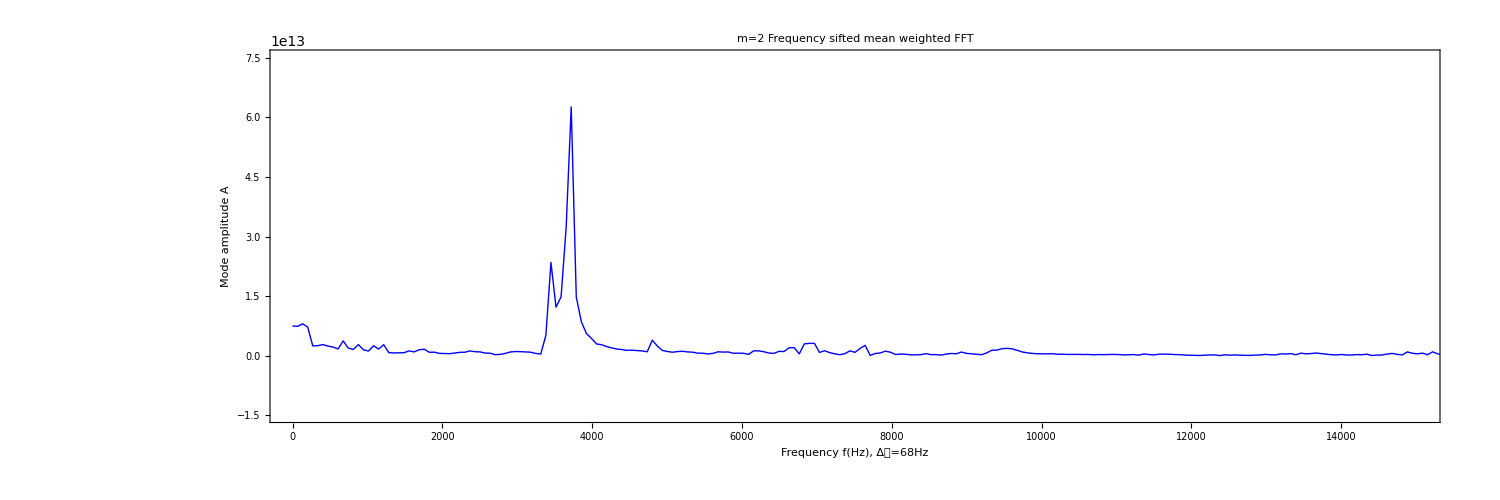

-Graphics-

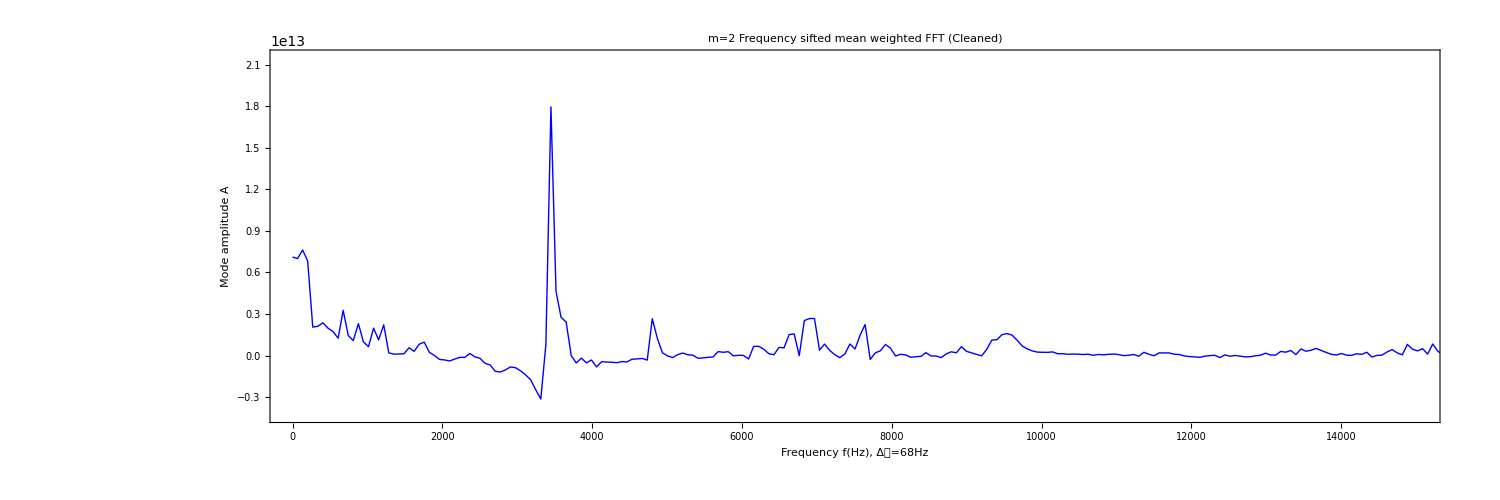

```mathematica
(*Choosing Frame, Quantity Under Study And Oscillation Ring*)
l=2;Q=1;m=7;
(*Frame Choice*)
Which[
l==1,frame="Inert",
l==2,frame="Co"
];
(*Quantity Under Study Choice*)
If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];
(*Oscillation Ring Choice*)
Which[
m==1,OscilationRingNumber="First oscillation ring",
m==2,OscilationRingNumber="Second oscillation ring",
m==3,OscilationRingNumber="Third oscillation ring",
m==4,OscilationRingNumber="Fourth oscillation ring",
m==5,OscilationRingNumber="Fifth oscillation ring",
m==6,OscilationRingNumber="Sixth oscillation ring",
m==7,OscilationRingNumber="Seventh oscillation ring"
];
Ring=ToString[m];
Which[
Ring=="1",PlotOscRing=PlotOscRing1,Ring=="2",PlotOscRing=PlotOscRing2,Ring=="3",PlotOscRing=PlotOscRing3,Ring=="4",PlotOscRing=PlotOscRing4,
Ring=="5",PlotOscRing=PlotOscRing5,Ring=="6",PlotOscRing=PlotOscRing6,Ring=="7",PlotOscRing=PlotOscRing7
];
(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationRings/"<>ToString[QuantityPlane]<>"/";
(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRings/"<>ToString[QuantityPlane]<>"/";
(*Mean Weighted FFTs For Specific l,Q,m*)
FourierRangeORDUInit=5;FourierRangeORHertzFin=15000;
FourierRangeMWORInit=FourierRangeORDUInit;FourierRangeMWORFin=Ceiling[FourierRangeORHertzFin/DatHertzConv2d];
(*Initial Frequency Sifted Mean Weighted FFT*)
MaxMWORXY=0.0;
MWFourierListOR=Import[DataFileDirectory<>"OscRing"<>ToString[Ring]<>"ExpEmPosPhi"<>ToString[frame]<>""<>ToString[QuantityPlane]<>".m"];
MWFFTListOR=Abs[Fourier[MWFourierListOR]];
For[k=FourierRangeMWORInit,k≤FourierRangeMWORFin,k++,If[MWFFTListOR[[k]]>MaxMWORXY,MaxMWORXY=MWFFTListOR[[k]];]];
AmplMWOR=1.2*MaxMWORXY;
MWFFTListORA={};
For[k=0,k≤ Dimensions[MWFFTListOR][[1]]-1,k++,
AppendTo[MWFFTListORA,{k*DatHertzConv2d,MWFFTListOR[[k+1]]}];
];
MWFFTPlotListORA=ListLinePlot[MWFFTListORA,PlotRange->{{0,FourierRangeMWORFin*DatHertzConv2d},{-0.2*AmplMWOR,AmplMWOR}},AspectRatio->1/3,
Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Frequency sifted mean weighted FFT",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]]
(*FFT To Be Subtracted From The Initial FFT*)
MaxMWORXYTBS=0.0;
MWFourierListORTBS=Import[DataFileDirectory<>"OscRing"<>ToString[Ring]<>"ExpEmPosPhi"<>ToString[frame]<>""<>ToString[QuantityPlane]<>"TBS.m"];
MWFFTListORTBS=Abs[Fourier[MWFourierListORTBS]];
For[k=FourierRangeMWORInit,k≤FourierRangeMWORFin,k++,If[MWFFTListORTBS[[k]]>MaxMWORXYTBS,MaxMWORXYTBS=MWFFTListORTBS[[k]];]];
AmplMWORTBS=1.2*MaxMWORXYTBS;
MWFFTListORATBS={};
For[k=0,k≤ Dimensions[MWFFTListORTBS][[1]]-1,k++,
AppendTo[MWFFTListORATBS,{k*DatHertzConv2d,MWFFTListORTBS[[k+1]]}];
];
MWFFTPlotListORATBS=ListLinePlot[MWFFTListORATBS,PlotRange->{{0,FourierRangeMWORFin*DatHertzConv2d},{-0.2*AmplMWORTBS,AmplMWORTBS}},AspectRatio->1/3,
Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Frequncy sifted FFT",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]]
(*Frequency Sifted Mean Weighted FFT (Cleaned)*)
MaxMWORXYCleaned=0;
MWFFTListORCleaned=(MWFFTListOR-(MaxMWORXY/MaxMWORXYTBS)*MWFFTListORTBS);
For[k=FourierRangeMWORInit,k≤FourierRangeMWORFin,k++,If[MWFFTListORCleaned[[k]]>MaxMWORXYCleaned,MaxMWORXYCleaned=MWFFTListORCleaned[[k]];]];
AmplMWORCleaned=1.2*MaxMWORXYCleaned;
MWFFTListORACleaned={};
For[k=0,k≤ Dimensions[MWFFTListORCleaned][[1]]-1,k++,
AppendTo[MWFFTListORACleaned,{k*DatHertzConv2d,MWFFTListORCleaned[[k+1]]}];
];
MWFFTPlotListORACleaned=ListLinePlot[MWFFTListORACleaned,PlotRange->{{0,FourierRangeMWORFin*DatHertzConv2d},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},AspectRatio->1/3,
Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Frequency sifted mean weighted FFT (Cleaned)",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]]
```

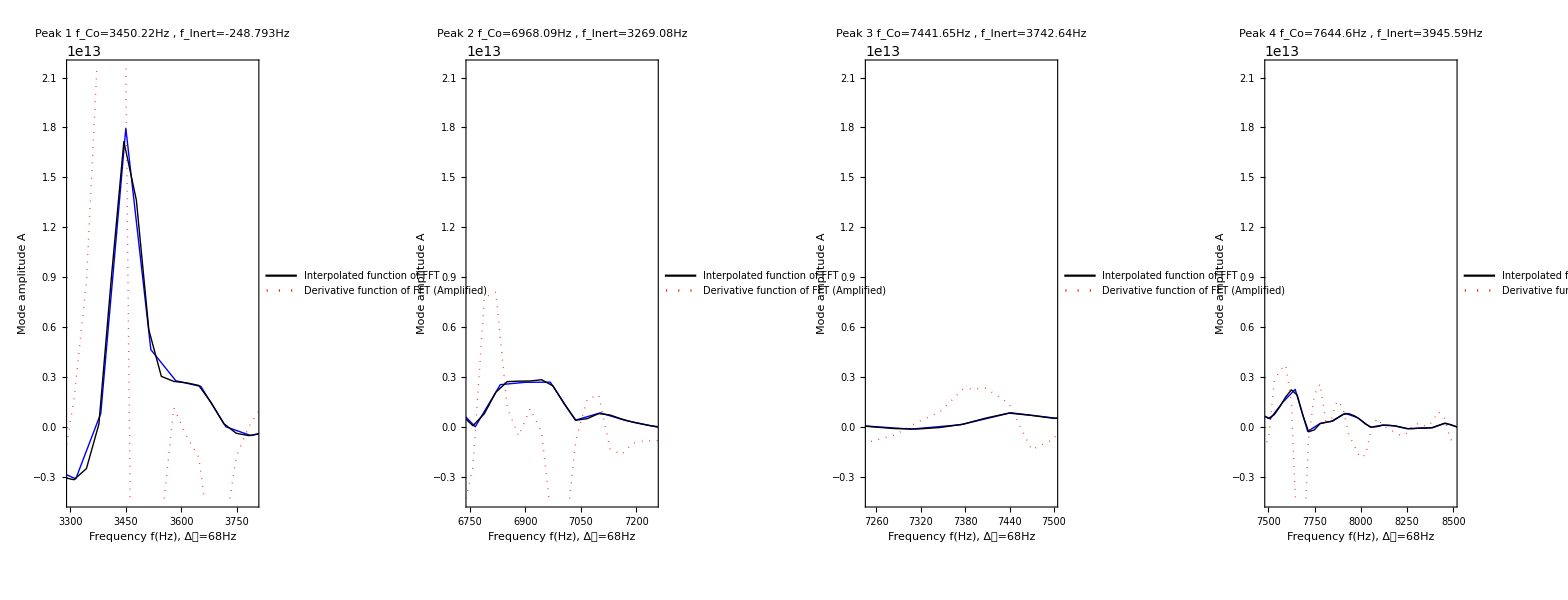

```mathematica
(*Frequency Sifted Mean Weighted FFT (Cleaned) Interpolation/Derivative*)
Clear[x];
IntMWFourierORACleaned[x_]:=Interpolation[MWFFTListORACleaned][x];
DerIntMWFourierORACleaned[x_]=D[IntMWFourierORACleaned[x],x];
MWFFTPlotIntAndIntDerORACleaned=Plot[{IntMWFourierORACleaned[x],200*DerIntMWFourierORACleaned[x]},{x,MWFFTListORACleaned[[1,1]],MWFFTListORACleaned[[Dimensions[MWFFTListORACleaned][[1]],1]]},Frame->True,PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWORFin*DatHertzConv2d},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},PlotLegends->Placed[LineLegend[{"Interpolated\n function of FFT "," Derivative\n function of FFT\n (Amplified)"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,Background->RGBColor[1,1,1,.8]]&)],{{.98,.95},{1,1}}],
FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},LabelStyle->Directive[Black,15]];
MWFFTPlotIntAndIntDerORACleanedWeb=Show[MWFFTPlotListORACleaned,MWFFTPlotIntAndIntDerORACleaned];
AnalysisPlotsOscRingCleaned=GraphicsRow[{GraphicsGrid[{{PlotOscRing}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWFFTPlotListORA},{MWFFTPlotIntAndIntDerORACleanedWeb}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
Export[WebPageFileDirectory<>"PlotsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"Cleaned.jpg",AnalysisPlotsOscRingCleaned];
(*Peak Ranges Hz*)
CORHzI1=3300;CORHzF1=3800;
CORHzI2=6750;CORHzF2=7250;
CORHzI3=7250;CORHzF3=7500;
CORHzI4=7500;CORHzF4=8500;
CORHzI5=5000;CORHzF5=6000;
(*Peak 1*)
ORPeak1HzMax=0;ORPeak1Hzkmax=0;
For[k=Ceiling[CORHzI1/DatHertzConv2d],k≤Ceiling[CORHzF1/DatHertzConv2d],k++,
If[MWFFTListORCleaned[[k]]>ORPeak1HzMax,{ORPeak1HzMax=MWFFTListORCleaned[[k]],ORPeak1Hzkmax=k-1};
];
];
FreqConfigPlotORCleaneda=Show[MWFFTPlotIntAndIntDerORACleanedWeb,PlotRange->{{CORHzI1,CORHzF1},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},PlotLabel->"Peak 1\nf_Co="<>ToString[ORPeak1Hzkmax*DatHertzConv2d]<>"Hz , "<>"f_Inert="<>ToString[(ORPeak1Hzkmax-2*(RotFreqNS/DatHertzConv2d))*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
ORPeak2HzMax=0;ORPeak2Hzkmax=0;
For[k=Ceiling[CORHzI2/DatHertzConv2d],k≤Ceiling[CORHzF2/DatHertzConv2d],k++,
If[MWFFTListORCleaned[[k]]>ORPeak2HzMax,{ORPeak2HzMax=MWFFTListORCleaned[[k]],ORPeak2Hzkmax=k-1};
];
];
FreqConfigPlotORCleanedb=Show[MWFFTPlotIntAndIntDerORACleanedWeb,PlotRange->{{CORHzI2,CORHzF2},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},PlotLabel->"Peak 2\nf_Co="<>ToString[ORPeak2Hzkmax*DatHertzConv2d]<>"Hz , "<>"f_Inert="<>ToString[(ORPeak2Hzkmax-2*(RotFreqNS/DatHertzConv2d))*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
ORPeak3HzMax=0;ORPeak3Hzkmax=0;
For[k=Ceiling[CORHzI3/DatHertzConv2d],k≤Ceiling[CORHzF3/DatHertzConv2d],k++,
If[MWFFTListORCleaned[[k]]>ORPeak3HzMax,{ORPeak3HzMax=MWFFTListORCleaned[[k]],ORPeak3Hzkmax=k-1};
];
];
FreqConfigPlotORCleanedc=Show[MWFFTPlotIntAndIntDerORACleanedWeb,PlotRange->{{CORHzI3,CORHzF3},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},PlotLabel->"Peak 3\nf_Co="<>ToString[ORPeak3Hzkmax*DatHertzConv2d]<>"Hz , "<>"f_Inert="<>ToString[(ORPeak3Hzkmax-2*(RotFreqNS/DatHertzConv2d))*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
ORPeak4HzMax=0;ORPeak4Hzkmax=0;
For[k=Ceiling[CORHzI4/DatHertzConv2d],k≤Ceiling[CORHzF4/DatHertzConv2d],k++,
If[MWFFTListORCleaned[[k]]>ORPeak4HzMax,{ORPeak4HzMax=MWFFTListORCleaned[[k]],ORPeak4Hzkmax=k-1};
];
];
FreqConfigPlotORCleanedd=Show[MWFFTPlotIntAndIntDerORACleanedWeb,PlotRange->{{CORHzI4,CORHzF4},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},PlotLabel->"Peak 4\nf_Co="<>ToString[ORPeak4Hzkmax*DatHertzConv2d]<>"Hz , "<>"f_Inert="<>ToString[(ORPeak4Hzkmax-2*(RotFreqNS/DatHertzConv2d))*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
ORPeak5HzMax=0;ORPeak5Hzkmax=0;
For[k=Ceiling[CORHzI5/DatHertzConv2d],k≤Ceiling[CORHzF5/DatHertzConv2d],k++,
If[MWFFTListORCleaned[[k]]>ORPeak5HzMax,{ORPeak5HzMax=MWFFTListORCleaned[[k]],ORPeak5Hzkmax=k-1};
];
];
FreqConfigPlotORCleanede=Show[MWFFTPlotIntAndIntDerORACleanedWeb,PlotRange->{{CORHzI5,CORHzF5},{-0.2*AmplMWORCleaned,AmplMWORCleaned}},PlotLabel->"Peak 5\nf_Co="<>ToString[ORPeak5Hzkmax*DatHertzConv2d]<>"Hz , "<>"f_Inert="<>ToString[(ORPeak5Hzkmax-2*(RotFreqNS/DatHertzConv2d))*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
(*Close Up Peak Graph*)
CloseUpPicksOscRingCleaned=GraphicsRow[{FreqConfigPlotORCleaneda,FreqConfigPlotORCleanedb,FreqConfigPlotORCleanedc,FreqConfigPlotORCleanedd},PlotLabel->Style[OscilationRingNumber<>"\nComoving frame \n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2200,600}]
Export[WebPageFileDirectory<>"PlotsPeaksOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"Cleaned.jpg",CloseUpPicksOscRingCleaned];
```

#### Oscillation Rings (With Metric And Spherical Harmonic Components)

```mathematica
DirectoryPlane=NameOfSimulation;
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="Ρ_lm(t)=∫∫ρ(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="Ρ_lm(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="P_lm(t)=∫∫p(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="P_lm(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="U_lm^x(t)=∫∫u^x(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="U_lm^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="U_lm^y(t)=∫∫u^y(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="U_lm^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="U_lm^z(t)=∫∫u^z(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="U_lm^z(t)"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="δΡ_lm(t)=∫∫δρ(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δΡ_lm(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="δP_lm(t)=∫∫δp(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δP_lm(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="δU_lm^x(t)=∫∫δu^x(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δU_lm^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="δU_lm^y(t)=∫∫δu^y(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δU_lm^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="δU_lm^z(t)=∫∫δu^z(x,y,t)Y_lm(x,y)ⅆS",Quant4Plane="δU_lm^z(t)"}
];
];

For[l=1,l≤1,l++,

(*Counter For Frame Under Study*)
Temp2=PrintTemporary[Style["Current l="<>ToString[l]<>"",FontSize->16,FontFamily->"Times"]];

Which[
l==1,frame="Inert",
l==2,frame="Co"
];

For[m=1,m≤7,m++,

(*Counter For Oscillation Rings Under Study*)
Temp3=PrintTemporary[Style["Current m="<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

Which[
m==1,OscilationRingNumber="First oscillation ring",
m==2,OscilationRingNumber="Second oscillation ring",
m==3,OscilationRingNumber="Third oscillation ring",
m==4,OscilationRingNumber="Fourth oscillation ring",
m==5,OscilationRingNumber="Fifth oscillation ring",
m==6,OscilationRingNumber="Sixth oscillation ring",
m==7,OscilationRingNumber="Seventh oscillation ring"
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationRingsWMASH/"<>ToString[QuantityPlane]<>"/";
(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationRingsWMASH/"<>ToString[QuantityPlane]<>"/";
FourierRangeORInit=6;FourierRangeHertz=16000;

(*Oscillation Rings*)
Ring=ToString[m];

(*Positive m*)
PRI1=25;PRF1=30;
PRI2=37;PRF2=43;
PRI3=57;PRF3=64;
PRI4=65;PRF4=72;
PRI5=85;PRF5=95;

(*Negative m*)
NRI1=25;NRF1=30;
NRI2=37;NRF2=43;
NRI3=57;NRF3=64;
NRI4=65;NRF4=72;
NRI5=86;NRF5=94;

If[l==1,Goto[Inertial]];
If[l==2,Goto[Comoving]];

Label[Inertial];

(*Inertial Frame*)

(*Positive m*)
RangeInitORPos1=PRI1;RangeFinalORPos1=PRF1;
RangeInitHertzPosORa=RangeInitORPos1*DatHertzConv2d;RangeFinalHertzPosORa=RangeFinalORPos1*DatHertzConv2d;
RangeInitORPos2=PRI2;RangeFinalORPos2=PRF2;
RangeInitHertzPosORb=RangeInitORPos2*DatHertzConv2d;RangeFinalHertzPosORb=RangeFinalORPos2*DatHertzConv2d;
RangeInitORPos3=PRI3;RangeFinalORPos3=PRF3;
RangeInitHertzPosORc=RangeInitORPos3*DatHertzConv2d;RangeFinalHertzPosORc=RangeFinalORPos3*DatHertzConv2d;
RangeInitORPos4=PRI4;RangeFinalORPos4=PRF4;
RangeInitHertzPosORd=RangeInitORPos4*DatHertzConv2d;RangeFinalHertzPosORd=RangeFinalORPos4*DatHertzConv2d;
RangeInitORPos5=PRI5;RangeFinalORPos5=PRF5;
RangeInitHertzPosORe=RangeInitORPos5*DatHertzConv2d;RangeFinalHertzPosORe=RangeFinalORPos5*DatHertzConv2d;

(*Negative m*)
RangeInitORNeg1=NRI1;RangeFinalORNeg1=NRF1;
RangeInitHertzNegORa=RangeInitORNeg1*DatHertzConv2d;RangeFinalHertzNegORa=RangeFinalORNeg1*DatHertzConv2d;
RangeInitORNeg2=NRI2;RangeFinalORNeg2=NRF2;
RangeInitHertzNegORb=RangeInitORNeg2*DatHertzConv2d;RangeFinalHertzNegORb=RangeFinalORNeg2*DatHertzConv2d;
RangeInitORNeg3=NRI3;RangeFinalORNeg3=NRF3;
RangeInitHertzNegORc=RangeInitORNeg3*DatHertzConv2d;RangeFinalHertzNegORc=RangeFinalORNeg3*DatHertzConv2d;
RangeInitORNeg4=NRI4;RangeFinalORNeg4=NRF4;
RangeInitHertzNegORd=RangeInitORNeg4*DatHertzConv2d;RangeFinalHertzNegORd=RangeFinalORNeg4*DatHertzConv2d;
RangeInitORNeg5=NRI5;RangeFinalORNeg5=NRF5;
RangeInitHertzNegORe=RangeInitORNeg5*DatHertzConv2d;RangeFinalHertzNegORe=RangeFinalORNeg5*DatHertzConv2d;

Goto[ComInertEnd];

Label[Comoving];

(*Comoving Frame*)

(*Positive m*)
RangeInitORPos1=PRI1+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos1=PRF1+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORa=RangeInitORPos1*DatHertzConv2d;RangeFinalHertzPosORa=RangeFinalORPos1*DatHertzConv2d;
RangeInitORPos2=PRI2+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos2=PRF2+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORb=RangeInitORPos2*DatHertzConv2d;RangeFinalHertzPosORb=RangeFinalORPos2*DatHertzConv2d;
RangeInitORPos3=PRI3+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos3=PRF3+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORc=RangeInitORPos3*DatHertzConv2d;RangeFinalHertzPosORc=RangeFinalORPos3*DatHertzConv2d;
RangeInitORPos4=PRI4+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos4=PRF4+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORd=RangeInitORPos4*DatHertzConv2d;RangeFinalHertzPosORd=RangeFinalORPos4*DatHertzConv2d;
RangeInitORPos5=PRI5+2*(RotFreqNS/DatHertzConv2d);RangeFinalORPos5=PRF5+2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzPosORe=RangeInitORPos5*DatHertzConv2d;RangeFinalHertzPosORe=RangeFinalORPos5*DatHertzConv2d;

(*Negative m*)
RangeInitORNeg1=NRI1-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg1=NRF1-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORa=RangeInitORNeg1*DatHertzConv2d;RangeFinalHertzNegORa=RangeFinalORNeg1*DatHertzConv2d;
RangeInitORNeg2=NRI2-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg2=NRF2-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORb=RangeInitORNeg2*DatHertzConv2d;RangeFinalHertzNegORb=RangeFinalORNeg2*DatHertzConv2d;
RangeInitORNeg3=NRI3-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg3=NRF3-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORc=RangeInitORNeg3*DatHertzConv2d;RangeFinalHertzNegORc=RangeFinalORNeg3*DatHertzConv2d;
RangeInitORNeg4=NRI4-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg4=NRF4-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORd=RangeInitORNeg4*DatHertzConv2d;RangeFinalHertzNegORd=RangeFinalORNeg4*DatHertzConv2d;
RangeInitORNeg5=NRI5-2*(RotFreqNS/DatHertzConv2d);RangeFinalORNeg5=NRF5-2*(RotFreqNS/DatHertzConv2d);
RangeInitHertzNegORe=RangeInitORNeg5*DatHertzConv2d;RangeFinalHertzNegORe=RangeFinalORNeg5*DatHertzConv2d;

Goto[ComInertEnd];

Label[ComInertEnd];

(*Mean Weighted FFT Positive m*)
TimeListSecPosORXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];
FourierRangeMWPosORInit=FourierRangeORInit;FourierRangeMWPosOR=Ceiling[FourierRangeHertz/DatHertzConv2d];IntAmplMWPosOR=400;MaxPosXY=0;
MWFourierListPosOR=Import[DataFileDirectory<>"OscRing"<>ToString[Ring]<>"XYYlmp"<>ToString[frame]<>""<>ToString[QuantityPlane]<>".m"];
(**)
MWTimeListPosORReal=Transpose[{TimeListSecPosORXY,Re[MWFourierListPosOR]}];
MWTimeListPosORImaginary=Transpose[{TimeListSecPosORXY,Im[MWFourierListPosOR]}];
MWListPlotPosORReal=ListLinePlot[{MWTimeListPosORReal},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Re("<>Quant4Plane<>")"},
PlotStyle->{{Blue,Thick}},AxesStyle->Directive[Black,12]];
MWListPlotPosORImaginary=ListLinePlot[{MWTimeListPosORImaginary},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Im("<>Quant4Plane<>")"},
PlotStyle->{{Blue},{Thick}},AxesStyle->Directive[Black,12]];
MWListPlotPosOR=GraphicsGrid[{{MWListPlotPosORReal},{MWListPlotPosORImaginary}},PlotLabel->Style[Quant3Plane<> "  for  m="<>ToString[EmPos],14,Black],ImageSize->{1500,500}];
(**)
MWFFTListPosOR=2*Abs[Fourier[MWFourierListPosOR,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWPosORInit,k≤FourierRangeMWPosOR,k++,If[MWFFTListPosOR[[k]]>MaxPosXY,MaxPosXY=MWFFTListPosOR[[k]];]];
AmplMWPosOR=1.2*MaxPosXY;
MWFFTListPosORa={};MWFFTListPosORb={};
For[k=0,k≤ Dimensions[MWFFTListPosOR][[1]]-1,k++,
AppendTo[MWFFTListPosORa,{k*DatHertzConv2d,MWFFTListPosOR[[k+1]]}];
AppendTo[MWFFTListPosORb,{k,MWFFTListPosOR[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quant2Plane]<>"PosORHertz"<>ToString[frame]<>"m"<>ToString[m]<>"SpHarm.asc",MWFFTListPosORa,"Table"];
Clear[x];
IntMWFourierPosORa[x_]:=Interpolation[MWFFTListPosORa][x];
DerIntMWFourierPosORa[x_]=D[IntMWFourierPosORa[x],x];
MWFFTPlotListPosORa=ListLinePlot[MWFFTListPosORa,PlotRange->{{0,FourierRangeMWPosOR*DatHertzConv2d},{-0.2*AmplMWPosOR,AmplMWPosOR}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Mean weighted FFT",AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosORa=Plot[{IntMWFourierPosORa[x],IntAmplMWPosOR*DerIntMWFourierPosORa[x]},{x,MWFFTListPosORa[[1,1]],MWFFTListPosORa[[Dimensions[MWFFTListPosORa][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOR*DatHertzConv2d},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerPosORaWeb=Show[MWFFTPlotListPosORa,MWFFTPlotIntAndIntDerPosORa];
Clear[x];
IntMWFourierPosORb[x_]:=Interpolation[MWFFTListPosORb][x];
DerIntMWFourierPosORb[x_]=D[IntMWFourierPosORb[x],x];
MWFFTPlotListPosORb=ListLinePlot[MWFFTListPosORb,PlotRange->{{0,FourierRangeMWPosOR},{-0.2*AmplMWPosOR,AmplMWPosOR}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosORb=Plot[{IntMWFourierPosORb[x],2*DerIntMWFourierPosORb[x]},{x,MWFFTListPosORb[[1,1]],MWFFTListPosORb[[Dimensions[MWFFTListPosORb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOR},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerPosORbWeb=Show[MWFFTPlotListPosORb,MWFFTPlotIntAndIntDerPosORb];

(*Peak 1*)
PosORPeak1DUMax=0;PosORPeak1DUkmax=0;
For[k=RangeInitORPos1,k≤RangeFinalORPos1,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak1DUMax,{PosORPeak1DUMax=IntMWFourierPosORb[k],PosORPeak1DUkmax=k};
];
];
FreqConfigPlotPosORa=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORa,RangeFinalHertzPosORa},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosORPeak1DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORaDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos1,RangeFinalORPos1},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosORPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
PosORPeak2DUMax=0;PosORPeak2DUkmax=0;
For[k=RangeInitORPos2,k≤RangeFinalORPos2,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak2DUMax,{PosORPeak2DUMax=IntMWFourierPosORb[k],PosORPeak2DUkmax=k};
];
];
FreqConfigPlotPosORb=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORb,RangeFinalHertzPosORb},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosORPeak2DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORbDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos2,RangeFinalORPos2},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosORPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
PosORPeak3DUMax=0;PosORPeak3DUkmax=0;
For[k=RangeInitORPos3,k≤RangeFinalORPos3,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak3DUMax,{PosORPeak3DUMax=IntMWFourierPosORb[k],PosORPeak3DUkmax=k};
];
];
FreqConfigPlotPosORc=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORc,RangeFinalHertzPosORc},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosORPeak3DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORcDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos3,RangeFinalORPos3},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosORPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
PosORPeak4DUMax=0;PosORPeak4DUkmax=0;
For[k=RangeInitORPos4,k≤RangeFinalORPos4,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak4DUMax,{PosORPeak4DUMax=IntMWFourierPosORb[k],PosORPeak4DUkmax=k};
];
];
FreqConfigPlotPosORd=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORd,RangeFinalHertzPosORd},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosORPeak4DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosORdDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos4,RangeFinalORPos4},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosORPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
PosORPeak5DUMax=0;PosORPeak5DUkmax=0;
For[k=RangeInitORPos5,k≤RangeFinalORPos5,k=k+0.1,
If[IntMWFourierPosORb[k]>PosORPeak5DUMax,{PosORPeak5DUMax=IntMWFourierPosORb[k],PosORPeak5DUkmax=k};
];
];
FreqConfigPlotPosORe=Show[MWFFTPlotIntAndIntDerPosORaWeb,PlotRange->{{RangeInitHertzPosORe,RangeFinalHertzPosORe},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosORPeak5DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOReDU=Show[MWFFTPlotIntAndIntDerPosORbWeb,PlotRange->{{RangeInitORPos5,RangeFinalORPos5},{-0.2*AmplMWPosOR,AmplMWPosOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosORPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksPosORPlot=GraphicsRow[{FreqConfigPlotPosORa,FreqConfigPlotPosORb,FreqConfigPlotPosORc,FreqConfigPlotPosORd,FreqConfigPlotPosORe},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2200,500}];
CloseUpPicksPosORPlotDU=GraphicsRow[{FreqConfigPlotPosORaDU,FreqConfigPlotPosORbDU,FreqConfigPlotPosORcDU,FreqConfigPlotPosORdDU,FreqConfigPlotPosOReDU},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2200,500}];

(*Mean Weighted FFT Negative m*)
TimeListSecNegORXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];
FourierRangeMWNegORInit=FourierRangeORInit;FourierRangeMWNegOR=Ceiling[FourierRangeHertz/DatHertzConv2d];IntAmplMWNegOR=400;MaxNegXY=0;
MWFourierListNegOR=Import[DataFileDirectory<>"OscRing"<>ToString[Ring]<>"XYYlmn"<>ToString[frame]<>""<>ToString[QuantityPlane]<>".m"];
(**)
MWTimeListNegORReal=Transpose[{TimeListSecNegORXY,Re[MWFourierListNegOR]}];
MWTimeListNegORImaginary=Transpose[{TimeListSecNegORXY,Im[MWFourierListNegOR]}];
MWListPlotNegORReal=ListLinePlot[{MWTimeListNegORReal},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Re("<>Quant4Plane<>")"},
PlotStyle->{{Blue,Thick}},AxesStyle->Directive[Black,12]];
MWListPlotNegORImaginary=ListLinePlot[{MWTimeListNegORImaginary},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Im("<>Quant4Plane<>")"},
PlotStyle->{{Blue,Thick}},AxesStyle->Directive[Black,12]];
MWListPlotNegOR=GraphicsGrid[{{MWListPlotNegORReal},{MWListPlotNegORImaginary}},PlotLabel->Style[Quant3Plane<> "  for  m="<>ToString[EmNeg],14,Black],ImageSize->{1500,500}];
(**)
MWFFTListNegOR=2*Abs[Fourier[MWFourierListNegOR,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWNegORInit,k≤FourierRangeMWNegOR,k++,If[MWFFTListNegOR[[k]]>MaxNegXY,MaxNegXY=MWFFTListNegOR[[k]];]];
AmplMWNegOR=1.2*MaxNegXY;
MWFFTListNegORa={};MWFFTListNegORb={};
For[k=0,k≤ Dimensions[MWFFTListNegOR][[1]]-1,k++,
AppendTo[MWFFTListNegORa,{k*DatHertzConv2d,MWFFTListNegOR[[k+1]]}];
AppendTo[MWFFTListNegORb,{k,MWFFTListNegOR[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quant2Plane]<>"NegORHertz"<>ToString[frame]<>"m"<>ToString[m]<>"SpHarm.asc",MWFFTListNegORa,"Table"];
Clear[x];
IntMWFourierNegORa[x_]:=Interpolation[MWFFTListNegORa][x];
DerIntMWFourierNegORa[x_]=D[IntMWFourierNegORa[x],x];
MWFFTPlotListNegORa=ListLinePlot[MWFFTListNegORa,PlotRange->{{0,FourierRangeMWNegOR*DatHertzConv2d},{-0.2*AmplMWNegOR,AmplMWNegOR}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNeg]<>" Mean weighted FFT",AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegORa=Plot[{IntMWFourierNegORa[x],IntAmplMWNegOR*DerIntMWFourierNegORa[x]},{x,MWFFTListNegORa[[1,1]],MWFFTListNegORa[[Dimensions[MWFFTListNegORa][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOR*DatHertzConv2d},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],
AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerNegORaWeb=Show[MWFFTPlotListNegORa,MWFFTPlotIntAndIntDerNegORa];
Clear[x];
IntMWFourierNegORb[x_]:=Interpolation[MWFFTListNegORb][x];
DerIntMWFourierNegORb[x_]=D[IntMWFourierNegORb[x],x];
MWFFTPlotListNegORb=ListLinePlot[MWFFTListNegORb,PlotRange->{{0,FourierRangeMWNegOR},{-0.2*AmplMWNegOR,AmplMWNegOR}},AspectRatio->1/3,
ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNeg]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},
PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegORb=Plot[{IntMWFourierNegORb[x],2*DerIntMWFourierNegORb[x]},{x,MWFFTListNegORb[[1,1]],MWFFTListNegORb[[Dimensions[MWFFTListNegORb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOR},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerNegORbWeb=Show[MWFFTPlotListNegORb,MWFFTPlotIntAndIntDerNegORb];

(*Peak 1*)
NegORPeak1DUMax=0;NegORPeak1DUkmax=0;
For[k=RangeInitORNeg1,k≤RangeFinalORNeg1,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak1DUMax,{NegORPeak1DUMax=IntMWFourierNegORb[k],NegORPeak1DUkmax=k};
];
];
FreqConfigPlotNegORa=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORa,RangeFinalHertzNegORa},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[NegORPeak1DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORaDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg1,RangeFinalORNeg1},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosORPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
NegORPeak2DUMax=0;NegORPeak2DUkmax=0;
For[k=RangeInitORNeg2,k≤RangeFinalORNeg2,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak2DUMax,{NegORPeak2DUMax=IntMWFourierNegORb[k],NegORPeak2DUkmax=k};
];
];
FreqConfigPlotNegORb=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORb,RangeFinalHertzNegORb},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[NegORPeak2DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORbDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg2,RangeFinalORNeg2},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosORPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
NegORPeak3DUMax=0;NegORPeak3DUkmax=0;
For[k=RangeInitORNeg3,k≤RangeFinalORNeg3,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak3DUMax,{NegORPeak3DUMax=IntMWFourierNegORb[k],NegORPeak3DUkmax=k};
];
];
FreqConfigPlotNegORc=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORc,RangeFinalHertzNegORc},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[NegORPeak3DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORcDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg3,RangeFinalORNeg3},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosORPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
NegORPeak4DUMax=0;NegORPeak4DUkmax=0;
For[k=RangeInitORNeg4,k≤RangeFinalORNeg4,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak4DUMax,{NegORPeak4DUMax=IntMWFourierNegORb[k],NegORPeak4DUkmax=k};
];
];
FreqConfigPlotNegORd=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORd,RangeFinalHertzNegORd},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[NegORPeak4DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegORdDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg4,RangeFinalORNeg4},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosORPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
NegORPeak5DUMax=0;NegORPeak5DUkmax=0;
For[k=RangeInitORNeg5,k≤RangeFinalORNeg5,k=k+0.1,
If[IntMWFourierNegORb[k]>NegORPeak5DUMax,{NegORPeak5DUMax=IntMWFourierNegORb[k],NegORPeak5DUkmax=k};
];
];
FreqConfigPlotNegORe=Show[MWFFTPlotIntAndIntDerNegORaWeb,PlotRange->{{RangeInitHertzNegORe,RangeFinalHertzNegORe},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[NegORPeak5DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOReDU=Show[MWFFTPlotIntAndIntDerNegORbWeb,PlotRange->{{RangeInitORNeg5,RangeFinalORNeg5},{-0.2*AmplMWNegOR,AmplMWNegOR}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosORPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksNegORPlot=GraphicsRow[{FreqConfigPlotNegORa,FreqConfigPlotNegORb,FreqConfigPlotNegORc,FreqConfigPlotNegORd,FreqConfigPlotNegORe},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmNeg]<>" Peaks" ,15,Black],ImageSize->{2200,500}];
CloseUpPicksNegORPlotDU=GraphicsRow[{FreqConfigPlotNegORaDU,FreqConfigPlotNegORbDU,FreqConfigPlotNegORcDU,FreqConfigPlotNegORdDU,FreqConfigPlotNegOReDU},PlotLabel->Style[OscilationRingNumber<>"\n m="<>ToString[EmNeg]<>" Peaks" ,15,Black],ImageSize->{2200,500}];

(*Exported Plots*)
Export[WebPageFileDirectory<>"FFTPosmPlotsOscilationRing"<>ToString[m]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"SpHarm.jpg",MWFFTPlotIntAndIntDerPosORbWeb];
Export[WebPageFileDirectory<>"FFTNegmPlotsOscilationRing"<>ToString[m]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"SpHarm.jpg",MWFFTPlotIntAndIntDerNegORbWeb];
Which[
Ring=="1",PlotOscRing=PlotOscRing1,Ring=="2",PlotOscRing=PlotOscRing2,Ring=="3",PlotOscRing=PlotOscRing3,Ring=="4",PlotOscRing=PlotOscRing4,
Ring=="5",PlotOscRing=PlotOscRing5,Ring=="6",PlotOscRing=PlotOscRing6,Ring=="7",PlotOscRing=PlotOscRing7
];
AnalysisPlotsOscRing=GraphicsRow[{GraphicsGrid[{{PlotOscRing}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWFFTPlotIntAndIntDerPosORaWeb},{MWFFTPlotIntAndIntDerNegORaWeb}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
AnalysisGraphsOscRing=GraphicsRow[{GraphicsGrid[{{PlotOscRing}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWListPlotPosOR},{MWListPlotNegOR}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
CloseUpPicksOscRing=GraphicsColumn[{CloseUpPicksPosORPlot,CloseUpPicksNegORPlot},ImageSize->{2300,1000}];
CloseUpPicksOscRingDU=GraphicsColumn[{CloseUpPicksPosORPlotDU,CloseUpPicksNegORPlotDU},ImageSize->{2300,1000}];
Export[WebPageFileDirectory<>"PlotsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"SpHarm.jpg",AnalysisPlotsOscRing];
Export[WebPageFileDirectory<>"GraphsOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"SpHarm.jpg",AnalysisGraphsOscRing];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationRing"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"SpHarm.jpg",CloseUpPicksOscRing];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationRingDU"<>ToString[Ring]<>""<>ToString[QuantityPlane]<>""<>ToString[frame]<>"SpHarm.jpg",CloseUpPicksOscRingDU];

NotebookDelete[Temp3];
];
NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

#### Radial Regions

```mathematica
DirectoryPlane=NameOfSimulation;
Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

(*Quantity Under Study*)
If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity"}
];
];


For[m=1,m≤ 7,m++,

(*Counter For Radial Region*)
Temp2=PrintTemporary[Style["Current m="<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

(*General*)
PointsRadReg1VisXY=ListPlot[RadRegionCoord1XY];
FFTRadReg1VisXY=Show[PointsRadReg1VisXY,HighLightedLinesegmentXYRPos13,HighLightedLinesegmentXYRPos14,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];
PointsRadReg2VisXY=ListPlot[RadRegionCoord2XY];
FFTRadReg2VisXY=Show[PointsRadReg2VisXY,HighLightedLinesegmentXYRPos9,HighLightedLinesegmentXYRPos10,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];
PointsRadReg3VisXY=ListPlot[RadRegionCoord3XY];
FFTRadReg3VisXY=Show[PointsRadReg3VisXY,HighLightedLinesegmentXYRPos4,HighLightedLinesegmentXYRPos5,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];
PointsRadReg4VisXY=ListPlot[RadRegionCoord4XY];
FFTRadReg4VisXY=Show[PointsRadReg4VisXY,HighLightedLinesegmentXYRPos1,HighLightedLinesegmentXYRNeg1,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];
PointsRadReg5VisXY=ListPlot[RadRegionCoord5XY];
FFTRadReg5VisXY=Show[PointsRadReg5VisXY,HighLightedLinesegmentXYRNeg4,HighLightedLinesegmentXYRNeg5,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];
PointsRadReg6VisXY=ListPlot[RadRegionCoord6XY];
FFTRadReg6VisXY=Show[PointsRadReg6VisXY,HighLightedLinesegmentXYRNeg9,HighLightedLinesegmentXYRNeg10,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];
PointsRadReg7VisXY=ListPlot[RadRegionCoord7XY];
FFTRadReg7VisXY=Show[PointsRadReg7VisXY,HighLightedLinesegmentXYRNeg13,HighLightedLinesegmentXYRNeg14,PlotStarBoundInitXY,LinesegmentXYRPos1,LinesegmentXYRPos2,LinesegmentXYRPos3,LinesegmentXYRPos4,LinesegmentXYRPos5,LinesegmentXYRPos6,LinesegmentXYRPos7,LinesegmentXYRPos8,LinesegmentXYRPos9,LinesegmentXYRPos10,LinesegmentXYRPos11,LinesegmentXYRPos12,LinesegmentXYRPos13,LinesegmentXYRPos14,LinesegmentXYRPos15,LinesegmentXYRNeg1,LinesegmentXYRNeg2,LinesegmentXYRNeg3,LinesegmentXYRNeg4,LinesegmentXYRNeg5,LinesegmentXYRNeg6,LinesegmentXYRNeg7,LinesegmentXYRNeg8,LinesegmentXYRNeg9,LinesegmentXYRNeg10,LinesegmentXYRNeg11,LinesegmentXYRNeg12,LinesegmentXYRNeg13,LinesegmentXYRNeg14,LinesegmentXYRNeg15,PlotRange->{{0,CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},AxesLabel-> {"x","y"},AspectRatio->2,ImageSize->{500,1000}];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/RadialRegions/"<>ToString[QuantityPlane]<>"/";
(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/RadialRegions/"<>ToString[QuantityPlane]<>"/";
FourierRangeRRXYHertzInit=10;FourierRangeRRHertzFin=12000;

(*Importing Data*)
RadRegion=ToString[m];
Which[
RadRegion=="1",
RadRegionPlotXY=FFTRadReg1VisXY,
RadRegion=="2",
RadRegionPlotXY=FFTRadReg2VisXY,
RadRegion=="3",
RadRegionPlotXY=FFTRadReg3VisXY,
RadRegion=="4",
RadRegionPlotXY=FFTRadReg4VisXY,
RadRegion=="5",
RadRegionPlotXY=FFTRadReg5VisXY,
RadRegion=="6",
RadRegionPlotXY=FFTRadReg6VisXY,
RadRegion=="7",
RadRegionPlotXY=FFTRadReg7VisXY
];

TimeSeriesGraphsMatrixRadRegionXY=Import[DataFileDirectory<>"TimeSeriesGraphsMatrixRadRegion"<>ToString[m]<>"XY"<>ToString[QuantityPlane]<>".m"];
FFTGraphsMatrixRadRegionXY=Import[DataFileDirectory<>"FFTGraphsMatrixRadRegion"<>ToString[m]<>"XY"<>ToString[QuantityPlane]<>".m"];
MeanFFTListRadRegionXY=Import[DataFileDirectory<>"MeanFFTListRadRegion"<>ToString[m]<>"XY"<>ToString[QuantityPlane]<>".m"];

(*FFTs*)
FourierRangeRRXY=Ceiling[FourierRangeRRHertzFin/DatHertzConv2d];MaxRRXY=0;
For[k=FourierRangeRRXYHertzInit,k≤FourierRangeRRXY,k++,If[MeanFFTListRadRegionXY[[k]]>MaxRRXY,MaxRRXY=MeanFFTListRadRegionXY[[k]];]];
AmplitudeRRXY=2.0*MaxRRXY;
FFTGraphsRadialRegionXY=Show[FFTGraphsMatrixRadRegionXY,PlotRange->{{0,FourierRangeRRXY*DatHertzConv2d},{-0.20*AmplitudeRRXY,AmplitudeRRXY}},AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"},AxesStyle->Directive[Black,12]];
TimeSeriesGraphsMatrixRadialRegionXY=Show[TimeSeriesGraphsMatrixRadRegionXY,PlotRange->All,AxesLabel->{"t(s)",Quant1Plane},AxesStyle->Directive[Black,12],AspectRatio->1/3,ImageSize->{1000,500}];

(*Average Of FFTs*)
AmplitudeAvRRXY=AmplitudeRRXY;FourierRangeAvRRXY=FourierRangeRRXY;IntAmplAvRRXY=400;
AvFFTListRRXY={};
For[k=0,k≤ Dimensions[MeanFFTListRadRegionXY][[1]]-1,k++,
AppendTo[AvFFTListRRXY,{k*DatHertzConv2d,MeanFFTListRadRegionXY[[k+1]]}];
];
Clear[x];
IntAvFourierRRXY[x_]:=Interpolation[AvFFTListRRXY][x];
DerIntAvFourierRRXY[x_]=D[IntAvFourierRRXY[x],x];
AvFFTPlotListRRXY=ListLinePlot[AvFFTListRRXY,PlotRange->{{0,FourierRangeRRXY*DatHertzConv2d},{-0.2*AmplitudeRRXY,AmplitudeRRXY}},ImageSize->{2000,670},AspectRatio->1/3,PlotLabel->"Average FFT of fluctuations of "<>ToString[Quant2Plane]<>" of points in radial region "<>ToString[RadRegion]<>"",AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"},PlotStyle->{Black,Thick},AxesStyle->Directive[Black,12]];
AvFFTPlotIntAndIntDerRRXY=Plot[{IntAvFourierRRXY[x],IntAmplAvRRXY*DerIntAvFourierRRXY[x]},{x,AvFFTListRRXY[[1,1]],AvFFTListRRXY[[Dimensions[AvFFTListRRXY][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeAvRRXY*DatHertzConv2d},{-0.2*AmplitudeRRXY,AmplitudeRRXY}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.8,0.8}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
AvFFTPlotIntAndIntDerRRXYWeb=Show[AvFFTPlotListRRXY,AvFFTPlotIntAndIntDerRRXY];

(*Plots*)
FreqFFTPlotXYRadRegion=Show[{FFTGraphsRadialRegionXY,AvFFTPlotListRRXY,AvFFTPlotIntAndIntDerRRXY},ImageSize->{1000,500},AspectRatio->1/3];
PlotDataFluctuationAndFFTsXYRadRegion=GraphicsGrid[{{GraphicsRow[{GraphicsGrid[{{RadRegionPlotXY}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{TimeSeriesGraphsMatrixRadialRegionXY},{FreqFFTPlotXYRadRegion}},AspectRatio->1/3,ImageSize->{1500,1000}]},ImageSize->{2000,1000},Alignment->Right]}},PlotLabel->Style[Framed[ "Fluctuation and FFTs of "<>ToString[Quant2Plane]<>" of points in radial region "<>ToString[RadRegion]<>""],16,Black,Background->LightCyan]];
Export[WebPageFileDirectory<>"PlotDataFluctuationAndFFTsXYRadRegion"<>ToString[RadRegion]<>""<>ToString[QuantityPlane]<>".jpg",PlotDataFluctuationAndFFTsXYRadRegion];

NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

#### Oscillation Circles

```mathematica
DirectoryPlane=NameOfSimulation;
For[Q=1,Q≤5,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

If[DeltaQ==0,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="ρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="Ρ_c(t)=1/(2  π)∫ρ(x,y,t)e^imφⅆϕ",
Quant4PlaneP="Ρ_(2, 2)(t)",Quant4PlaneN="Ρ_(2, -2)(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="p(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="P_c=(t)=1/(2  π)∫p(x,y,t)ⅇ^imϕⅆϕ",
Quant4PlaneP="P_(2, 2)(t)",Quant4PlaneN="P_(2, -2)(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="u^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="U_c^x(t)=1/(2  π)∫u^x(x,y,t)ⅇ^imϕⅆϕ",Quant4PlaneP="U_(2, 2)^x(t)",Quant4PlaneN="U_(2, -2)^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="u^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="U_c^y(t)=1/(2  π)∫u^y(x,y,t)e^imφⅆϕ",Quant4PlaneP="U_(2, 2)^y(t)",Quant4PlaneN="U_(2, -2)^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="u^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="U_c^z(t)=1/(2  π)∫u^z(x,y,t)e^imφⅆϕ",Quant4PlaneP="U_(2, 2)^z(t)",Quant4PlaneN="U_(2, -2)^z(t)"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{QuantityPlane="rho",Quant1Plane="δρ(t)(g/cm^3)",Quant2Plane="density",Quant3Plane="δΡ_c(t)=1/(2  π)∫δρ(x,y,t)e^imφⅆϕ",
Quant4PlaneP="δΡ_(2, 2)(t)",Quant4PlaneN="δΡ_(2, -2)(t)"},
Q==2,
{QuantityPlane="press",Quant1Plane="δp(t)(g/cm·s^2)",Quant2Plane="pressure",Quant3Plane="δP_c=(t)=1/(2  π)∫δp(x,y,t)ⅇ^imϕⅆϕ",
Quant4PlaneP="δP_(2, 2)(t)",Quant4PlaneN="δP_(2, -2)(t)"},
Q==3,
{QuantityPlane="velx",Quant1Plane="δu^x(t)(cm/s)",Quant2Plane="the contravariant x component of velocity",Quant3Plane="δU_c^x(t)=1/(2  π)∫δu^x(x,y,t)ⅇ^imϕⅆϕ",Quant4PlaneP="U_(2, 2)^x(t)",Quant4PlaneN="U_(2, -2)^x(t)"},
Q==4,
{QuantityPlane="vely",Quant1Plane="δu^y(t)(cm/s)",Quant2Plane="the contravariant y component of velocity",Quant3Plane="δU_c^y(t)=1/(2  π)∫δu^y(x,y,t)e^imφⅆϕ",Quant4PlaneP="δU_(2, 2)^y(t)",Quant4PlaneN="δU_(2, -2)^y(t)"},
Q==5,
{QuantityPlane="velz",Quant1Plane="δu^z(t)(cm/s)",Quant2Plane="the contravariant z component of velocity",Quant3Plane="δU_c^z(t)=1/(2  π)∫δu^z(x,y,t)e^imφⅆϕ",Quant4PlaneP="δU_(2, 2)^z(t)",Quant4PlaneN="δU_(2, -2)^z(t)"}
];
];

(*Plots Of Oscillation Circles*)
(*Oscillation Circle 1*)
BoundOscCircle1=PolarPlot[OCRadius1,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle1=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle1,ImageSize-> 500,PlotLabel->"First oscillation circle",LabelStyle->Directive[Black,15]];
(*Oscillation Circle 2*)
BoundOscCircle2=PolarPlot[OCRadius2,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle2=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle2,ImageSize-> 500,PlotLabel->"Second oscillation circle",LabelStyle->Directive[Black,15]];
(*Oscillation Circle 3*)
BoundOscCircle3=PolarPlot[OCRadius3,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle3=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle3,ImageSize-> 500,PlotLabel->"Third oscillation circle",LabelStyle->Directive[Black,15]];
(*Oscillation Circle 4*)
BoundOscCircle4=PolarPlot[OCRadius4,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle4=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle4,ImageSize-> 500,PlotLabel->"Forth oscillation circle",LabelStyle->Directive[Black,15]];
(*Oscillation Circle 5*)
BoundOscCircle5=PolarPlot[OCRadius5,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle5=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle5,ImageSize-> 500,PlotLabel->"Fifth oscillation circle",LabelStyle->Directive[Black,15]];
(*Oscillation Circle 6*)
BoundOscCircle6=PolarPlot[OCRadius6,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle6=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle6,ImageSize-> 500,PlotLabel->"Sixth oscillation circle",LabelStyle->Directive[Black,15]];
(*Oscillation Circle 7*)
BoundOscCircle7=PolarPlot[OCRadius7,{th,-Pi/2,Pi/2},PlotRange->{{CoordXYx[xmin],CoordXYx[DimXYx]},{-CoordXYy[DimXYy],CoordXYy[DimXYy]}},
PlotStyle->{Red,Thick}];
PlotOscCircle7=Show[PlotStarBoundInitXY,GraphStarStartXY,BoundOscCircle7,ImageSize-> 500,PlotLabel->"Seventh oscillation circle",LabelStyle->Directive[Black,15]];

For[m=1,m≤7,m++,

(*Counter For Circle Under Study*)
Temp2=PrintTemporary[Style["Current m="<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

Which[
m==1,OscilationCircleNumber="First oscillation circle",
m==2,OscilationCircleNumber="Second oscillation circle",
m==3,OscilationCircleNumber="Third oscillation circle",
m==4,OscilationCircleNumber="Fourth oscillation circle",
m==5,OscilationCircleNumber="Fifth oscillation circle",
m==6,OscilationCircleNumber="Sixth oscillation circle",
m==7,OscilationCircleNumber="Seventh oscillation circle"
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationCircles/"<>ToString[QuantityPlane]<>"/";
(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationCircles/"<>ToString[QuantityPlane]<>"/";
FourierRangeOCInit=2;FourierRangeHertz=22000;

(*Positive m*)
PCI1=PRI1;PCF1=PRF1;
PCI2=PRI2;PCF2=PRF2;
PCI3=PRI3;PCF3=PRF3;
PCI4=PRI4;PCF4=PRF4;
PCI5=PRI5;PCF5=PRF5;

(*Negative m*)
NCI1=NRI1;NCF1=NRF1;
NCI2=NRI2;NCF2=NRF2;
NCI3=NRI3;NCF3=NRF3;
NCI4=NRI4;NCF4=NRF4;
NCI5=NRI5;NCF5=NRF5;

(*Inertial Frame*)

(*Positive m*)
RangeInitOCPos1=PCI1;RangeFinalOCPos1=PCF1;
RangeInitHertzPosOCa=RangeInitOCPos1*DatHertzConv2d;RangeFinalHertzPosOCa=RangeFinalOCPos1*DatHertzConv2d;
RangeInitOCPos2=PCI2;RangeFinalOCPos2=PCF2;
RangeInitHertzPosOCb=RangeInitOCPos2*DatHertzConv2d;RangeFinalHertzPosOCb=RangeFinalOCPos2*DatHertzConv2d;
RangeInitOCPos3=PCI3;RangeFinalOCPos3=PCF3;
RangeInitHertzPosOCc=RangeInitOCPos3*DatHertzConv2d;RangeFinalHertzPosOCc=RangeFinalOCPos3*DatHertzConv2d;
RangeInitOCPos4=PCI4;RangeFinalOCPos4=PCF4;
RangeInitHertzPosOCd=RangeInitOCPos4*DatHertzConv2d;RangeFinalHertzPosOCd=RangeFinalOCPos4*DatHertzConv2d;
RangeInitOCPos5=PCI5;RangeFinalOCPos5=PCF5;
RangeInitHertzPosOCe=RangeInitOCPos5*DatHertzConv2d;RangeFinalHertzPosOCe=RangeFinalOCPos5*DatHertzConv2d;

(*Negative m*)
RangeInitOCNeg1=NCI1;RangeFinalOCNeg1=NCF1;
RangeInitHertzNegOCa=RangeInitOCNeg1*DatHertzConv2d;RangeFinalHertzNegOCa=RangeFinalOCNeg1*DatHertzConv2d;
RangeInitOCNeg2=NCI2;RangeFinalOCNeg2=NCF2;
RangeInitHertzNegOCb=RangeInitOCNeg2*DatHertzConv2d;RangeFinalHertzNegOCb=RangeFinalOCNeg2*DatHertzConv2d;
RangeInitOCNeg3=NCI3;RangeFinalOCNeg3=NCF3;
RangeInitHertzNegOCc=RangeInitOCNeg3*DatHertzConv2d;RangeFinalHertzNegOCc=RangeFinalOCNeg3*DatHertzConv2d;
RangeInitOCNeg4=NCI4;RangeFinalOCNeg4=NCF4;
RangeInitHertzNegOCd=RangeInitOCNeg4*DatHertzConv2d;RangeFinalHertzNegOCd=RangeFinalOCNeg4*DatHertzConv2d;
RangeInitOCNeg5=NCI5;RangeFinalOCNeg5=NCF5;
RangeInitHertzNegOCe=RangeInitOCNeg5*DatHertzConv2d;RangeFinalHertzNegOCe=RangeFinalOCNeg5*DatHertzConv2d;

(*Mean Weighted FFT Positive m*)
TimeListSecPosOCXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];
FourierRangeMWPosOCInit=FourierRangeOCInit;FourierRangeMWPosOC=Ceiling[FourierRangeHertz/DatHertzConv2d];IntAmplMWPosOC=200;MaxPosXY=0;
MWFourierListPosOC=Import[DataFileDirectory<>"TimeSeriesDataListPosOCXY"<>ToString[m]<>""<>ToString[QuantityPlane]<>".m"];
(**)
MWTimeListPosOCReal=Transpose[{TimeListSecPosOCXY,Re[MWFourierListPosOC]}];
MWTimeListPosOCImaginary=Transpose[{TimeListSecPosOCXY,Im[MWFourierListPosOC]}];
MWListPlotPosOCReal=ListLinePlot[{MWTimeListPosOCReal},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,
FrameLabel->{"Time t(s)", "Re("<>Quant4PlaneP<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotPosOCImaginary=ListLinePlot[{MWTimeListPosOCImaginary},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,FrameLabel->{"Time t(s)", "Im("<>Quant4PlaneP<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotPosOC=GraphicsGrid[{{MWListPlotPosOCReal},{MWListPlotPosOCImaginary}},ImageSize->{1500,500}];
(**)
MWFFTListPosOC=2*Abs[Fourier[MWFourierListPosOC,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWPosOCInit,k≤FourierRangeMWPosOC,k++,If[MWFFTListPosOC[[k]]>MaxPosXY,MaxPosXY=MWFFTListPosOC[[k]];]];
AmplMWPosOC=1.2*MaxPosXY;
MWFFTListPosOCa={};MWFFTListPosOCb={};
For[k=0,k≤ Dimensions[MWFFTListPosOC][[1]]-1,k++,
AppendTo[MWFFTListPosOCa,{k*DatHertzConv2d,MWFFTListPosOC[[k+1]]}];
AppendTo[MWFFTListPosOCb,{k,MWFFTListPosOC[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quant2Plane]<>"PosOCHertzm"<>ToString[m]<>".asc",MWFFTListPosOCa,"Table"];
Clear[x];
IntMWFourierPosOCa[x_]:=Interpolation[MWFFTListPosOCa][x];
DerIntMWFourierPosOCa[x_]=D[IntMWFourierPosOCa[x],x];
MWFFTPlotListPosOCa=ListLinePlot[MWFFTListPosOCa,PlotRange->{{0,FourierRangeMWPosOC*DatHertzConv2d},{-0.2*AmplMWPosOC,AmplMWPosOC}},AspectRatio->1/3,Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Mean weighted FFT",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosOCa=Plot[{IntMWFourierPosOCa[x],IntAmplMWPosOC*DerIntMWFourierPosOCa[x]},{x,MWFFTListPosOCa[[1,1]],MWFFTListPosOCa[[Dimensions[MWFFTListPosOCa][[1]],1]]},
Frame->True,PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOC*DatHertzConv2d},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLegends->Placed[LineLegend[{"Interpolated\n function of FFT "," Derivative\n function of FFT\n (Amplified)"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,Background->RGBColor[1,1,1,.8]]&)],{{.98,.95},{1,1}}],
FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},LabelStyle->Directive[Black,15]];
MWFFTPlotIntAndIntDerPosOCaWeb=Show[MWFFTPlotListPosOCa,MWFFTPlotIntAndIntDerPosOCa];
Clear[x];
IntMWFourierPosOCb[x_]:=Interpolation[MWFFTListPosOCb][x];
DerIntMWFourierPosOCb[x_]=D[IntMWFourierPosOCb[x],x];
MWFFTPlotListPosOCb=ListLinePlot[MWFFTListPosOCb,PlotRange->{{0,FourierRangeMWPosOC},{-0.2*AmplMWPosOC,AmplMWPosOC}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPos]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosOCb=Plot[{IntMWFourierPosOCb[x],2*DerIntMWFourierPosOCb[x]},{x,MWFFTListPosOCb[[1,1]],MWFFTListPosOCb[[Dimensions[MWFFTListPosOCb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOC},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerPosOCbWeb=Show[MWFFTPlotListPosOCb,MWFFTPlotIntAndIntDerPosOCb];

(*Peak 1*)
PosOCPeak1DUMax=0;PosOCPeak1DUkmax=0;
For[k=RangeInitOCPos1,k≤RangeFinalOCPos1,k=k+0.1,
If[IntMWFourierPosOCb[k]>PosOCPeak1DUMax,{PosOCPeak1DUMax=IntMWFourierPosOCb[k],PosOCPeak1DUkmax=k};
];
];
FreqConfigPlotPosOCa=Show[MWFFTPlotIntAndIntDerPosOCaWeb,PlotRange->{{RangeInitHertzPosOCa,RangeFinalHertzPosOCa},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosOCPeak1DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOCaDU=Show[MWFFTPlotIntAndIntDerPosOCbWeb,PlotRange->{{RangeInitOCPos1,RangeFinalOCPos1},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosOCPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
PosOCPeak2DUMax=0;PosOCPeak2DUkmax=0;
For[k=RangeInitOCPos2,k≤RangeFinalOCPos2,k=k+0.1,
If[IntMWFourierPosOCb[k]>PosOCPeak2DUMax,{PosOCPeak2DUMax=IntMWFourierPosOCb[k],PosOCPeak2DUkmax=k};
];
];
FreqConfigPlotPosOCb=Show[MWFFTPlotIntAndIntDerPosOCaWeb,PlotRange->{{RangeInitHertzPosOCb,RangeFinalHertzPosOCb},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosOCPeak2DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOCbDU=Show[MWFFTPlotIntAndIntDerPosOCbWeb,PlotRange->{{RangeInitOCPos2,RangeFinalOCPos2},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosOCPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
PosOCPeak3DUMax=0;PosOCPeak3DUkmax=0;
For[k=RangeInitOCPos3,k≤RangeFinalOCPos3,k=k+0.1,
If[IntMWFourierPosOCb[k]>PosOCPeak3DUMax,{PosOCPeak3DUMax=IntMWFourierPosOCb[k],PosOCPeak3DUkmax=k};
];
];
FreqConfigPlotPosOCc=Show[MWFFTPlotIntAndIntDerPosOCaWeb,PlotRange->{{RangeInitHertzPosOCc,RangeFinalHertzPosOCc},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosOCPeak3DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOCcDU=Show[MWFFTPlotIntAndIntDerPosOCbWeb,PlotRange->{{RangeInitOCPos3,RangeFinalOCPos3},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosOCPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
PosOCPeak4DUMax=0;PosOCPeak4DUkmax=0;
For[k=RangeInitOCPos4,k≤RangeFinalOCPos4,k=k+0.1,
If[IntMWFourierPosOCb[k]>PosOCPeak4DUMax,{PosOCPeak4DUMax=IntMWFourierPosOCb[k],PosOCPeak4DUkmax=k};
];
];
FreqConfigPlotPosOCd=Show[MWFFTPlotIntAndIntDerPosOCaWeb,PlotRange->{{RangeInitHertzPosOCd,RangeFinalHertzPosOCd},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosOCPeak4DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOCdDU=Show[MWFFTPlotIntAndIntDerPosOCbWeb,PlotRange->{{RangeInitOCPos4,RangeFinalOCPos4},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosOCPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
PosOCPeak5DUMax=0;PosOCPeak5DUkmax=0;
For[k=RangeInitOCPos5,k≤RangeFinalOCPos5,k=k+0.1,
If[IntMWFourierPosOCb[k]>PosOCPeak5DUMax,{PosOCPeak5DUMax=IntMWFourierPosOCb[k],PosOCPeak5DUkmax=k};
];
];
FreqConfigPlotPosOCe=Show[MWFFTPlotIntAndIntDerPosOCaWeb,PlotRange->{{RangeInitHertzPosOCe,RangeFinalHertzPosOCe},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosOCPeak5DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOCeDU=Show[MWFFTPlotIntAndIntDerPosOCbWeb,PlotRange->{{RangeInitOCPos5,RangeFinalOCPos5},{-0.2*AmplMWPosOC,AmplMWPosOC}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosOCPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksPosOCPlot=GraphicsRow[{FreqConfigPlotPosOCa,FreqConfigPlotPosOCb,FreqConfigPlotPosOCc,FreqConfigPlotPosOCd},PlotLabel->Style[OscilationCircleNumber<>"\n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2000,600}];
CloseUpPicksPosOCPlotDU=GraphicsRow[{FreqConfigPlotPosOCaDU,FreqConfigPlotPosOCbDU,FreqConfigPlotPosOCcDU,FreqConfigPlotPosOCdDU},PlotLabel->Style[OscilationCircleNumber<>"\n m="<>ToString[EmPos]<>" Peaks" ,15,Black],ImageSize->{2000,600}];

(*Mean Weighted FFT Negative m*)
TimeListSecNegOCXY=Table[k*ItTimeStepSec2d,{k,0,FinalItSampleStep2d,DatAnItStep2d}];
FourierRangeMWNegOCInit=FourierRangeOCInit;FourierRangeMWNegOC=Ceiling[FourierRangeHertz/DatHertzConv2d];IntAmplMWNegOC=200;MaxNegXY=0;
MWFourierListNegOC=Import[DataFileDirectory<>"TimeSeriesDataListNegOCXY"<>ToString[m]<>""<>ToString[QuantityPlane]<>".m"];
(**)
MWTimeListNegOCReal=Transpose[{TimeListSecNegOCXY,Re[MWFourierListNegOC]}];
MWTimeListNegOCImaginary=Transpose[{TimeListSecNegOCXY,Im[MWFourierListNegOC]}];
MWListPlotNegOCReal=ListLinePlot[{MWTimeListNegOCReal},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,
FrameLabel->{"Time t(s)", "Re("<>Quant4PlaneN<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotNegOCImaginary=ListLinePlot[{MWTimeListNegOCImaginary},PlotRange->{{0,All},{All,All}},AspectRatio->1/7,ImageSize->{1500,250},Frame->True,FrameLabel->{"Time t(s)", "Im("<>Quant4PlaneN<>")"},PlotStyle->{{Blue,Thick}},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,12]];
MWListPlotNegOC=GraphicsGrid[{{MWListPlotNegOCReal},{MWListPlotNegOCImaginary}},ImageSize->{1500,500}];
(**)
MWFFTListNegOC=2*Abs[Fourier[MWFourierListNegOC,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWNegOCInit,k≤FourierRangeMWNegOC,k++,If[MWFFTListNegOC[[k]]>MaxNegXY,MaxNegXY=MWFFTListNegOC[[k]];]];
AmplMWNegOC=1.2*MaxNegXY;
MWFFTListNegOCa={};MWFFTListNegOCb={};
For[k=0,k≤ Dimensions[MWFFTListNegOC][[1]]-1,k++,
AppendTo[MWFFTListNegOCa,{k*DatHertzConv2d,MWFFTListNegOC[[k+1]]}];
AppendTo[MWFFTListNegOCb,{k,MWFFTListNegOC[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quant2Plane]<>"NegOCHertzm"<>ToString[m]<>".asc",MWFFTListNegOCa,"Table"];
Clear[x];
IntMWFourierNegOCa[x_]:=Interpolation[MWFFTListNegOCa][x];
DerIntMWFourierNegOCa[x_]=D[IntMWFourierNegOCa[x],x];
MWFFTPlotListNegOCa=ListLinePlot[MWFFTListNegOCa,PlotRange->{{0,FourierRangeMWNegOC*DatHertzConv2d},{-0.2*AmplMWNegOC,AmplMWNegOC}},AspectRatio->1/3,Frame->True,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNeg]<>" Mean weighted FFT",FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},
LabelStyle->Directive[Black,15],PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegOCa=Plot[{IntMWFourierNegOCa[x],IntAmplMWNegOC*DerIntMWFourierNegOCa[x]},{x,MWFFTListNegOCa[[1,1]],MWFFTListNegOCa[[Dimensions[MWFFTListNegOCa][[1]],1]]},Frame->True,PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOC*DatHertzConv2d},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLegends->Placed[LineLegend[{"Interpolated\n function of FFT "," Derivative\n function of FFT\n (Amplified)"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,Background->RGBColor[1,1,1,.8]]&)],{{.98,.95},{1,1}}],
FrameLabel->{"Frequency f(Hz), Δ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","Mode amplitude A"},LabelStyle->Directive[Black,15]];
MWFFTPlotIntAndIntDerNegOCaWeb=Show[MWFFTPlotListNegOCa,MWFFTPlotIntAndIntDerNegOCa];
Clear[x];
IntMWFourierNegOCb[x_]:=Interpolation[MWFFTListNegOCb][x];
DerIntMWFourierNegOCb[x_]=D[IntMWFourierNegOCb[x],x];
MWFFTPlotListNegOCb=ListLinePlot[MWFFTListNegOCb,PlotRange->{{0,FourierRangeMWNegOC},{-0.2*AmplMWNegOC,AmplMWNegOC}},AspectRatio->1/3,
ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNeg]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},
PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegOCb=Plot[{IntMWFourierNegOCb[x],2*DerIntMWFourierNegOCb[x]},{x,MWFFTListNegOCb[[1,1]],MWFFTListNegOCb[[Dimensions[MWFFTListNegOCb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOC},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution2d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerNegOCbWeb=Show[MWFFTPlotListNegOCb,MWFFTPlotIntAndIntDerNegOCb];

(*Peak 1*)
NegOCPeak1DUMax=0;NegOCPeak1DUkmax=0;
For[k=RangeInitOCNeg1,k≤RangeFinalOCNeg1,k=k+0.1,
If[IntMWFourierNegOCb[k]>NegOCPeak1DUMax,{NegOCPeak1DUMax=IntMWFourierNegOCb[k],NegOCPeak1DUkmax=k};
];
];
FreqConfigPlotNegOCa=Show[MWFFTPlotIntAndIntDerNegOCaWeb,PlotRange->{{RangeInitHertzNegOCa,RangeFinalHertzNegOCa},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 1\n𝒻="<>ToString[NegOCPeak1DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOCaDU=Show[MWFFTPlotIntAndIntDerNegOCbWeb,PlotRange->{{RangeInitOCNeg1,RangeFinalOCNeg1},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosOCPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
NegOCPeak2DUMax=0;NegOCPeak2DUkmax=0;
For[k=RangeInitOCNeg2,k≤RangeFinalOCNeg2,k=k+0.1,
If[IntMWFourierNegOCb[k]>NegOCPeak2DUMax,{NegOCPeak2DUMax=IntMWFourierNegOCb[k],NegOCPeak2DUkmax=k};
];
];
FreqConfigPlotNegOCb=Show[MWFFTPlotIntAndIntDerNegOCaWeb,PlotRange->{{RangeInitHertzNegOCb,RangeFinalHertzNegOCb},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 2\n𝒻="<>ToString[NegOCPeak2DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOCbDU=Show[MWFFTPlotIntAndIntDerNegOCbWeb,PlotRange->{{RangeInitOCNeg2,RangeFinalOCNeg2},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosOCPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
NegOCPeak3DUMax=0;NegOCPeak3DUkmax=0;
For[k=RangeInitOCNeg3,k≤RangeFinalOCNeg3,k=k+0.1,
If[IntMWFourierNegOCb[k]>NegOCPeak3DUMax,{NegOCPeak3DUMax=IntMWFourierNegOCb[k],NegOCPeak3DUkmax=k};
];
];
FreqConfigPlotNegOCc=Show[MWFFTPlotIntAndIntDerNegOCaWeb,PlotRange->{{RangeInitHertzNegOCc,RangeFinalHertzNegOCc},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 3\n𝒻="<>ToString[NegOCPeak3DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOCcDU=Show[MWFFTPlotIntAndIntDerNegOCbWeb,PlotRange->{{RangeInitOCNeg3,RangeFinalOCNeg3},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosOCPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
NegOCPeak4DUMax=0;NegOCPeak4DUkmax=0;
For[k=RangeInitOCNeg4,k≤RangeFinalOCNeg4,k=k+0.1,
If[IntMWFourierNegOCb[k]>NegOCPeak4DUMax,{NegOCPeak4DUMax=IntMWFourierNegOCb[k],NegOCPeak4DUkmax=k};
];
];
FreqConfigPlotNegOCd=Show[MWFFTPlotIntAndIntDerNegOCaWeb,PlotRange->{{RangeInitHertzNegOCd,RangeFinalHertzNegOCd},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 4\n𝒻="<>ToString[NegOCPeak4DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOCdDU=Show[MWFFTPlotIntAndIntDerNegOCbWeb,PlotRange->{{RangeInitOCNeg4,RangeFinalOCNeg4},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosOCPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
NegOCPeak5DUMax=0;NegOCPeak5DUkmax=0;
For[k=RangeInitOCNeg5,k≤RangeFinalOCNeg5,k=k+0.1,
If[IntMWFourierNegOCb[k]>NegOCPeak5DUMax,{NegOCPeak5DUMax=IntMWFourierNegOCb[k],NegOCPeak5DUkmax=k};
];
];
FreqConfigPlotNegOCe=Show[MWFFTPlotIntAndIntDerNegOCaWeb,PlotRange->{{RangeInitHertzNegOCe,RangeFinalHertzNegOCe},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 5\n𝒻="<>ToString[NegOCPeak5DUkmax*DatHertzConv2d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOCeDU=Show[MWFFTPlotIntAndIntDerNegOCbWeb,PlotRange->{{RangeInitOCNeg5,RangeFinalOCNeg5},{-0.2*AmplMWNegOC,AmplMWNegOC}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosOCPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksNegOCPlot=GraphicsRow[{FreqConfigPlotNegOCa,FreqConfigPlotNegOCb,FreqConfigPlotNegOCc,FreqConfigPlotNegOCd},PlotLabel->Style[OscilationCircleNumber<>"\n m="<>ToString[EmNeg]<>" Peaks" ,15,Black],ImageSize->{2000,600}];
CloseUpPicksNegOCPlotDU=GraphicsRow[{FreqConfigPlotNegOCaDU,FreqConfigPlotNegOCbDU,FreqConfigPlotNegOCcDU,FreqConfigPlotNegOCdDU},PlotLabel->Style[OscilationCircleNumber<>"\n m="<>ToString[EmNeg]<>" Peaks" ,15,Black],ImageSize->{2000,600}];

(*Exported Plots*)
Export[WebPageFileDirectory<>"FFTPosmPlotsOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".jpg",MWFFTPlotIntAndIntDerPosOCbWeb];
Export[WebPageFileDirectory<>"FFTNegmPlotsOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".jpg",MWFFTPlotIntAndIntDerNegOCbWeb];
Which[
m==1,PlotOscCircle=PlotOscCircle1,m==2,PlotOscCircle=PlotOscCircle2,m==3,PlotOscCircle=PlotOscCircle3,m==4,PlotOscCircle=PlotOscCircle4,
m==5,PlotOscCircle=PlotOscCircle5,m==6,PlotOscCircle=PlotOscCircle6,m==7,PlotOscCircle=PlotOscCircle7
];
AnalysisPlotOscCircle=GraphicsRow[{GraphicsGrid[{{PlotOscCircle}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWFFTPlotIntAndIntDerPosOCaWeb},{MWFFTPlotIntAndIntDerNegOCaWeb}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
AnalysisGraphsOscCircle=GraphicsRow[{GraphicsGrid[{{PlotOscCircle}},AspectRatio->2,ImageSize->{500,1000}],GraphicsGrid[{{MWListPlotPosOC},{MWListPlotNegOC}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
CloseUpPicksOscCircle=GraphicsColumn[{CloseUpPicksPosOCPlot,CloseUpPicksNegOCPlot},ImageSize->{2000,1200}];
CloseUpPicksOscCircleDU=GraphicsColumn[{CloseUpPicksPosOCPlotDU,CloseUpPicksNegOCPlotDU},ImageSize->{2000,1200}];
Export[WebPageFileDirectory<>"PlotsOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".jpg",AnalysisPlotOscCircle];
Export[WebPageFileDirectory<>"PlotsOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".eps",AnalysisPlotOscCircle];
Export[WebPageFileDirectory<>"GraphsOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".jpg",AnalysisGraphsOscCircle];
Export[WebPageFileDirectory<>"GraphsOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".eps",AnalysisGraphsOscCircle];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".jpg",CloseUpPicksOscCircle];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationCircle"<>ToString[m]<>""<>ToString[QuantityPlane]<>".eps",CloseUpPicksOscCircle];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationCircleDU"<>ToString[m]<>""<>ToString[QuantityPlane]<>".jpg",CloseUpPicksOscCircleDU];

NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

## Oscilation Shells Analysis (Works For Spherically Symmetric Stars ).

Re-set Directory.

```mathematica
(*Re-Setting Directory*)
SetDirectory["/home/athanstav/Simulations/CygnusRuns"];
```

Simulation Specifics.

```mathematica
(*Initial And Final Iteration Index*)
InitItAdd=1;FinItSub=0;

(*Setting Finest Refinment Level*)
SetDirectory["/home/athanstav/Simulations/CygnusRuns"];
RF=ReadMaxRefinementLevels[NameOfSimulation]-1;

(*3d Data*)
(*
ItSampleStep3d=ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[2]];
TotalDataPoints3d=Dimensions[ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF]][[1]];
FinalItSampleStep3d=ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[TotalDataPoints3d]];
ItTimeStepSolMas3d=ReadTimeStep[NameOfSimulation,RefinementLevel->RF];
*)
ItSampleStep3d=ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[2]];
TotalDataPointsFull3d=Dimensions[ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF]][[1]];
TotalDataPoints3d=
Dimensions[ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[InitItAdd;;TotalDataPointsFull3d-FinItSub]]-ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[InitItAdd]]][[1]];
FinalItSampleStep3d=(ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[InitItAdd;;TotalDataPointsFull3d-FinItSub]]-ReadIterations[NameOfSimulation,"rho","xyz",Iteration->0,RefinementLevel->RF][[InitItAdd]])[[TotalDataPoints3d]];
ItTimeStepSolMas3d=ReadTimeStep[NameOfSimulation,RefinementLevel->RF];

ItTimeStepSec3d=ItTimeStepSolMas3d*SolMasToSec;
SampTimeStepSolMas3d=ItSampleStep3d*ItTimeStepSolMas3d;
SampTimeStepSec3d=SampTimeStepSolMas3d*SolMasToSec;
TotSimTimeInSolMas3d=FinalItSampleStep3d*ItTimeStepSolMas3d;
TotSimTimeInSec3d=TotSimTimeInSolMas3d*SolMasToSec;

Print[Style["Simulation specifics for 3d data:",18,FontFamily->"Times",Black,FontWeight->Bold]];Print[Style["Iteration time step in solar masses :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[ItTimeStepSolMas3d,FontSize->16,FontFamily->"Times"],
Style[" M_⊙",FontSize->16,FontFamily->"Times"],
Style[" Iteration time step in seconds :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[ItTimeStepSec3d,FontSize->16,FontFamily->"Times"],
Style[" s",FontSize->16,FontFamily->"Times"]];
Print[Style["Data are being outputed every ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[ItSampleStep3d,FontSize->16,FontFamily->"Times"],
Style[" iteration steps.",FontWeight->Bold,FontSize->16,FontFamily->"Times"],Style[" Total number of outputed time slices of data :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[TotalDataPoints3d,FontSize->16,FontFamily->"Times"]]
Print[Style["Sample (output) time step in solar masses :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[SampTimeStepSolMas3d,FontSize->16,FontFamily->"Times"],Style[" M_⊙",FontSize->16,FontFamily->"Times"],Style[" Sample (output) time step in seconds :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[SampTimeStepSec3d,FontSize->16,FontFamily->"Times"],
Style[" s",FontSize->16,FontFamily->"Times"]]
Print[Style["Total evolution time in solar masses :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[TotSimTimeInSolMas3d,FontSize->16,FontFamily->"Times"],
Style[" M_⊙",FontSize->16,FontFamily->"Times"],
Style[" Total evolution time in seconds :",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[TotSimTimeInSec3d,FontSize->16,FontFamily->"Times"],Style[" s",FontSize->16,FontFamily->"Times"]]
```

Simulation specifics for 3d data:

Iteration time step in solar masses :0.0406252 M_⊙ Iteration time step in seconds :2.00155×10^-7 s

Data are being outputed every 48 iteration steps. Total number of outputed time slices of data :1539

Sample (output) time step in solar masses :1.95001 M_⊙ Sample (output) time step in seconds :9.60742×10^-6 s

Total evolution time in solar masses :2999.11 M_⊙ Total evolution time in seconds :0.0147762 s

Setting Accuracy Of FFTs.

```mathematica
(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationShells/General/";

(*3d Data*)
AccAdj3d=1;
DatAnItStep3d=AccAdj3d*ItSampleStep3d;
DatAnTimeStepSolMas3d=AccAdj3d*SampTimeStepSolMas3d;
DatAnTimeStepInSec3d=DatAnTimeStepSolMas3d*SolMasToSec;
DatAnSampRate3d=1/DatAnTimeStepInSec3d;
DatAnTotDataPoints3d=Floor[TotalDataPoints3d/AccAdj3d];
DatAnMaxResolveFreq3d=DatAnTotDataPoints3d/(2*TotSimTimeInSec3d);
DatAnFreqResolution3d=Ceiling[1/(DatAnTimeStepInSec3d*DatAnTotDataPoints3d)];
DatHertzConv3d=DatAnSampRate3d/DatAnTotDataPoints3d;

Print[Style["3d data",FontWeight->Bold,FontSize->18,FontFamily->"Times"]]
Print[Style["Rate at which data are sampled :  ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[DatAnSampRate3d,FontSize->16,FontFamily->"Times"],
Style["Hz",FontSize->16,FontFamily->"Times"]]
Print[Style["Maximum resolvable frequency : ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[DatAnMaxResolveFreq3d,FontSize->16,FontFamily->"Times"],
Style["Hz",FontSize->16,FontFamily->"Times"]]
Print[Style["Frequency resolution: ",FontWeight->Bold,FontSize->16,FontFamily->"Times"],
Style[DatAnFreqResolution3d,FontSize->16,FontFamily->"Times"],
Style["Hz",FontSize->16,FontFamily->"Times"]]

Export[WebPageFileDirectory<>"RateDataSampling3d.jpg","
Rate at which data are sampled:"<>ToString[DatAnSampRate3d]<>"Hz
Maximum resolvable frequency:"<>ToString[DatAnMaxResolveFreq3d]<>"Hz"];
```

3d data

Rate at which data are sampled :  104086.Hz

Maximum resolvable frequency : 52076.9Hz

Frequency resolution: 68Hz

Definition Of Density, Pressure, Velocity And Coordinate Functions.

```mathematica
(*Spherical Harmonic Functions In Cartesian Coordinates*)
Y22n[x_,y_,z_]:=1/4*Sqrt[15/(2*Pi)]*(x-I*y)^2/(x^2+y^2+z^2);
Y20[x_,y_,z_]:=1/4*Sqrt[5/Pi]*((3*z^2)/(x^2+y^2+z^2)-1);
Y22p[x_,y_,z_]:=1/4*Sqrt[15/(2*Pi)]*(x+I*y)^2/(x^2+y^2+z^2);
```

```mathematica
(*Grid Characteristics*)
```

```mathematica
(*3d Data*)

(*Whole Star*)
Dim3dx = Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xyz", Iteration -> 0, RefinementLevel -> RF]]][[1]];
Dim3dy = Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xyz", Iteration -> 0, RefinementLevel -> RF]]][[2]];
Dim3dz = Dimensions[ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xyz", Iteration -> 0, RefinementLevel -> RF]]][[3]];
CoordStep3dX = ReadGridSpacings[NameOfSimulation, RefinementLevel -> RF][[1]];
CoordStep3dY = ReadGridSpacings[NameOfSimulation, RefinementLevel -> RF][[2]];
CoordStep3dZ = ReadGridSpacings[NameOfSimulation, RefinementLevel -> RF][[3]];
```

#### Octane Space Symmetry x≥0,y≥0,z≥0

```mathematica
(*Setting The Coordinates Of The Center Of The Star On The Grid*)
Symmetry="Octane";
CentX=3+1;CentY=3+1;CentZ=3+1;
```

#### Quarter Space Symmetry x≥0,z≥0

```mathematica
(*Setting The Coordinates Of The Center Of The Star On The Grid*)
Symmetry="Quarter";
CentX=3+1(*(Floor[Dim3dy/2])+1*);CentY=(Floor[Dim3dy/2])+1;CentZ=3+1;
```

#### Half Space Symmetry z≥0

```mathematica
(*Setting The Coordinates Of The Center Of The Star On The Grid*)
Symmetry="Half";
CentX=(Floor[Dim3dx/2])+1;CentY=(Floor[Dim3dy/2])+1;CentZ=3+1;
```

```mathematica
(*Definition Of Coordinates Functions*)
```

```mathematica
(*3d Data*)

(*Whole Star*)

Coord3dx[x_]:=(x-CentX)*CoordStep3dX;
Coord3dy[y_]:=(y-CentY)*CoordStep3dY;
Coord3dz[z_]:=(z-CentZ)*CoordStep3dZ;
InvCoord3dx[x_]:=(x/CoordStep3dX)+CentX;
InvCoord3dy[y_]:=(y/CoordStep3dY)+CentY;
InvCoord3dz[z_]:=(z/CoordStep3dZ)+CentZ;
```

```mathematica
(*Study Of The Actual Hydro Quantities Or Their Deviation From The Unperturded Model*)
DeltaQ=1;(*0,1*)
```

#### 3d Data

```mathematica
(*Density*)
Dens3d[x_,y_,z_,t_]:= ReadGridFunction[NameOfSimulation,"rho", "xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]];
Dens3dCGS[x_,y_,z_,t_]:= ReadGridFunction[NameOfSimulation,"rho", "xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]]*GeoToCGSConvDens;
DensDataList3dInit = ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xyz", Iteration -> 0, RefinementLevel -> RF]];
Dens3dInit[x_, y_, z_]:= DensDataList3dInit[[x, y, z]];
Dens3dInitCGS[x_, y_, z_]:= DensDataList3dInit[[x, y, z]]*GeoToCGSConvDens;
```

```mathematica
(*Pressure*)
Pressure3dChoise=1;
Press3d[x_, y_, z_, t_]:= ReadGridFunction[NameOfSimulation,"press", "xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]];
Press3dCGS[x_, y_, z_, t_]:= ReadGridFunction[NameOfSimulation,"press", "xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]]*GeoToCGSConvPress;
PressureDataList3dInit = ToListOfData[ReadGridFunction[NameOfSimulation,"press","xyz", Iteration -> 0, RefinementLevel -> RF]];
Press3dInit[x_, y_, z_]:= PressureDataList3dInit[[x, y, z]];
Press3dInitCGS[x_, y_, z_]:= PressureDataList3dInit[[x, y, z]]*GeoToCGSConvPress;
```

```mathematica
(*Pressure As A Function Of Density*)
Pressure3dChoise=2;
Press3d[x_, y_, z_, t_]:=Kapa*(ReadGridFunction[NameOfSimulation,"rho", "xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]])^Gama;
Press3dCGS[x_, y_, z_, t_]:=(Kapa*(ReadGridFunction[NameOfSimulation,"rho", "xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]])^Gama)*GeoToCGSConvPress;
PressureDataList3dInit =Kapa*(ToListOfData[ReadGridFunction[NameOfSimulation,"rho","xyz", Iteration -> 0, RefinementLevel -> RF]])^Gama;
Press3dInit[x_, y_, z_]:= PressureDataList3dInit[[x, y, z]];
Press3dInitCGS[x_, y_, z_]:= PressureDataList3dInit[[x, y, z]]*GeoToCGSConvPress;
```

```mathematica
(*Contravariant Components Of Velocity*)
Vel3dx[x_, y_, z_, t_] := ReadGridFunction[NameOfSimulation,"velx","xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]];
Vel3dy[x_, y_, z_, t_] := ReadGridFunction[NameOfSimulation,"vely","xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]];
Vel3dz[x_, y_, z_, t_] := ReadGridFunction[NameOfSimulation,"velz","xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]];
Vel3dxCGS[x_, y_, z_, t_] := ReadGridFunction[NameOfSimulation,"velx","xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]]*GeoToCGSConvVel;
Vel3dyCGS[x_, y_, z_, t_] := ReadGridFunction[NameOfSimulation,"vely","xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]]*GeoToCGSConvVel;
Vel3dzCGS[x_, y_, z_, t_] := ReadGridFunction[NameOfSimulation,"velz","xyz", Iteration -> t, RefinementLevel -> RF][[x, y, z]]*GeoToCGSConvVel;
VelxDataList3dInit = ToListOfData[ReadGridFunction[NameOfSimulation,"velx","xyz", Iteration -> 0, RefinementLevel -> RF]];
VelyDataList3dInit = ToListOfData[ReadGridFunction[NameOfSimulation,"vely","xyz", Iteration -> 0, RefinementLevel -> RF]];
VelzDataList3dInit = ToListOfData[ReadGridFunction[NameOfSimulation,"velz","xyz", Iteration -> 0, RefinementLevel -> RF]];
Velx3dInit[x_, y_, z_]:= VelxDataList3dInit[[x, y, z]];
Vely3dInit[x_, y_, z_]:= VelyDataList3dInit[[x, y, z]];
Velz3dInit[x_, y_, z_]:= VelzDataList3dInit[[x, y, z]];
Velx3dInitCGS[x_, y_, z_]:= VelxDataList3dInit[[x, y, z]]*GeoToCGSConvVel;
Vely3dInitCGS[x_, y_, z_]:= VelyDataList3dInit[[x, y, z]]*GeoToCGSConvVel;
Velz3dInitCGS[x_, y_, z_]:= VelzDataList3dInit[[x, y, z]]*GeoToCGSConvVel;
```

```mathematica
(*Matrices That Contain The Perturbed Covariant Three Metric Components At The Initial Moment*)
gxxPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxx","xyz",Iteration->0,RefinementLevel->RF]];
gxyPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxy","xyz",Iteration->0,RefinementLevel->RF]];
gxzPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxz","xyz",Iteration->0,RefinementLevel->RF]];
gyxPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxy","xyz",Iteration->0,RefinementLevel->RF]];
gyyPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyy","xyz",Iteration->0,RefinementLevel->RF]];
gyzPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyz","xyz",Iteration->0,RefinementLevel->RF]];
gzxPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gxz","xyz",Iteration->0,RefinementLevel->RF]];
gzyPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gyz","xyz",Iteration->0,RefinementLevel->RF]];
gzzPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","gzz","xyz",Iteration->0,RefinementLevel->RF]];

(*Perturbed Covariant Three Metric Components At The Initial Moment*)
gxxPerturbed[x_, y_, z_]:= gxxPerturbedDataList[[x, y, z]];
gxyPerturbed[x_, y_, z_]:= gxyPerturbedDataList[[x, y, z]];
gxzPerturbed[x_, y_, z_]:= gxzPerturbedDataList[[x, y, z]];
gyxPerturbed[x_, y_, z_]:= gyxPerturbedDataList[[x, y, z]];
gyyPerturbed[x_, y_, z_]:= gyyPerturbedDataList[[x, y, z]];
gyzPerturbed[x_, y_, z_]:= gyzPerturbedDataList[[x, y, z]];
gzxPerturbed[x_, y_, z_]:= gzxPerturbedDataList[[x, y, z]];
gzyPerturbed[x_, y_, z_]:= gzyPerturbedDataList[[x, y, z]];
gzzPerturbed[x_, y_, z_]:= gzzPerturbedDataList[[x, y, z]];
MetricPerturbedDetDataList=
gxxPerturbedDataList*(gyyPerturbedDataList*gzzPerturbedDataList-gyzPerturbedDataList*gzyPerturbedDataList)-gxyPerturbedDataList*(gyxPerturbedDataList*gzzPerturbedDataList-gyzPerturbedDataList*gzxPerturbedDataList)+
gxzPerturbedDataList*(gyxPerturbedDataList*gzyPerturbedDataList-gyyPerturbedDataList*gzxPerturbedDataList);
DetgPerturbed[x_, y_, z_]:=MetricPerturbedDetDataList[[x, y, z]];
```

```mathematica
(*Matrices That Contain The Perturbed Contravariant Shift Components And The Lapse Function At The Initial Moment*)
AlphaPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","alp","xyz",Iteration->0,RefinementLevel->RF]];
BetaxPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betax","xyz",Iteration->0,RefinementLevel->RF]];
BetayPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betay","xyz",Iteration->0,RefinementLevel->RF]];
BetazPerturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Metric","betaz","xyz",Iteration->0,RefinementLevel->RF]];

(*Perturbed Contravariant Shift Components And Lapse Function At The Initial Moment*)
AlphaPerturbed[x_, y_, z_]:= AlphaPerturbedDataList[[x, y, z]];
BetaxPerturbed[x_, y_, z_]:= BetaxPerturbedDataList[[x, y, z]];
BetayPerturbed[x_, y_, z_]:= BetayPerturbedDataList[[x, y, z]];
BetazPerturbed[x_, y_, z_]:= BetazPerturbedDataList[[x, y, z]];
```

```mathematica
(*Covariant Components Of Velocity*)
CovVel3dx[x_, y_, z_, t_] :=gxxPerturbed[x, y, z]*Vel3dx[x,y,z,t]+gxyPerturbed[x, y, z]*Vel3dy[x,y,z,t]+gxzPerturbed[x, y, z]*Vel3dz[x,y,z,t];
CovVel3dy[x_, y_, z_, t_] :=gyxPerturbed[x, y, z]*Vel3dx[x,y,z,t]+gyyPerturbed[x, y, z]*Vel3dy[x,y,z,t]+gyzPerturbed[x, y, z]*Vel3dz[x,y,z,t];
CovVel3dz[x_, y_, z_, t_] :=gzxPerturbed[x, y, z]*Vel3dx[x,y,z,t]+gzyPerturbed[x, y, z]*Vel3dy[x,y,z,t]+gzzPerturbed[x, y, z]*Vel3dz[x,y,z,t];
CovVel3dxCGS[x_, y_, z_, t_] :=CovVel3dx[x,y,z,t]*GeoToCGSConvVel;
CovVel3dyCGS[x_, y_, z_, t_] :=CovVel3dy[x,y,z,t]*GeoToCGSConvVel;
CovVel3dzCGS[x_, y_, z_, t_] :=CovVel3dz[x,y,z,t]*GeoToCGSConvVel;
CovVelxDataList3dInit=gxxPerturbedDataList*VelxDataList3dInit+gxyPerturbedDataList*VelyDataList3dInit+gxzPerturbedDataList*VelzDataList3dInit;
CovVelyDataList3dInit=gyxPerturbedDataList*VelxDataList3dInit+gyyPerturbedDataList*VelyDataList3dInit+gyzPerturbedDataList*VelzDataList3dInit;
CovVelzDataList3dInit=gzxPerturbedDataList*VelxDataList3dInit+gzyPerturbedDataList*VelyDataList3dInit+gzzPerturbedDataList*VelzDataList3dInit;
CovVel3dxInit[x_, y_, z_] :=CovVelxDataList3dInit[[x,y,z]];
CovVel3dyInit[x_, y_, z_] :=CovVelyDataList3dInit[[x,y,z]];
CovVel3dzInit[x_, y_, z_] :=CovVelzDataList3dInit[[x,y,z]];
CovVel3dxInitCGS[x_, y_, z_] :=CovVelxDataList3dInit[[x,y,z]]*GeoToCGSConvVel;
CovVel3dyInitCGS[x_, y_, z_] :=CovVelyDataList3dInit[[x,y,z]]*GeoToCGSConvVel;
CovVel3dzInitCGS[x_, y_, z_] :=CovVelzDataList3dInit[[x,y,z]]*GeoToCGSConvVel;
(*Initial Perturbed Lorentz Factor*)
LorentzFactorDataList3dInit=
1/Sqrt[1-VelxDataList3dInit*CovVelxDataList3dInit+VelyDataList3dInit*CovVelyDataList3dInit+VelzDataList3dInit*CovVelzDataList3dInit];
LorentzFactor3dInit[x_,y_,z_]:=LorentzFactorDataList3dInit[[x,y,z]];
LorentzFactorDataList3dInitCGS=1/Sqrt[1-(VelxDataList3dInit*CovVelxDataList3dInit+VelyDataList3dInit*CovVelyDataList3dInit+VelzDataList3dInit*CovVelzDataList3dInit)*GeoToCGSConvVel^2];
LorentzFactor3dInitCGS[x_,y_,z_]:=LorentzFactorDataList3dInitCGS[[x,y,z]];
```

```mathematica
(*Initial Unperturbed Values For Density, Pressure And Velocity*)
```

```mathematica
(*Density*)
DensDataList3dInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","rho","xyz", Iteration -> 0, RefinementLevel -> RF]];
Dens3dInitUnperturbed[x_, y_, z_]:= DensDataList3dInitUnperturbed[[x, y, z]];
Dens3dInitUnperturbedCGS[x_, y_, z_]:= DensDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvDens;
```

```mathematica
(*Pressure*)
If[Pressure3dChoise==1,
PressDataList3dInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","press","xyz", Iteration -> 0, RefinementLevel -> RF]];Press3dInitUnperturbed[x_, y_, z_]:= PressDataList3dInitUnperturbed[[x, y, z]];
Press3dInitUnperturbedCGS[x_, y_, z_]:= PressDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvPress;
];
If[Pressure3dChoise==2,
PressDataList3dInitUnperturbed= Kapa*(ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","rho","xyz", Iteration -> 0, RefinementLevel -> RF]])^Gama;
Press3dInitUnperturbed[x_, y_, z_]:= PressDataList3dInitUnperturbed[[x, y, z]];
Press3dInitUnperturbedCGS[x_, y_, z_]:= PressDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvPress;
];
```

```mathematica
(*Contravariant Components Of Velocity*)
VelxDataList3dInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","velx","xyz", Iteration ->  0, RefinementLevel -> RF]];
VelyDataList3dInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","vely","xyz", Iteration ->  0, RefinementLevel -> RF]];
VelzDataList3dInitUnperturbed=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","velz","xyz", Iteration ->  0, RefinementLevel -> RF]];
Velx3dInitUnperturbed[x_, y_, z_]:= VelxDataList3dInitUnperturbed[[x, y, z]];
Vely3dInitUnperturbed[x_, y_, z_]:= VelyDataList3dInitUnperturbed[[x, y, z]];
Velz3dInitUnperturbed[x_, y_, z_]:= VelzDataList3dInitUnperturbed[[x, y, z]];
Velx3dInitUnperturbedCGS[x_, y_, z_]:= VelxDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvVel;
Vely3dInitUnperturbedCGS[x_, y_, z_]:= VelyDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvVel;
Velz3dInitUnperturbedCGS[x_, y_, z_]:= VelzDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvVel;
```

```mathematica
(*Matrices That Contain The Unperturbed Metric Components And The Lapse At The Initial Moment*)
gxxUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxx","xyz",Iteration->0,RefinementLevel->RF]];
gxyUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxy","xyz",Iteration->0,RefinementLevel->RF]];
gxzUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxz","xyz",Iteration->0,RefinementLevel->RF]];
gyxUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxy","xyz",Iteration->0,RefinementLevel->RF]];
gyyUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyy","xyz",Iteration->0,RefinementLevel->RF]];
gyzUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyz","xyz",Iteration->0,RefinementLevel->RF]];
gzxUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gxz","xyz",Iteration->0,RefinementLevel->RF]];
gzyUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gyz","xyz",Iteration->0,RefinementLevel->RF]];
gzzUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","gzz","xyz",Iteration->0,RefinementLevel->RF]];

(*Unperturbed Metric Components At The Initial Moment*)
gxxUnperturbed[x_, y_, z_]:= gxxUnperturbedDataList[[x, y, z]];
gxyUnperturbed[x_, y_, z_]:= gxyUnperturbedDataList[[x, y, z]];
gxzUnperturbed[x_, y_, z_]:= gxzUnperturbedDataList[[x, y, z]];
gyxUnperturbed[x_, y_, z_]:= gyxUnperturbedDataList[[x, y, z]];
gyyUnperturbed[x_, y_, z_]:= gyyUnperturbedDataList[[x, y, z]];
gyzUnperturbed[x_, y_, z_]:= gyzUnperturbedDataList[[x, y, z]];
gzxUnperturbed[x_, y_, z_]:= gzxUnperturbedDataList[[x, y, z]];
gzyUnperturbed[x_, y_, z_]:= gzyUnperturbedDataList[[x, y, z]];
gzzUnperturbed[x_, y_, z_]:= gzzUnperturbedDataList[[x, y, z]];
MetricUnperturbedDetDataList=
gxxUnperturbedDataList*(gyyUnperturbedDataList*gzzUnperturbedDataList-gyzUnperturbedDataList*gzyUnperturbedDataList)-gxyUnperturbedDataList*(gyxUnperturbedDataList*gzzUnperturbedDataList-gyzUnperturbedDataList*gzxUnperturbedDataList)+
gxzUnperturbedDataList*(gyxUnperturbedDataList*gzyUnperturbedDataList-gyyUnperturbedDataList*gzxUnperturbedDataList);
DetgUnperturbed[x_, y_, z_]:=MetricUnperturbedDetDataList[[x, y, z]];
```

```mathematica
(*Matrices That Contain The Unperturbed Contravariant Shift Components And The Lapse Function At The Initial Moment*)
AlphaUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","alp","xyz",Iteration->0,RefinementLevel->RF]];
BetaxUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betax","xyz",Iteration->0,RefinementLevel->RF]];
BetayUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betay","xyz",Iteration->0,RefinementLevel->RF]];
BetazUnperturbedDataList=ToListOfData[ReadGridFunction[NameOfSimulation<>"Initial","betaz","xyz",Iteration->0,RefinementLevel->RF]];

(*Unperturbed Contravariant Shift Components And Lapse Function At The Initial Moment*)
AlphaUnperturbed[x_, y_, z_]:= AlphaUnperturbedDataList[[x, y, z]];
BetaxUnperturbed[x_, y_, z_]:= BetaxUnperturbedDataList[[x, y, z]];
BetayUnperturbed[x_, y_, z_]:= BetayUnperturbedDataList[[x, y, z]];
BetazUnperturbed[x_, y_, z_]:= BetazUnperturbedDataList[[x, y, z]];
```

```mathematica
(*Covariant Components Of Velocity*)
CovVelxDataList3dInitUnperturbed= 
gxxUnperturbedDataList*VelxDataList3dInitUnperturbed+gxyUnperturbedDataList*VelyDataList3dInitUnperturbed+gxzUnperturbedDataList*VelzDataList3dInitUnperturbed;
CovVelyDataList3dInitUnperturbed=
gyxUnperturbedDataList*VelxDataList3dInitUnperturbed+gyyUnperturbedDataList*VelyDataList3dInitUnperturbed+gyzUnperturbedDataList*VelzDataList3dInitUnperturbed;
CovVelzDataList3dInitUnperturbed= 
gzxUnperturbedDataList*VelxDataList3dInitUnperturbed+gzyUnperturbedDataList*VelyDataList3dInitUnperturbed+gzzUnperturbedDataList*VelzDataList3dInitUnperturbed;
CovVelx3dInitUnperturbed[x_, y_, z_]:=CovVelxDataList3dInitUnperturbed[[x, y, z]];
CovVely3dInitUnperturbed[x_, y_, z_]:=CovVelyDataList3dInitUnperturbed[[x, y, z]];
CovVelz3dInitUnperturbed[x_, y_, z_]:=CovVelzDataList3dInitUnperturbed[[x, y, z]];
CovVelx3dInitUnperturbedCGS[x_, y_, z_]:=CovVelxDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvVel;
CovVely3dInitUnperturbedCGS[x_, y_, z_]:=CovVelyDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvVel;
CovVelz3dInitUnperturbedCGS[x_, y_, z_]:=CovVelzDataList3dInitUnperturbed[[x, y, z]]*GeoToCGSConvVel;
(*Initial Unperturbed Lorentz Factor*)
LorentzFactorDataList3dInitUnperturbed=1/Sqrt[1-VelxDataList3dInitUnperturbed*CovVelxDataList3dInitUnperturbed+VelyDataList3dInitUnperturbed*CovVelyDataList3dInitUnperturbed+VelzDataList3dInitUnperturbed*CovVelzDataList3dInitUnperturbed];
LorentzFactor3dInitUnperturbed[x_,y_,z_]:=LorentzFactorDataList3dInitUnperturbed[[x,y,z]];
LorentzFactorDataList3dInitUnperturbedCGS=1/Sqrt[1-(VelxDataList3dInitUnperturbed*CovVelxDataList3dInitUnperturbed+VelyDataList3dInitUnperturbed*CovVelyDataList3dInitUnperturbed+VelzDataList3dInitUnperturbed*CovVelzDataList3dInitUnperturbed)*GeoToCGSConvVel^2];
LorentzFactor3dInitUnperturbedCGS[x_,y_,z_]:=LorentzFactorDataList3dInitUnperturbedCGS[[x,y,z]];
```

```mathematica
(*Testing The Coordinates Of The Center Of The Star On The Grid*)
Print[Style["The following four values must be the same:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
Print[Style["Real initial central density: ",FontSize->16,FontFamily->"Times"],Style[RhoCentInit,FontSize->16,FontFamily->"Times"]];
Print[Style["Initial central density according to the 3d density function: ",FontSize->16,FontFamily->"Times"],
Style[Dens3d[CentX,CentY,CentZ,0],FontSize->16,FontFamily->"Times"]];
```

The following four values must be the same:

Real initial central density: 0.00128

Initial central density according to the 3d density function: 0.00128

Locating The Boundaries Between The Interior Of The Star And Its Atmosphere And Setting The FFT Analysis Shells.

```mathematica
(*Step3d*)
n3dx=3;n3dy=3;n3dz=3;

(*Star's Radii Along The x,y And z Axis*)
For[x=InvCoord3dx[0],x≤ Dim3dx,x++,If[Dens3dInit[x,InvCoord3dy[0],InvCoord3dz[0]]>1.5*RhoAtmInit,InR3dx=Coord3dx[x],Break[]];];
For[y=InvCoord3dy[0],y≤ Dim3dy,y++,If[Dens3dInit[InvCoord3dx[0],y,InvCoord3dz[0]]>1.5*RhoAtmInit,InR3dy=Coord3dy[y],Break[]];];
For[z=InvCoord3dz[0],z≤ Dim3dz,z++,If[Dens3dInit[InvCoord3dx[0],InvCoord3dy[0],z]>1.5*RhoAtmInit,InR3dz=Coord3dz[z],Break[]];];

(*Locating The Interior Points Of The Star*)
AtmBoundListStart3d={};
xmin3d=InvCoord3dx[0];xmax3d=Dim3dx;
ymin3d=1;ymax3d=Dim3dy;
zmin3d=InvCoord3dz[0];zmax3d=Dim3dz;
For[x=xmin3d,x≤ xmax3d,x=x+n3dx,
For[y=ymin3d,y≤ ymax3d,y=y+n3dy,
For[z=zmin3d,z≤ zmax3d,z=z+n3dz,
InitDensValue3d=Dens3dInit[x,y,z];
If[InitDensValue3d>1.5*RhoAtmInit,
AppendTo[AtmBoundListStart3d,{Coord3dx[x],Coord3dy[y],Coord3dz[z]}];
];
];
];
];
GraphStarStart3d=ListPointPlot3D[AtmBoundListStart3d,PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.01],Boxed->False,AxesOrigin->{0,0,0},BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotStarBoundInit3d=Plot3D[Sqrt[InR3dx^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Boxed->False,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.7],PlotLegends->Placed[{"Radius along x-axis:"<>ToString[N[EqRadiusNS*SolMasToMeters/1000,3]]<>"km\nRadius along y-axis:"<>ToString[N[EqRadiusNS*SolMasToMeters/1000,3]]<>"km\nRadius along z-axis:"<>ToString[N[PolRadiusNS*SolMasToMeters/1000,3]]<>"km"},{0.5,0.92}],AxesStyle->Directive[Black,12]];
(*Setting The Oscillation Shells*)
OShRadius1=1*(InR3dx/8);OShRadius2=2*(InR3dx/8);OShRadius3=3*(InR3dx/8);OShRadius4=4*(InR3dx/8);
OShRadius5=5*(InR3dx/8);OShRadius6=6*(InR3dx/8);OShRadius7=7*(InR3dx/8);

(*Oscillation Shell 1*)
PlotShpericalShell1=Plot3D[Sqrt[OShRadius1^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
(*Oscillation Shell 2*)
PlotShpericalShell2=Plot3D[Sqrt[OShRadius2^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
(*Oscillation Shell 3*)
PlotShpericalShell3=Plot3D[Sqrt[OShRadius3^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
(*Oscillation Shell 4*)
PlotShpericalShell4=Plot3D[Sqrt[OShRadius4^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
(*Oscillation Shell 5*)
PlotShpericalShell5=Plot3D[Sqrt[OShRadius5^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
(*Oscillation Shell 6*)
PlotShpericalShell6=Plot3D[Sqrt[OShRadius6^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
(*Oscillation Shell 7*)
PlotShpericalShell7=Plot3D[Sqrt[OShRadius7^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Blue,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];

(*Visualization Of FFT Oscillation Shells In The Star*)
FFTRegVis3d=Show[{GraphStarStart3d,PlotStarBoundInit3d,PlotShpericalShell1,PlotShpericalShell2,PlotShpericalShell3,PlotShpericalShell4,PlotShpericalShell5,PlotShpericalShell6,PlotShpericalShell7},ViewPoint->{-5,-10,4},PlotLabel->Style[Framed["FFT Analysis oscillation shells regions in the star"],11,Black,Background->LightCyan],ImageSize->{1000,1000}]
```

-Graphics-

Creation Of Matrices That Contain Density, Pressure And Velocity Time Series.

#### Oscillation Shells

```mathematica
Directory3d=NameOfSimulation;
(*Integration Specifics*)
EmPosOSh=2;EmNegOSh=-2;
ElPosOSh=2;ElNegOSh=2;
LowPhIntLimOSh=-Pi/2;HighPhIntLimOSh=Pi/2;IntStepPhOSh=Pi/100;
LowThIntLimOSh=0;HighThIntLimOSh=Pi/2;IntStepThOSh=Pi/100;

Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤1,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

(*Quantity Under Study*)
If[DeltaQ==0,
Which[
Q==1,
{Quantity3d="rho",Quant13d="ρ(t)(g/cm^3)",Quant23d="density"},
Q==2,
{Quantity3d="press",Quant13d="p(t)(g/cm·s^2)",Quant23d="pressure"},
Q==3,
{Quantity3d="velx",Quant13d="u^x(t)(cm/s)",Quant23d="the contravariant x component of velocity"},
Q==4,
{Quantity3d="vely",Quant13d="u^y(t)(cm/s)",Quant23d="the contravariant y component of velocity"},
Q==5,
{Quantity3d="velz",Quant13d="u^z(t)(cm/s)",Quant23d="the contravariant z component of velocity"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{Quantity3d="rho",Quant13d="δρ(t)(g/cm^3)",Quant23d="density"},
Q==2,
{Quantity3d="press",Quant13d="δp(t)(g/cm·s^2)",Quant23d="pressure"},
Q==3,
{Quantity3d="velx",Quant13d="δu^x(t)(cm/s)",Quant23d="the contravariant x component of velocity"},
Q==4,
{Quantity3d="vely",Quant13d="δu^y(t)(cm/s)",Quant23d="the contravariant y component of velocity"},
Q==5,
{Quantity3d="velz",Quant13d="δu^z(t)(cm/s)",Quant23d="the contravariant z component of velocity"}
];
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationShells/"<>ToString[Quantity3d]<>"/";(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationShells/"<>ToString[Quantity3d]<>"/";

(*Creation Of Lists That Contain The Density, Pressure And Velocity Time Series*)
TimeSeriesDataListPosOSh1={};TimeSeriesDataListPosOSh2={};TimeSeriesDataListPosOSh3={};TimeSeriesDataListPosOSh4={};
TimeSeriesDataListPosOSh5={};TimeSeriesDataListPosOSh6={};TimeSeriesDataListPosOSh7={};
TimeSeriesDataListNegOSh1={};TimeSeriesDataListNegOSh2={};TimeSeriesDataListNegOSh3={};TimeSeriesDataListNegOSh4={};
TimeSeriesDataListNegOSh5={};TimeSeriesDataListNegOSh6={};TimeSeriesDataListNegOSh7={};


If[DeltaQ==0,
Which[
Quantity3d=="rho",
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

],
QuantityPlane=="press",
{
If[Pressure3dChoise==1,
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

];
];
If[Pressure3dChoise==2,
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=Kapa*(ToListOfData[ReadGridFunction[Directory3d,"rho","xyz",Iteration->l,RefinementLevel->RF]])^Gama;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

];
];
},
Quantity3d=="velx",
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

],
Quantity3d=="vely",
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

],
Quantity3d=="velz",
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]];
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

]
];
];

If[DeltaQ==1,
Which[
Quantity3d=="rho",
InitialValuesMatrixOSh=DensDataList3dInitUnperturbed;
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixOSh;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

],
QuantityPlane=="press",
{
If[Pressure3dChoise==1,
InitialValuesMatrixOSh=PressDataList3dInitUnperturbed;
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixOSh;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

];
];
If[Pressure3dChoise==2,
InitialValuesMatrixOSh=DensDataList3dInitUnperturbed;
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=Kapa*(ToListOfData[ReadGridFunction[Directory3d,"rho","xyz",Iteration->l,RefinementLevel->RF]])^Gama-Kapa*(InitialValuesMatrixOSh)^Gama;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

];
];
},
Quantity3d=="velx",
InitialValuesMatrixOSh=VelxDataList3dInitUnperturbed;
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixOSh;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

],
Quantity3d=="vely",
InitialValuesMatrixOSh=VelyDataList3dInitUnperturbed;
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixOSh;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

],
Quantity3d=="velz",
InitialValuesMatrixOSh=VelzDataList3dInitUnperturbed;
For[l=0,l≤FinalItSampleStep3d,l=l+DatAnItStep3d,

Temp2=PrintTemporary[Style["Remaining iterations l="<>ToString[(FinalItSampleStep3d/DatAnItStep3d)-l/DatAnItStep3d]<>"",FontSize->16,FontFamily->"Times"]];

DataMatrixOSh=ToListOfData[ReadGridFunction[Directory3d,Quantity3d,"xyz",Iteration->l,RefinementLevel->RF]]-InitialValuesMatrixOSh;
TableDataMatrixOSh=Table[DataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}];
InterpFunctionOSh=ListInterpolation[Table[TableDataMatrixOSh[[x,y,z]],{x,1,Dim3dx},{y,1,Dim3dy},{z,1,Dim3dz}],{{1,Dim3dx},{1,Dim3dy},{1,Dim3dz}},InterpolationOrder->3];

AppendTo[TimeSeriesDataListPosOSh1,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22p[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh2,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22p[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh3,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22p[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh4,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22p[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh5,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22p[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh6,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22p[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListPosOSh7,(1/4*Pi)*(1/(2*ElPosOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22p[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

AppendTo[TimeSeriesDataListNegOSh1,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius1*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius1*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius1*Cos[Th]]]*Conjugate[Y22n[OShRadius1*Cos[Th]*Sin[Ph],OShRadius1*Sin[Th]*Sin[Ph],OShRadius1*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh2,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius2*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius2*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius2*Cos[Th]]]*Conjugate[Y22n[OShRadius2*Cos[Th]*Sin[Ph],OShRadius2*Sin[Th]*Sin[Ph],OShRadius2*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh3,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius3*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius3*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius3*Cos[Th]]]*Conjugate[Y22n[OShRadius3*Cos[Th]*Sin[Ph],OShRadius3*Sin[Th]*Sin[Ph],OShRadius3*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh4,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius4*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius4*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius4*Cos[Th]]]*Conjugate[Y22n[OShRadius4*Cos[Th]*Sin[Ph],OShRadius4*Sin[Th]*Sin[Ph],OShRadius4*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh5,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius5*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius5*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius5*Cos[Th]]]*Conjugate[Y22n[OShRadius5*Cos[Th]*Sin[Ph],OShRadius5*Sin[Th]*Sin[Ph],OShRadius5*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh6,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius6*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius6*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius6*Cos[Th]]]*Conjugate[Y22n[OShRadius6*Cos[Th]*Sin[Ph],OShRadius6*Sin[Th]*Sin[Ph],OShRadius6*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];
AppendTo[TimeSeriesDataListNegOSh7,(1/4*Pi)*(1/(2*ElNegOSh+1))*
4*Total[Total[Table[InterpFunctionOSh[InvCoord3dx[OShRadius7*Cos[Ph]*Sin[Th]],InvCoord3dy[OShRadius7*Sin[Ph]*Sin[Th]],InvCoord3dz[OShRadius7*Cos[Th]]]*Conjugate[Y22n[OShRadius7*Cos[Th]*Sin[Ph],OShRadius7*Sin[Th]*Sin[Ph],OShRadius7*Cos[Ph]]]*Sin[Th]*IntStepPhOSh*IntStepThOSh,
{Ph,LowPhIntLimOSh,HighPhIntLimOSh,IntStepPhOSh},{Th,LowThIntLimOSh,HighThIntLimOSh,IntStepThOSh}]]]];

NotebookDelete[Temp2];

]
];
];

Export[DataFileDirectory<>"TimeSeriesDataListPosOSh1"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh1];
Export[DataFileDirectory<>"TimeSeriesDataListPosOSh2"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh2];
Export[DataFileDirectory<>"TimeSeriesDataListPosOSh3"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh3];
Export[DataFileDirectory<>"TimeSeriesDataListPosOSh4"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh4];
Export[DataFileDirectory<>"TimeSeriesDataListPosOSh5"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh5];
Export[DataFileDirectory<>"TimeSeriesDataListPosOSh6"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh6];
Export[DataFileDirectory<>"TimeSeriesDataListPosOSh7"<>ToString[Quantity3d]<>".m",TimeSeriesDataListPosOSh7];

Export[DataFileDirectory<>"TimeSeriesDataListNegOSh1"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh1];
Export[DataFileDirectory<>"TimeSeriesDataListNegOSh2"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh2];
Export[DataFileDirectory<>"TimeSeriesDataListNegOSh3"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh3];
Export[DataFileDirectory<>"TimeSeriesDataListNegOSh4"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh4];
Export[DataFileDirectory<>"TimeSeriesDataListNegOSh5"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh5];
Export[DataFileDirectory<>"TimeSeriesDataListNegOSh6"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh6];
Export[DataFileDirectory<>"TimeSeriesDataListNegOSh7"<>ToString[Quantity3d]<>".m",TimeSeriesDataListNegOSh7];

NotebookDelete[Temp1];
];
```

Re-Import Data From Oscilation Rings.

#### Oscillation Shells

```mathematica
Directory3d=NameOfSimulation;
Counter=PrintTemporary[Style["Counters:",FontWeight->Bold,FontSize->16,FontFamily->"Times"]];
For[Q=1,Q≤1,Q++,

(*Counter For Quantities Under Study*)
Temp1=PrintTemporary[Style["Current Q="<>ToString[Q]<>"",FontSize->16,FontFamily->"Times"]];

If[DeltaQ==0,
Which[
Q==1,
{Quantity3d="rho",Quant13d="ρ(t)(g/cm^3)",Quant23d="density",Quant33d="Ρ_lm(t)=1/(4·π·(2·l + 1))∫∫ρ(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="Ρ_lm(t)"},
Q==2,
{Quantity3d="press",Quant13d="p(t)(g/cm·s^2)",Quant23d="pressure",Quant33d="P_lm=(t)=1/(4·π·(2·l + 1))∫∫p(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="P_lm"},
Q==3,
{Quantity3d="velx",Quant13d="u^x(t)(cm/s)",Quant23d="the contravariant x component of velocity",Quant33d="U_lm^x(t)=1/(4·π·(2·l + 1))∫∫u^x(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="U_lm^x(t)"},
Q==4,
{Quantity3d="vely",Quant13d="u^y(t)(cm/s)",Quant23d="the contravariant y component of velocity",Quant33d="U_lm^y(t)=1/(4·π·(2·l + 1))∫∫u^y(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="U_lm^y(t)"},
Q==5,
{Quantity3d="velz",Quant13d="u^z(t)(cm/s)",Quant23d="the contravariant z component of velocity",Quant33d="U_lm^z(t)=1/(4·π·(2·l + 1))∫∫u^z(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="U_lm^z(t)"}
];
];
If[DeltaQ==1,
Which[
Q==1,
{Quantity3d="rho",Quant13d="δρ(t)(g/cm^3)",Quant23d="density",Quant33d="δΡ_lm(t)=1/(4·π·(2·l + 1))∫∫δρ(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="δΡ_lm(t)"},
Q==2,
{Quantity3d="press",Quant13d="δp(t)(g/cm·s^2)",Quant23d="pressure",Quant33d="δP_lm=(t)=1/(4·π·(2·l + 1))∫∫δp(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="δP_lm"},
Q==3,
{Quantity3d="velx",Quant13d="δu^x(t)(cm/s)",Quant23d="the contravariant x component of velocity",Quant33d="δU_lm^x(t)=1/(4·π·(2·l + 1))∫∫δu^x(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="δU_lm^x(t)"},
Q==4,
{Quantity3d="vely",Quant13d="δu^y(t)(cm/s)",Quant23d="the contravariant y component of velocity",Quant33d="δU_lm^y(t)=1/(4·π·(2·l + 1))∫∫δu^y(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="δU_lm^y(t)"},
Q==5,
{Quantity3d="velz",Quant13d="δu^z(t)(cm/s)",Quant23d="the contravariant z component of velocity",Quant33d="δU_lm^z(t)=1/(4·π·(2·l + 1))∫∫δu^z(x,y,t)·Y_lm^*(x,y)ⅆΩ",Quant43d="δU_lm^z(t)"}
];
];

(*Plots Of Oscillation Shells*)
(*Oscillation Shell 1*)
BoundShpShell1=Plot3D[Sqrt[OShRadius1^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell1=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell1,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"First oscillation shell"];
(*Oscillation Shell 2*)
BoundShpShell2=Plot3D[Sqrt[OShRadius2^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell2=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell2,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"Second oscillation shell"];(*Oscillation Shell 3*)
BoundShpShell3=Plot3D[Sqrt[OShRadius3^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell3=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell3,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"Third oscillation shell"];(*Oscillation Shell 4*)
BoundShpShell4=Plot3D[Sqrt[OShRadius4^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell4=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell4,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"Forth oscillation shell"];(*Oscillation Shell 5*)
BoundShpShell5=Plot3D[Sqrt[OShRadius5^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell5=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell5,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"Fifth oscillation shell"];(*Oscillation Shell 6*)
BoundShpShell6=Plot3D[Sqrt[OShRadius6^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell6=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell6,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"Sixth oscillation shell"];(*Oscillation Shell 7*)
BoundShpShell7=Plot3D[Sqrt[OShRadius7^2-x^2-y^2],{x,Coord3dx[xmin3d],Coord3dx[xmax3d]},{y,-Coord3dy[ymax3d],Coord3dy[ymax3d]},PlotRange->{{Coord3dx[xmin3d],Coord3dx[xmax3d]},{-Coord3dy[ymax3d],Coord3dy[ymax3d]},{Coord3dz[zmin3d],Coord3dz[zmax3d]}},Mesh->None,Boxed->False,PlotStyle->Red,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.4],BoxRatios->{1,2,1},AxesStyle->Directive[Black,12]];
PlotShpShell7=Show[GraphStarStart3d,PlotStarBoundInit3d,BoundShpShell7,ViewPoint->{-5,-10,4},ImageSize->700,AspectRatio->1,PlotLabel->"Seventh oscillation shell"];

For[m=1,m≤7,m++,

Temp2=PrintTemporary[Style["Current m="<>ToString[m]<>"",FontSize->16,FontFamily->"Times"]];

Which[
m==1,OscilationShellNumber="First oscillation shell",
m==2,OscilationShellNumber="Second oscillation shell",
m==3,OscilationShellNumber="Third oscillation shell",
m==4,OscilationShellNumber="Fourth oscillation shell",
m==5,OscilationShellNumber="Fifth oscillation shell",
m==6,OscilationShellNumber="Sixth oscillation shell",
m==7,OscilationShellNumber="Seventh oscillation shell"
];

(*Specify Directory Of Exported Pictures For The Web Page*)WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"WebPageFile/OscillationShells/"<>ToString[Quantity3d]<>"/";
(*Specify Directory Of Mathematica Created Data*)DataFileDirectory="/home/athanstav/Simulations/CygnusRuns/"<>NameOfSimulation<>"/"<>NameOfSimulation<>"Data/OscillationShells/"<>ToString[Quantity3d]<>"/";
FourierRangeOShInit=6;FourierRangeHertz=25000;

(*Positive m*)
PShI1=25;PShF1=30;
PShI2=37;PShF2=43;
PShI3=57;PShF3=64;
PShI4=65;PShF4=72;
PShI5=85;PShF5=95;

(*Negative m*)
NShI1=25;NShF1=30;
NShI2=37;NShF2=43;
NShI3=57;NShF3=64;
NShI4=65;NShF4=72;
NShI5=86;NShF5=94;

(*Inertial Frame*)

(*Positive m*)
RangeInitOShPos1=PShI1;RangeFinalOShPos1=PShF1;
RangeInitHertzPosOSha=RangeInitOShPos1*DatHertzConv3d;RangeFinalHertzPosOSha=RangeFinalOShPos1*DatHertzConv3d;
RangeInitOShPos2=PShI2;RangeFinalOShPos2=PShF2;
RangeInitHertzPosOShb=RangeInitOShPos2*DatHertzConv3d;RangeFinalHertzPosOShb=RangeFinalOShPos2*DatHertzConv3d;
RangeInitOShPos3=PShI3;RangeFinalOShPos3=PShF3;
RangeInitHertzPosOShc=RangeInitOShPos3*DatHertzConv3d;RangeFinalHertzPosOShc=RangeFinalOShPos3*DatHertzConv3d;
RangeInitOShPos4=PShI4;RangeFinalOShPos4=PShF4;
RangeInitHertzPosOShd=RangeInitOShPos4*DatHertzConv3d;RangeFinalHertzPosOShd=RangeFinalOShPos4*DatHertzConv3d;
RangeInitOShPos5=PShI5;RangeFinalOShPos5=PShF5;
RangeInitHertzPosOShe=RangeInitOShPos5*DatHertzConv3d;RangeFinalHertzPosOShe=RangeFinalOShPos5*DatHertzConv3d;

(*Negative m*)
RangeInitOShNeg1=NShI1;RangeFinalOShNeg1=NShF1;
RangeInitHertzNegOSha=RangeInitOShNeg1*DatHertzConv3d;RangeFinalHertzNegOSha=RangeFinalOShNeg1*DatHertzConv3d;
RangeInitOShNeg2=NShI2;RangeFinalOShNeg2=NShF2;
RangeInitHertzNegOShb=RangeInitOShNeg2*DatHertzConv3d;RangeFinalHertzNegOShb=RangeFinalOShNeg2*DatHertzConv3d;
RangeInitOShNeg3=NShI3;RangeFinalOShNeg3=NShF3;
RangeInitHertzNegOShc=RangeInitOShNeg3*DatHertzConv3d;RangeFinalHertzNegOShc=RangeFinalOShNeg3*DatHertzConv3d;
RangeInitOShNeg4=NShI4;RangeFinalOShNeg4=NShF4;
RangeInitHertzNegOShd=RangeInitOShNeg4*DatHertzConv3d;RangeFinalHertzNegOShd=RangeFinalOShNeg4*DatHertzConv3d;
RangeInitOShNeg5=NShI5;RangeFinalOShNeg5=NShF5;
RangeInitHertzNegOShe=RangeInitOShNeg5*DatHertzConv3d;RangeFinalHertzNegOShe=RangeFinalOShNeg5*DatHertzConv3d;

(*Mean Weighted FFT Positive m*)
TimeListSecPosOSh=Table[k*ItTimeStepSec3d,{k,0,FinalItSampleStep3d,DatAnItStep3d}];
FourierRangeMWPosOShInit=FourierRangeOShInit;FourierRangeMWPosOSh=Ceiling[FourierRangeHertz/DatHertzConv3d];IntAmplMWPosOSh=400;MaxPos3d=0;
MWFourierListPosOSh=Import[DataFileDirectory<>"TimeSeriesDataListPosOSh"<>ToString[m]<>""<>ToString[Quantity3d]<>".m"];
(**)
MWTimeListPosOShReal=Transpose[{TimeListSecPosOSh,Re[MWFourierListPosOSh]}];
MWTimeListPosOShImaginary=Transpose[{TimeListSecPosOSh,Im[MWFourierListPosOSh]}];
MWListPlotPosOShReal=ListLinePlot[{MWTimeListPosOShReal},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Re("<>Quant43d<>")"},
PlotStyle->{{Blue,Thick}},AxesStyle->Directive[Black,12]];
MWListPlotPosOShImaginary=ListLinePlot[{MWTimeListPosOShImaginary},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Im("<>Quant43d<>")"},
PlotStyle->{{Blue},{Thick}},AxesStyle->Directive[Black,12]];
MWListPlotPosOSh=GraphicsGrid[{{MWListPlotPosOShReal},{MWListPlotPosOShImaginary}},PlotLabel->Style[Quant33d<> "  for l="<>ToString[ElPosOSh]<>" , m="<>ToString[EmPosOSh],14,Black],ImageSize->{1500,500}];
(**)
MWFFTListPosOSh=2*Abs[Fourier[MWFourierListPosOSh,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWPosOShInit,k≤FourierRangeMWPosOSh,k++,If[MWFFTListPosOSh[[k]]>MaxPos3d,MaxPos3d=MWFFTListPosOSh[[k]];]];
AmplMWPosOSh=1.2*MaxPos3d;
MWFFTListPosOSha={};MWFFTListPosOShb={};
For[k=0,k≤ Dimensions[MWFFTListPosOSh][[1]]-1,k++,
AppendTo[MWFFTListPosOSha,{k*DatHertzConv3d,MWFFTListPosOSh[[k+1]]}];
AppendTo[MWFFTListPosOShb,{k,MWFFTListPosOSh[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quantity3d]<>"PosOShHertzm"<>ToString[m]<>".asc",MWFFTListPosOSha,"Table"];
Clear[x];
IntMWFourierPosOSha[x_]:=Interpolation[MWFFTListPosOSha][x];
DerIntMWFourierPosOSha[x_]=D[IntMWFourierPosOSha[x],x];
MWFFTPlotListPosOSha=ListLinePlot[MWFFTListPosOSha,PlotRange->{{0,FourierRangeMWPosOSh*DatHertzConv3d},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPosOSh]<>" Mean weighted FFT",AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution3d]<>"Hz","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosOSha=Plot[{IntMWFourierPosOSha[x],IntAmplMWPosOSh*DerIntMWFourierPosOSha[x]},{x,MWFFTListPosOSha[[1,1]],MWFFTListPosOSha[[Dimensions[MWFFTListPosOSha][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOSh*DatHertzConv3d},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution3d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerPosOShaWeb=Show[MWFFTPlotListPosOSha,MWFFTPlotIntAndIntDerPosOSha];
Clear[x];
IntMWFourierPosOShb[x_]:=Interpolation[MWFFTListPosOShb][x];
DerIntMWFourierPosOShb[x_]=D[IntMWFourierPosOShb[x],x];
MWFFTPlotListPosOShb=ListLinePlot[MWFFTListPosOShb,PlotRange->{{0,FourierRangeMWPosOSh},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmPosOSh]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerPosOShb=Plot[{IntMWFourierPosOShb[x],2*DerIntMWFourierPosOShb[x]},{x,MWFFTListPosOShb[[1,1]],MWFFTListPosOShb[[Dimensions[MWFFTListPosOShb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWPosOSh},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution3d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerPosOShbWeb=Show[MWFFTPlotListPosOShb,MWFFTPlotIntAndIntDerPosOShb];

(*Peak 1*)
PosOShPeak1DUMax=0;PosOShPeak1DUkmax=0;
For[k=RangeInitOShPos1,k≤RangeFinalOShPos1,k=k+0.1,
If[IntMWFourierPosOShb[k]>PosOShPeak1DUMax,{PosOShPeak1DUMax=IntMWFourierPosOShb[k],PosOShPeak1DUkmax=k};
];
];
FreqConfigPlotPosOSha=Show[MWFFTPlotIntAndIntDerPosOShaWeb,PlotRange->{{RangeInitHertzPosOSha,RangeFinalHertzPosOSha},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosOShPeak1DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOShaDU=Show[MWFFTPlotIntAndIntDerPosOShbWeb,PlotRange->{{RangeInitOShPos1,RangeFinalOShPos1},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosOShPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
PosOShPeak2DUMax=0;PosOShPeak2DUkmax=0;
For[k=RangeInitOShPos2,k≤RangeFinalOShPos2,k=k+0.1,
If[IntMWFourierPosOShb[k]>PosOShPeak2DUMax,{PosOShPeak2DUMax=IntMWFourierPosOShb[k],PosOShPeak2DUkmax=k};
];
];
FreqConfigPlotPosOShb=Show[MWFFTPlotIntAndIntDerPosOShaWeb,PlotRange->{{RangeInitHertzPosOShb,RangeFinalHertzPosOShb},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosOShPeak2DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOShbDU=Show[MWFFTPlotIntAndIntDerPosOShbWeb,PlotRange->{{RangeInitOShPos2,RangeFinalOShPos2},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosOShPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
PosOShPeak3DUMax=0;PosOShPeak3DUkmax=0;
For[k=RangeInitOShPos3,k≤RangeFinalOShPos3,k=k+0.1,
If[IntMWFourierPosOShb[k]>PosOShPeak3DUMax,{PosOShPeak3DUMax=IntMWFourierPosOShb[k],PosOShPeak3DUkmax=k};
];
];
FreqConfigPlotPosOShc=Show[MWFFTPlotIntAndIntDerPosOShaWeb,PlotRange->{{RangeInitHertzPosOShc,RangeFinalHertzPosOShc},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosOShPeak3DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOShcDU=Show[MWFFTPlotIntAndIntDerPosOShbWeb,PlotRange->{{RangeInitOShPos3,RangeFinalOShPos3},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosOShPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
PosOShPeak4DUMax=0;PosOShPeak4DUkmax=0;
For[k=RangeInitOShPos4,k≤RangeFinalOShPos4,k=k+0.1,
If[IntMWFourierPosOShb[k]>PosOShPeak4DUMax,{PosOShPeak4DUMax=IntMWFourierPosOShb[k],PosOShPeak4DUkmax=k};
];
];
FreqConfigPlotPosOShd=Show[MWFFTPlotIntAndIntDerPosOShaWeb,PlotRange->{{RangeInitHertzPosOShd,RangeFinalHertzPosOShd},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosOShPeak4DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOShdDU=Show[MWFFTPlotIntAndIntDerPosOShbWeb,PlotRange->{{RangeInitOShPos4,RangeFinalOShPos4},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosOShPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
PosOShPeak5DUMax=0;PosOShPeak5DUkmax=0;
For[k=RangeInitOShPos5,k≤RangeFinalOShPos5,k=k+0.1,
If[IntMWFourierPosOShb[k]>PosOShPeak5DUMax,{PosOShPeak5DUMax=IntMWFourierPosOShb[k],PosOShPeak5DUkmax=k};
];
];
FreqConfigPlotPosOShe=Show[MWFFTPlotIntAndIntDerPosOShaWeb,PlotRange->{{RangeInitHertzPosOShe,RangeFinalHertzPosOShe},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosOShPeak5DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotPosOSheDU=Show[MWFFTPlotIntAndIntDerPosOShbWeb,PlotRange->{{RangeInitOShPos5,RangeFinalOShPos5},{-0.2*AmplMWPosOSh,AmplMWPosOSh}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosOShPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksPosOShPlot=GraphicsRow[{FreqConfigPlotPosOSha,FreqConfigPlotPosOShb,FreqConfigPlotPosOShc,FreqConfigPlotPosOShd,FreqConfigPlotPosOShe},PlotLabel->Style[OscilationShellNumber<>"\n m="<>ToString[EmPosOSh]<>" Peaks" ,15,Black],ImageSize->{2200,500}];
CloseUpPicksPosOShPlotDU=GraphicsRow[{FreqConfigPlotPosOShaDU,FreqConfigPlotPosOShbDU,FreqConfigPlotPosOShcDU,FreqConfigPlotPosOShdDU,FreqConfigPlotPosOSheDU},PlotLabel->Style[OscilationShellNumber<>"\n m="<>ToString[EmPosOSh]<>" Peaks" ,15,Black],ImageSize->{2200,500}];

(*Mean Weighted FFT Negative m*)
TimeListSecNegOShXY=Table[k*ItTimeStepSec3d,{k,0,FinalItSampleStep3d,DatAnItStep3d}];
FourierRangeMWNegOShInit=FourierRangeOShInit;FourierRangeMWNegOSh=Ceiling[FourierRangeHertz/DatHertzConv3d];IntAmplMWNegOSh=400;MaxNeg3d=0;
MWFourierListNegOSh=Import[DataFileDirectory<>"TimeSeriesDataListNegOSh"<>ToString[m]<>""<>ToString[Quantity3d]<>".m"];
(**)
MWTimeListNegOShReal=Transpose[{TimeListSecNegOShXY,Re[MWFourierListNegOSh]}];
MWTimeListNegOShImaginary=Transpose[{TimeListSecNegOShXY,Im[MWFourierListNegOSh]}];
MWListPlotNegOShReal=ListLinePlot[{MWTimeListNegOShReal},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Re("<>Quant43d<>")"},
PlotStyle->{{Blue,Thick}},AxesStyle->Directive[Black,12]];
MWListPlotNegOShImaginary=ListLinePlot[{MWTimeListNegOShImaginary},PlotRange->All,AspectRatio->1/6,ImageSize->{1500,250},AxesLabel->{"t(s)", "Im("<>Quant43d<>")"},
PlotStyle->{{Blue,Thick}},AxesStyle->Directive[Black,12]];
MWListPlotNegOSh=GraphicsGrid[{{MWListPlotNegOShReal},{MWListPlotNegOShImaginary}},PlotLabel->Style[Quant33d<> "  for l="<>ToString[ElPosOSh]<>" , m="<>ToString[EmNegOSh],14,Black],ImageSize->{1500,500}];
(**)
MWFFTListNegOSh=2*Abs[Fourier[MWFourierListNegOSh,FourierParameters->{-1, 1}]];
For[k=FourierRangeMWNegOShInit,k≤FourierRangeMWNegOSh,k++,If[MWFFTListNegOSh[[k]]>MaxNeg3d,MaxNeg3d=MWFFTListNegOSh[[k]];]];
AmplMWNegOSh=1.2*MaxNeg3d;
MWFFTListNegOSha={};MWFFTListNegOShb={};
For[k=0,k≤ Dimensions[MWFFTListNegOSh][[1]]-1,k++,
AppendTo[MWFFTListNegOSha,{k*DatHertzConv3d,MWFFTListNegOSh[[k+1]]}];
AppendTo[MWFFTListNegOShb,{k,MWFFTListNegOSh[[k+1]]}];
];
Export[DataFileDirectory<>"MWFFTList"<>ToString[Quantity3d]<>"NegOShHertzm"<>ToString[m]<>".asc",MWFFTListNegOSha,"Table"];
Clear[x];
IntMWFourierNegOSha[x_]:=Interpolation[MWFFTListNegOSha][x];
DerIntMWFourierNegOSha[x_]=D[IntMWFourierNegOSha[x],x];
MWFFTPlotListNegOSha=ListLinePlot[MWFFTListNegOSha,PlotRange->{{0,FourierRangeMWNegOSh*DatHertzConv3d},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},AspectRatio->1/3,ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNegOSh]<>" Mean weighted FFT",AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution3d]<>"Hz","FFT Values"},PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegOSha=Plot[{IntMWFourierNegOSha[x],IntAmplMWNegOSh*DerIntMWFourierNegOSha[x]},{x,MWFFTListNegOSha[[1,1]],MWFFTListNegOSha[[Dimensions[MWFFTListNegOSha][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOSh*DatHertzConv3d},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],
AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution3d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerNegOShaWeb=Show[MWFFTPlotListNegOSha,MWFFTPlotIntAndIntDerNegOSha];
Clear[x];
IntMWFourierNegOShb[x_]:=Interpolation[MWFFTListNegOShb][x];
DerIntMWFourierNegOShb[x_]=D[IntMWFourierNegOShb[x],x];
MWFFTPlotListNegOShb=ListLinePlot[MWFFTListNegOShb,PlotRange->{{0,FourierRangeMWNegOSh},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},AspectRatio->1/3,
ImageSize->{1500,500},PlotLabel->"m="<>ToString[EmNegOSh]<>" Mean weighted FFT",AxesLabel->{"f(DU)","FFT Values"},
PlotStyle->{Blue,Thick},AxesStyle->Directive[Black,12]];
MWFFTPlotIntAndIntDerNegOShb=Plot[{IntMWFourierNegOShb[x],2*DerIntMWFourierNegOShb[x]},{x,MWFFTListNegOShb[[1,1]],MWFFTListNegOShb[[Dimensions[MWFFTListNegOShb][[1]],1]]},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},PlotRange->{{0,FourierRangeMWNegOSh},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLegends->Placed[{"Interpolation\n function of FFT "," Derivative\n function of FFT"},{0.7,0.9}],AxesLabel->{"f(Hz)\nΔ𝒻="<>ToString[DatAnFreqResolution3d]<>"Hz","FFT Values"}];
MWFFTPlotIntAndIntDerNegOShbWeb=Show[MWFFTPlotListNegOShb,MWFFTPlotIntAndIntDerNegOShb];

(*Peak 1*)
NegOShPeak1DUMax=0;NegOShPeak1DUkmax=0;
For[k=RangeInitOShNeg1,k≤RangeFinalOShNeg1,k=k+0.1,
If[IntMWFourierNegOShb[k]>NegOShPeak1DUMax,{NegOShPeak1DUMax=IntMWFourierNegOShb[k],NegOShPeak1DUkmax=k};
];
];
FreqConfigPlotNegOSha=Show[MWFFTPlotIntAndIntDerNegOShaWeb,PlotRange->{{RangeInitHertzNegOSha,RangeFinalHertzNegOSha},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 1\n𝒻="<>ToString[NegOShPeak1DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOShaDU=Show[MWFFTPlotIntAndIntDerNegOShbWeb,PlotRange->{{RangeInitOShNeg1,RangeFinalOShNeg1},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 1\n𝒻="<>ToString[PosOShPeak1DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 2*)
NegOShPeak2DUMax=0;NegOShPeak2DUkmax=0;
For[k=RangeInitOShNeg2,k≤RangeFinalOShNeg2,k=k+0.1,
If[IntMWFourierNegOShb[k]>NegOShPeak2DUMax,{NegOShPeak2DUMax=IntMWFourierNegOShb[k],NegOShPeak2DUkmax=k};
];
];
FreqConfigPlotNegOShb=Show[MWFFTPlotIntAndIntDerNegOShaWeb,PlotRange->{{RangeInitHertzNegOShb,RangeFinalHertzNegOShb},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 2\n𝒻="<>ToString[NegOShPeak2DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOShbDU=Show[MWFFTPlotIntAndIntDerNegOShbWeb,PlotRange->{{RangeInitOShNeg2,RangeFinalOShNeg2},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 2\n𝒻="<>ToString[PosOShPeak2DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 3*)
NegOShPeak3DUMax=0;NegOShPeak3DUkmax=0;
For[k=RangeInitOShNeg3,k≤RangeFinalOShNeg3,k=k+0.1,
If[IntMWFourierNegOShb[k]>NegOShPeak3DUMax,{NegOShPeak3DUMax=IntMWFourierNegOShb[k],NegOShPeak3DUkmax=k};
];
];
FreqConfigPlotNegOShc=Show[MWFFTPlotIntAndIntDerNegOShaWeb,PlotRange->{{RangeInitHertzNegOShc,RangeFinalHertzNegOShc},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 3\n𝒻="<>ToString[NegOShPeak3DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOShcDU=Show[MWFFTPlotIntAndIntDerNegOShbWeb,PlotRange->{{RangeInitOShNeg3,RangeFinalOShNeg3},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 3\n𝒻="<>ToString[PosOShPeak3DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 4*)
NegOShPeak4DUMax=0;NegOShPeak4DUkmax=0;
For[k=RangeInitOShNeg4,k≤RangeFinalOShNeg4,k=k+0.1,
If[IntMWFourierNegOShb[k]>NegOShPeak4DUMax,{NegOShPeak4DUMax=IntMWFourierNegOShb[k],NegOShPeak4DUkmax=k};
];
];
FreqConfigPlotNegOShd=Show[MWFFTPlotIntAndIntDerNegOShaWeb,PlotRange->{{RangeInitHertzNegOShd,RangeFinalHertzNegOShd},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 4\n𝒻="<>ToString[NegOShPeak4DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOShdDU=Show[MWFFTPlotIntAndIntDerNegOShbWeb,PlotRange->{{RangeInitOShNeg4,RangeFinalOShNeg4},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 4\n𝒻="<>ToString[PosOShPeak4DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];
(*Peak 5*)
NegOShPeak5DUMax=0;NegOShPeak5DUkmax=0;
For[k=RangeInitOShNeg5,k≤RangeFinalOShNeg5,k=k+0.1,
If[IntMWFourierNegOShb[k]>NegOShPeak5DUMax,{NegOShPeak5DUMax=IntMWFourierNegOShb[k],NegOShPeak5DUkmax=k};
];
];
FreqConfigPlotNegOShe=Show[MWFFTPlotIntAndIntDerNegOShaWeb,PlotRange->{{RangeInitHertzNegOShe,RangeFinalHertzNegOShe},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 5\n𝒻="<>ToString[NegOShPeak5DUkmax*DatHertzConv3d]<>"Hz",AspectRatio->3/2,ImageSize->{400,600}];
FreqConfigPlotNegOSheDU=Show[MWFFTPlotIntAndIntDerNegOShbWeb,PlotRange->{{RangeInitOShNeg5,RangeFinalOShNeg5},{-0.2*AmplMWNegOSh,AmplMWNegOSh}},PlotLabel->"Peak 5\n𝒻="<>ToString[PosOShPeak5DUkmax]<>"f(DU)",AspectRatio->3/2,ImageSize->{400,600}];

CloseUpPicksNegOShPlot=GraphicsRow[{FreqConfigPlotNegOSha,FreqConfigPlotNegOShb,FreqConfigPlotNegOShc,FreqConfigPlotNegOShd,FreqConfigPlotNegOShe},PlotLabel->Style[OscilationShellNumber<>"\n m="<>ToString[EmNegOSh]<>" Peaks" ,15,Black],ImageSize->{2200,500}];
CloseUpPicksNegOShPlotDU=GraphicsRow[{FreqConfigPlotNegOShaDU,FreqConfigPlotNegOShbDU,FreqConfigPlotNegOShcDU,FreqConfigPlotNegOShdDU,FreqConfigPlotNegOSheDU},PlotLabel->Style[OscilationShellNumber<>"\n m="<>ToString[EmNegOSh]<>" Peaks" ,15,Black],ImageSize->{2200,500}];

(*Exported Plots*)
Export[WebPageFileDirectory<>"FFTPosmPlotsOscilationShell"<>ToString[m]<>""<>ToString[Quantity3d]<>".jpg",MWFFTPlotIntAndIntDerPosOShbWeb];
Export[WebPageFileDirectory<>"FFTNegmPlotsOscilationShell"<>ToString[m]<>""<>ToString[Quantity3d]<>".jpg",MWFFTPlotIntAndIntDerNegOShbWeb];
Which[
m==1,PlotSphShell=PlotShpShell1,m==2,PlotSphShell=PlotShpShell2,m==3,PlotSphShell=PlotShpShell3,m==4,PlotSphShell=PlotShpShell4,
m==5,PlotSphShell=PlotShpShell5,m==6,PlotSphShell=PlotShpShell6,m==7,PlotSphShell=PlotShpShell7
];
AnalysisPlotOscShell=GraphicsRow[{GraphicsGrid[{{PlotSphShell}},AspectRatio->1,ImageSize->{700,1000}],GraphicsGrid[{{MWFFTPlotIntAndIntDerPosOShaWeb},{MWFFTPlotIntAndIntDerNegOShaWeb}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
AnalysisGraphsOscShell=GraphicsRow[{GraphicsGrid[{{PlotSphShell}},AspectRatio->6/5,ImageSize->{600,1000}],GraphicsGrid[{{MWListPlotPosOSh},{MWListPlotNegOSh}},AspectRatio->1/3,ImageSize->{1500,1000}]},Alignment->Right,ImageSize->{2000,1000}];
CloseUpPicksOscShell=GraphicsColumn[{CloseUpPicksPosOShPlot,CloseUpPicksNegOShPlot},ImageSize->{2300,1000}];
CloseUpPicksOscShellDU=GraphicsColumn[{CloseUpPicksPosOShPlotDU,CloseUpPicksNegOShPlotDU},ImageSize->{2300,1000}];
Export[WebPageFileDirectory<>"PlotsOscilationShell"<>ToString[m]<>""<>ToString[Quantity3d]<>".jpg",AnalysisPlotOscShell];
Export[WebPageFileDirectory<>"GraphsOscilationShell"<>ToString[m]<>""<>ToString[Quantity3d]<>".jpg",AnalysisGraphsOscShell];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationShell"<>ToString[m]<>""<>ToString[Quantity3d]<>".jpg",CloseUpPicksOscShell];
Export[WebPageFileDirectory<>"PlotsPeaksOscilationShellDU"<>ToString[m]<>""<>ToString[Quantity3d]<>".jpg",CloseUpPicksOscShellDU];

NotebookDelete[Temp2];
];
NotebookDelete[Temp1];
];
```

# Result Graphs.

```mathematica
(*Specify Directory of Exported Pictures for the Web Page*)
WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/";

(*S-series*)
FreqCowlSL2A={{0.08,3463},{0.06,3459},{0.04,3390},{0.02,3205},{0,2510},{0.02,1419},{0.04,880},{0.06,406},{0.08,-120}};
FreqGRSL2A={{0.08,3230},{0.06,3255},{0.04,3120},{0.02,2935},{0,2200},{0.02,1150},{0.04,630},{0.06,212},{0.08,-238}};
PlotFreqCowlSL2A=Show[{ListLinePlot[{FreqCowlSL2A,FreqGRSL2A},Frame->True,PlotStyle->{{Blue,Thick},{Red,Thick}},PlotRange->{{0,All},{All,All}},PlotLegends->Placed[LineLegend[{"Cowling","Full General Relaticity"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,
Background->RGBColor[1,1,1,.8]]&)],{{.98,.8},{1,1}}],
FrameLabel->{"T/|W|","Frequency (Hz)"},LabelStyle->Directive[Black,15]],ListPlot[{FreqCowlSL2A,FreqGRSL2A},PlotStyle->{{Black,Thick},{Black,Thick}},PlotRange->{{0,All},{All,All}}]},AspectRatio->1/1.5,ImageSize->{900,600}];
Export[WebPageFileDirectory<>"PlotFreqCowlSL2A.jpg",PlotFreqCowlSL2A];
Export[WebPageFileDirectory<>"PlotFreqCowlSL2A.eps",PlotFreqCowlSL2A];

(*C-series*)
FreqCowlCL2A={{0.08,5620},{0.04,5330},{0,3781},{0.04,1388},{0.08,137}};
FreqGRCL2A={{0.08,5209},{0.04,4868},{0,3313},{0.04,926},{0.08,-248}};
PointA={{0,-500}};
PlotFreqCowlCL2A=Show[{ListLinePlot[{FreqCowlCL2A,FreqGRCL2A},Frame->True,PlotStyle->{{Blue,Thick},{Red,Thick}},PlotRange->{{0,All},{All,All}},PlotLegends->Placed[LineLegend[{"Cowling","Full General Relaticity"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[2]],RoundingRadius->4,
Background->RGBColor[1,1,1,.8]]&)],{{.98,.8},{1,1}}],
FrameLabel->{"T/|W|","Frequency (Hz)"},LabelStyle->Directive[Black,15]],ListPlot[{FreqCowlCL2A,FreqGRCL2A},PlotStyle->{{Black,Thick},{Black,Thick}},PlotRange->{{0,All},{All,All}}],ListPlot[PointA,PlotStyle->{{White,Thick}},PlotRange->{{0,All},{All,All}}]},PlotRange->{{0,All},{All,All}},AspectRatio->1/1.5,ImageSize->{900,600}];
Export[WebPageFileDirectory<>"PlotFreqCowlCL2A.jpg",PlotFreqCowlCL2A];
Export[WebPageFileDirectory<>"PlotFreqCowlCL2A.eps",PlotFreqCowlCL2A];
```

```mathematica
(*Specify Directory of Exported Pictures for the Web Page*)
WebPageFileDirectory="/home/athanstav/Simulations/CygnusRuns/";
```

```mathematica
(*Convergence Test*)

FreqGWL2Mneg1={{55,1590.33},{66,1593.19},{77,1590.31},{99,1590.33}};
FreqGWL2Mneg2={{55,3699.25},{66,3705.89},{77,3699.2},{99,3699.39}};
FreqGWL2MnegW={{55,10286},{66,10286},{77,10302},{99,10268}};

PlotFreqGWL2Mneg1Dot=ListPlot[FreqGWL2Mneg1,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mneg1Line=ListLinePlot[FreqGWL2Mneg1,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mneg1=Show[{PlotFreqGWL2Mneg1Dot,PlotFreqGWL2Mneg1Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2Mneg1.jpg",PlotFreqGWL2Mneg1];

PlotFreqGWL2Mneg2Dot=ListPlot[FreqGWL2Mneg2,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mneg2Line=ListLinePlot[FreqGWL2Mneg2,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mneg2=Show[{PlotFreqGWL2Mneg2Dot,PlotFreqGWL2Mneg2Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2Mneg2.jpg",PlotFreqGWL2Mneg2];

PlotFreqGWL2MnegWDot=ListPlot[FreqGWL2MnegW,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 w-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2MnegWLine=ListLinePlot[FreqGWL2MnegW,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 w-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2MnegW=Show[{PlotFreqGWL2MnegWDot,PlotFreqGWL2MnegWLine},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2MnegW.jpg",PlotFreqGWL2MnegW];
```

```mathematica
FreqGWL2Mpos1={{55,1590.33},{66,1593.19},{77,1590.31},{99,1590.33}};
FreqGWL2Mpos2={{55,3699.25},{66,3705.89},{77,3699.2},{99,3699.39}};
FreqGWL2MposW={{55,10286},{66,10286},{77,10302},{99,10268}};

PlotFreqGWL2Mpos1Dot=ListPlot[FreqGWL2Mpos1,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mpos1Line=ListLinePlot[FreqGWL2Mpos1,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mpos1 = Show[{PlotFreqGWL2Mpos1Dot,PlotFreqGWL2Mpos1Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2Mpos1.jpg",PlotFreqGWL2Mpos1];

PlotFreqGWL2Mpos2Dot=ListPlot[FreqGWL2Mpos2,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mpos2Line=ListLinePlot[FreqGWL2Mpos2,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2Mpos2= Show[{PlotFreqGWL2Mpos2Dot,PlotFreqGWL2Mpos2Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2Mpos2.jpg",PlotFreqGWL2Mpos2];

PlotFreqGWL2MposWDot=ListPlot[FreqGWL2MposW,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 w-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2MposWLine=ListLinePlot[FreqGWL2MposW,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=2 w-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2MposW=Show[{PlotFreqGWL2MposWDot,PlotFreqGWL2MposWLine},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2MposW.jpg",PlotFreqGWL2MposW];
```

```mathematica
FreqGWL2M01={{55,1555.76},{66,1593.19},{77,1590.31},{99,1590.39}};
FreqGWL2M02={{55,3699},{66,3705.89},{77,3699.2},{99,3699.39}};

PlotFreqGWL2M01Dot=ListPlot[FreqGWL2M01,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=0 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2M01Line=ListLinePlot[FreqGWL2M01,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=0 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2M01=Show[{PlotFreqGWL2M01Dot,PlotFreqGWL2M01Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2M01.jpg",PlotFreqGWL2M01];

PlotFreqGWL2M02Dot=ListPlot[FreqGWL2M02,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=0 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2M02Line=ListLinePlot[FreqGWL2M02,AxesLabel->{"Res","F(Hz)"},PlotLabel->"l=|m|=0 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotFreqGWL2M02=Show[{PlotFreqGWL2M01Dot,PlotFreqGWL2M01Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotFreqGWL2M02.jpg",PlotFreqGWL2M02];
```

```mathematica
DTGWL2M01={{55,0.0621678},{66,0.0836982},{77,0.0920245},{99,0.122501}};
DTGWL2M02={{55,0.0157209},{66,0.026922},{77,0.0383473},{99,0.0613556}};

PlotDTGWL2M01Dot=ListPlot[DTGWL2M01,AxesLabel->{"Res","DT(s)"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M01Line=ListLinePlot[DTGWL2M01,AxesLabel->{"Res","DT(s)"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M01=Show[{PlotDTGWL2M01Dot,PlotDTGWL2M01Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotDTGWL2M01.jpg",PlotDTGWL2M01];

PlotDTGWL2M02Dot=ListPlot[DTGWL2M02,AxesLabel->{"Res","DT(s)"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M02Line=ListLinePlot[DTGWL2M02,AxesLabel->{"Res","DT(s)"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M02=Show[{PlotDTGWL2M02Dot,PlotDTGWL2M02Line},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotDTGWL2M02.jpg",PlotDTGWL2M02];
```

```mathematica
DTGWL2M01ln={{55,Log[0.0621678]},{66,Log[0.0836982]},{77,Log[0.0920245]},{99,Log[0.122501]}};
DTGWL2M02ln={{55,Log[0.0157209]},{66,Log[0.026922]},{77,Log[0.0383473]},{99,Log[0.0613556]}};

PlotDTGWL2M01Dotln=ListPlot[DTGWL2M01ln,AxesLabel->{"Res","ln(DT(s))"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M01Lineln=ListLinePlot[DTGWL2M01ln,AxesLabel->{"Res","ln(DT(s))"},PlotLabel->"l=|m|=2 f-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M01ln=Show[{PlotDTGWL2M01Dotln,PlotDTGWL2M01Lineln},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotDTGWL2M01ln.jpg",PlotDTGWL2M01ln];

PlotDTGWL2M02Dotln=ListPlot[DTGWL2M02ln,AxesLabel->{"Res","ln(DT(s))"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M02Lineln=ListLinePlot[DTGWL2M02ln,AxesLabel->{"Res","ln(DT(s))"},PlotLabel->"l=|m|=2 p-mode",PlotStyle->Directive[Blue,Thick],ImageSize->{1100,800},PlotRange->All];
PlotDTGWL2M02ln=Show[{PlotDTGWL2M02Dotln,PlotDTGWL2M02Lineln},ImageSize->{1100,800}];
Export[WebPageFileDirectory<>"PlotDTGWL2M02ln.jpg",PlotDTGWL2M02ln];
```